```mathematica
Quit
```

## Test

#### Prelim

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/conordyson/Documents/Research/Open/Gravitational-SF/h1Solvers/KerrLorenzMSF/Radiative

```mathematica
Needs["MetricReconstructRadiative`"]//AbsoluteTiming
Needs["PTools`"];
Needs["OrbitalData`"]
<<MetricReconstructStatic`
```

Refactor attempt 2...

{0.138142,Null}

```mathematica
(*Extract parameters*)
a=0.6;
r0=10;
mmax=2;
tmax=250.0;
n=4;
angres=4;
twr=16;
twq=8;
nu=0.8000;
puncord=4;
gvopt=2;
glgopt=0;
icopt=0;
icampl=0.0;
lmax=5;
lplot=6;
nterms=8;
inford=7;
horord=6;
rinf=4000.0;
xhor=0.0001;
rmax=60.0;
accgoal=24;
kapord=8;
prec=60;
rstmin=-15.0;
rstmax=60.0;
dformat="Real64";
```

#### Path Directory

```mathematica
(*Create the configuration files*)

parituclardirectory=(NotebookDirectory[]<>"/data"<>ToString[Round[1000*a]]<>"/data"<>ToString[Round[1000*a]]<>"-"<>ToString[Round[r0*10,1]]);

configformat[m_]:=Module[{text,filename,filetag},text="a\t"<>ToString[a]<>"\nr0\t"<>ToString[r0]<>"\nm\t"<>ToString[m]<>"\ntmax\t"<>ToString[tmax]<>"\nn\t"<>ToString[n]<>"\nangres\t"<>ToString[angres]<>"\ntwr\t"<>ToString[twr]<>"\ntwq\t"<>ToString[twq]<>"\nnu\t"<>ToString[nu]<>"\npuncord\t"<>ToString[puncord]<>"\ngv_opt\t"<>ToString[gvopt]<>"\nglg_opt\t"<>ToString[glgopt]<>"\nic_opt\t"<>ToString[icopt]<>"\nic_ampl\t"<>ToString[icampl]<>"\nlmax\t"<>ToString[lmax]<>"\nlplot\t"<>ToString[lplot]<>"\nnterms\t"<>ToString[nterms]<>"\ninford\t"<>ToString[inford]<>"\nhorord\t"<>ToString[horord]<>"\nrinf\t"<>ToString[rinf]<>"\nxhor\t"<>ToString[xhor]<>"\nrmax\t"<>ToString[rmax]<>"\naccgoal\t"<>ToString[accgoal]<>"\nkapord\t"<>ToString[kapord]<>"\nprec\t"<>ToString[prec]<>"\nrstmin\t"<>ToString[rstmin]<>"\nrstmax\t"<>ToString[rstmax]<>"\ndformat\t"<>ToString[dformat];
filetag=ToString[Round[1000*a]]<>"-"<>ToString[Round[r0*10,1]]<>"-00"<>ToString[m];
filename="config/config"<>filetag<>".txt";
Export[parituclardirectory<>"/"<>filename,text];
{filetag,filename}];
```

```mathematica
(*Check if the directory exists before creating it*)
If[!DirectoryQ[parituclardirectory],CreateDirectory[parituclardirectory]];


If[!DirectoryQ[parituclardirectory<>"/config"],CreateDirectory[parituclardirectory<>"/config"]];
If[!DirectoryQ[parituclardirectory<>"/data"],CreateDirectory[parituclardirectory<>"/data"]];
If[!DirectoryQ[parituclardirectory<>"/jumpchecks"],CreateDirectory[parituclardirectory<>"/jumpchecks"]];


(*Create the configuration files*)
Files=Table[configformat[i],{i,0,2}];

(*Clear all variables except the one you want to keep*)
configTags=Files[[;;,1]];
configFiles=Files[[;;,2]];
```

#### Run

```mathematica
configTags
```

{600-100-000,600-100-001,600-100-002}

```mathematica
a=.6`48;
```

```mathematica
ω0=2KerrAzimuthalFrequency[a,r0,r0,0]
```

0.062067897646520333960203544164553609973981736212

```mathematica
OD=OrbitalData[{a,r0,0,0,0},
"OrbitPrecision"->prec,
"OrbitWorkingPrecision"->prec
]
```

OrbitalData[{0.6,10.,0.,0.,0.},…]

```mathematica
rprmvals={rp->1+Sqrt[1-a^2],rm->1-Sqrt[1-a^2]}
```

{rp→1.8,rm→0.2}

```mathematica
xhor=SetPrecision[xhor,prec];
rhor=(rp+xhor)/.rprmvals;
rmin =rhor + SetPrecision[10^-1,prec];
```

```mathematica
{rgridL,rgridR}=MetricReconstructRadiative`Private`BuildGrid[a,{r0,rmin,rmax},
{
WorkingPrecision->prec,
"nterms"-> nterms, (* Number of terms in the spherical expansion. *)
"kapord"->kapord, (* κord is the maximum order of series expansion of κ in spheroidal harmonics. *)
"rinf"->rinf, (* rinf is the radius at which the series solutions for κ_up should set the initial conditions for the integrator. *)
"rmax"->rmax,(* rmax is the maximum value at which the interpolating function can be used, whereas rinf is the starting value for the numerical integration, i.e. the radius at which the initial condition for the UP solutions of kappa is set, using the series expansion. *)
"xhor"->xhor,
"inford"->inford, (* The order of the expansion at infinity for the UP function. *)
"horord"->horord, (* The order of the expansion at the horizon for the IN function. *)
AccuracyGoal->accgoal,
"rgrid"->1, (* Use a linearly-spaced grid in the variable: 0 = rstar , 1 = r. *)
"rstmin"->rstmin,
"rstmax"->rstmax,
"nres"->n,(* Resolution in the r* direction:  dr* = M / n  (or dr = M / n). *)
"angres"->angres (* Resolution in the θ direction: number of points = nres * qres. *)
}
];
```

Warning: rstarmin is outside the allowed range.

```mathematica
Print["Now we Calculate the Radiative Solutions in Parallel"];
Table[MetricReconstructRadiative[OD,{lmax,2},{rgridL,rgridR},configTags[[j+1]],NotebookDirectory[],
{
WorkingPrecision->prec,
(*"nterms"-> nterms, (* Number of terms in the spherical expansion. *)
"kapord"->kapord, (* κord is the maximum order of series expansion of κ in spheroidal harmonics. *)*)
"rinf"->rinf, (* rinf is the radius at which the series solutions for κ_up should set the initial conditions for the integrator. *)
(*"rmax"->rmax,(* rmax is the maximum value at which the interpolating function can be used, whereas rinf is the starting value for the numerical integration, i.e. the radius at which the initial condition for the UP solutions of kappa is set, using the series expansion. *)*)
"xhor"->xhor,
(*"inford"->inford, (* The order of the expansion at infinity for the UP function. *)
"horord"->horord, (* The order of the expansion at the horizon for the IN function. *)*)
AccuracyGoal->accgoal,
(*"rgrid"->1, (* Use a linearly-spaced grid in the variable: 0 = rstar , 1 = r. *)
"rstmin"->rstmin,
"rstmax"->rstmax,
"nres"->n,(* Resolution in the r* direction:  dr* = M / n  (or dr = M / n). *)
"angres"->angres, (* Resolution in the θ direction: number of points = nres * qres. *)*)
"dformat"->dformat(* Data format for output files. *)
}
],{j,{2}}];//AbsoluteTiming
```

Now we Calculate the Radiative Solutions in Parallel

1. Preliminaries.

2. Generate MSTModes

"Generate s=-2 MSTModes"  3.77509

"Generate s=-1 MSTModes"  3.84438

0.2562

0.676838

0.277467

0.610024

0.269729

0.626889

0.294324

0.658277

"Generate hκModes"  7.44646

3. Jumps

0.090343

0.043394

0.652418

0.051168

0.026948

0.046316

0.012614

0.011876

0.503023

0.321586

0.164065

0.170571

"LinearSolve for s1 and κ jumps"  0.004894

"κ and s1 jumps"  2.17866

4. Prepare grid and mode functions.

"s=-2 MSTModes"  0.025814

"MMp2gridL"  0.074246

"MMp2gridR"  0.339144

"s=-1 MSTModes"  0.014414

"MMp1gridL"  0.004773

"MMp1gridR"  0.018551

"s=0 MSTModes"  0.01771

A. Fill 1D grid.

"s = 2, UP ..."  0.597974

"s = 1, UP ..."  0.146671

"s = 0, UP ..."  0.262517

"s = 2, IN ..."  0.137867

"s = 1, IN ..."  0.03542

"s = 0, IN ..."  0.059947

{19.8911,Null}

## Testing

## test1

```mathematica
ω0=2KerrAzimuthalFrequency[a,r0,r0,0]
```

0.062067897646520333960203544164553609973981736212

```mathematica
Import["data600\\data600-100\\data\\lm_in_600-100-001.bin",dformat]
```

{0.,0.,0.466893,0.,-0.238533,0.,0.,0.,0.49165,0.,-0.238589,0.,0.,0.,-6.99178,-2.58323,-0.913162,0.965715,0.,0.,-6.99178,2.58323,-0.913162,-0.965715,0.,0.,5.06625,0.400901,-0.142437,-27.7972,0.,0.,-5.06625,0.400901,0.142437,-27.7972,0.,0.,3.51298,0.544917,-0.14019,-27.7972,0.,0.,-3.51298,0.544917,0.14019,-27.7972,0.,0.,-722.573,-7.31221×10^-9,1041.57,0.0000745766,0.,0.,0.382536,-5.65199×10^-57,-0.177846,1.16989×10^-57,0.,0.,0.0991236,0.,-0.0144256,0.,0.,0.,-0.15758,0.,0.0144106,0.,0.,0.,-5.88547,0.0379975,-0.000101401,-0.0000184931,0.,0.,-5.88547,-0.0379975,-0.000101401,0.0000184931,0.,0.,-11.4029,-6.88888,2.26556,-53.967,0.,0.,11.4029,-6.88888,-2.26556,-53.967,0.,0.,18.6407,6.88964,-2.2653,53.9669,0.,0.,-18.6407,6.88964,2.2653,53.9669,0.,0.,-293.374,0.0270882,-0.131954,-3228.99,0.,0.,0.000595747,-8.19429×10^-62,-1.29942×10^-8,2.71697×10^-67,0.,0.,0.440988,0.,-0.21407,0.,0.,0.,0.464963,0.,-0.214121,0.,0.,0.,-6.68151,-2.24946,-0.75512,0.797579,0.,0.,-6.68151,2.24946,-0.75512,-0.797579,0.,0.,4.8985,0.382701,-0.13278,-24.2128,0.,0.,-4.8985,0.382701,0.13278,-24.2128,0.,0.,3.46481,0.523128,-0.130894,-24.2128,0.,0.,-3.46481,0.523128,0.130894,-24.2128,0.,0.,-642.566,-6.49003×10^-9,895.368,0.0000663341,0.,0.,0.362237,-5.20031×10^-57,-0.159023,1.0167×10^-57,0.,0.,0.100363,0.,-0.014572,0.,0.,0.,-0.159202,0.,0.0145583,0.,0.,0.,-5.58758,0.0362462,-0.000108655,-0.0000200774,0.,0.,-5.58758,-0.0362462,-0.000108655,0.0000200774,0.,0.,-10.2803,-5.98182,1.91107,-48.748,0.,0.,10.2803,-5.98182,-1.91107,-48.748,0.,0.,17.1892,5.98206,-1.91083,48.748,0.,0.,-17.1892,5.98206,1.91083,48.748,0.,0.,-265.929,0.0249663,-0.12754,-2750.66,0.,0.,0.000564019,-7.53887×10^-62,-1.16184×10^-8,2.36111×10^-67,0.,0.,0.415646,0.,-0.191502,0.,0.,0.,0.438819,0.,-0.19155,0.,0.,0.,-6.37639,-1.9489,-0.618839,0.655008,0.,0.,-6.37639,1.9489,-0.618839,-0.655008,0.,0.,4.72615,0.361691,-0.123302,-21.0024,0.,0.,-4.72615,0.361691,0.123302,-21.0024,0.,0.,3.40665,0.498498,-0.121738,-21.0025,0.,0.,-3.40665,0.498498,0.121738,-21.0025,0.,0.,-570.108,-5.73677×10^-9,766.85,0.0000587476,0.,0.,0.342441,-4.77278×10^-57,-0.141721,8.79912×10^-58,0.,0.,0.101233,0.,-0.0145423,0.,0.,0.,-0.160449,0.,0.0145299,0.,0.,0.,-5.29559,0.0345101,-0.000113645,-0.0000209594,0.,0.,-5.29559,-0.0345101,-0.000113645,0.0000209594,0.,0.,-9.23892,-5.16928,1.60417,-43.8657,0.,0.,9.23892,-5.16928,-1.60417,-43.8657,0.,0.,15.8245,5.16904,-1.60395,43.8657,0.,0.,-15.8245,5.16904,1.60395,43.8657,0.,0.,-240.381,0.0228975,-0.122686,-2333.17,0.,0.,0.000533067,-6.91843×10^-62,-1.03537×10^-8,2.04334×10^-67,0.,0.,0.390873,0.,-0.170735,0.,0.,0.,0.413225,0.,-0.170778,0.,0.,0.,-6.0763,-1.67912,-0.502052,0.534678,0.,0.,-6.0763,1.67912,-0.502052,-0.534678,0.,0.,4.54999,0.338568,-0.114073,-18.1369,0.,0.,-4.54999,0.338568,0.114073,-18.1369,0.,0.,3.33936,0.471724,-0.112794,-18.1369,0.,0.,-3.33936,0.471724,0.112794,-18.1369,0.,0.,-504.592,-5.04866×10^-9,654.191,0.0000517869,0.,0.,0.323152,-4.36881×10^-57,-0.125858,7.58187×10^-58,0.,0.,0.101741,0.,-0.0143592,0.,0.,0.,-0.161327,0.,0.0143479,0.,0.,0.,-5.00968,0.0327917,-0.000116648,-0.0000212563,0.,0.,-5.00968,-0.0327917,-0.000116648,0.0000212563,0.,0.,-8.27464,-4.44396,1.33953,-39.3148,0.,0.,8.27464,-4.44396,-1.33953,-39.3148,0.,0.,14.5426,4.44326,-1.33932,39.3147,0.,0.,-14.5426,4.44326,1.33932,39.3147,0.,0.,-216.651,0.0208949,-0.117496,-1970.13,0.,0.,0.000502895,-6.3321×10^-62,-9.19407×10^-9,1.76054×10^-67,0.,0.,0.366677,0.,-0.151672,0.,0.,0.,0.388187,0.,-0.151712,0.,0.,0.,-5.78113,-1.43779,-0.402652,0.433626,0.,0.,-5.78113,1.43779,-0.402652,-0.433626,0.,0.,4.37073,0.313954,-0.105147,-15.5884,0.,0.,-4.37073,0.313954,0.105147,-15.5884,0.,0.,3.26376,0.44343,-0.10412,-15.5884,0.,0.,-3.26376,0.44343,0.10412,-15.5884,0.,0.,-445.454,-4.42203×10^-9,555.731,0.0000454217,0.,0.,0.304375,-3.98781×10^-57,-0.111352,6.50259×10^-58,0.,0.,0.101894,0.,-0.0140437,0.,0.,0.,-0.161842,0.,0.0140334,0.,0.,0.,-4.73005,0.0310936,-0.000117924,-0.0000210735,0.,0.,-4.73005,-0.0310936,-0.000117924,0.0000210735,0.,0.,-7.38358,-3.79893,1.1123,-35.0884,0.,0.,7.38358,-3.79893,-1.1123,-35.0884,0.,0.,13.3398,3.79778,-1.11211,35.0884,0.,0.,-13.3398,3.79778,1.11211,35.0884,0.,0.,-194.66,0.0189695,-0.112058,-1655.68,0.,0.,0.000473512,-5.77901×10^-62,-8.1336×10^-9,1.50977×10^-67,0.,0.,0.343065,0.,-0.134223,0.,0.,0.,0.363711,0.,-0.134258,0.,0.,0.,-5.49083,-1.22272,-0.318687,0.349215,0.,0.,-5.49083,1.22272,-0.318687,-0.349215,0.,0.,4.18908,0.288404,-0.0965661,-13.3306,0.,0.,-4.18908,0.288404,0.0965661,-13.3306,0.,0.,3.18062,0.41417,-0.0957605,-13.3306,0.,0.,-3.18062,0.41417,0.0957605,-13.3306,0.,0.,-392.169,-3.85331×10^-9,469.958,0.0000396219,0.,0.,0.286117,-3.62917×10^-57,-0.098128,5.54931×10^-58,0.,0.,0.101697,0.,-0.0136156,0.,0.,0.,-0.162001,0.,0.0136063,0.,0.,0.,-4.45686,0.0294184,-0.000117706,-0.0000205053,0.,0.,-4.45686,-0.0294184,-0.000117706,0.0000205053,0.,0.,-6.56197,-3.22759,0.918081,-31.1784,0.,0.,6.56197,-3.22759,-0.918081,-31.1784,0.,0.,12.2125,3.22601,-0.917901,31.1784,0.,0.,-12.2125,3.22601,0.917901,31.1784,0.,0.,-174.33,0.0171306,-0.10645,-1384.45,0.,0.,0.000444924,-5.25825×10^-62,-7.1666×10^-9,1.28824×10^-67,0.,0.,0.320046,0.,-0.118295,0.,0.,0.,0.339804,0.,-0.118328,0.,0.,0.,-5.20535,-1.03183,-0.248352,0.279109,0.,0.,-5.20535,1.03183,-0.248352,-0.279109,0.,0.,4.00569,0.262404,-0.0883615,-11.3386,0.,0.,-4.00569,0.262404,0.0883615,-11.3386,0.,0.,3.09072,0.384432,-0.0877493,-11.3386,0.,0.,-3.09072,0.384432,0.0877493,-11.3386,0.,0.,-344.25,-3.33897×10^-9,395.498,0.0000343574,0.,0.,0.268381,-3.29227×10^-57,-0.086108,4.71076×10^-58,0.,0.,0.101156,0.,-0.0130933,0.,0.,0.,-0.161808,0.,0.0130849,0.,0.,0.,-4.19029,0.0277685,-0.000116212,-0.0000196351,0.,0.,-4.19029,-0.0277685,-0.000116212,0.0000196351,0.,0.,-5.80613,-2.72372,0.752877,-27.5754,0.,0.,5.80613,-2.72372,-0.752877,-27.5754,0.,0.,11.1573,2.72173,-0.752709,27.5754,0.,0.,-11.1573,2.72173,0.752709,27.5754,0.,0.,-155.584,0.0153853,-0.100737,-1151.51,0.,0.,0.000417134,-4.76893×10^-62,-6.28751×10^-9,1.09333×10^-67,0.,0.,0.297627,0.,-0.103802,0.,0.,0.,0.31647,0.,-0.103831,0.,0.,0.,-4.92472,-0.863167,-0.189989,0.221244,0.,0.,-4.92472,0.863167,-0.189989,-0.221244,0.,0.,3.82121,0.23638,-0.0805549,-9.58873,0.,0.,-3.82121,0.23638,0.0805549,-9.58873,0.,0.,2.99477,0.354641,-0.0801105,-9.58873,0.,0.,-2.99477,0.354641,0.0801105,-9.58873,0.,0.,-301.244,-2.87563×10^-9,331.1,0.0000295986,0.,0.,0.251173,-2.97651×10^-57,-0.0752189,3.97636×10^-58,0.,0.,0.100278,0.,-0.0124941,0.,0.,0.,-0.16127,0.,0.0124864,0.,0.,0.,-3.93051,0.0261464,-0.000113637,-0.0000185367,0.,0.,-3.93051,-0.0261464,-0.000113637,0.0000185367,0.,0.,-5.11254,-2.2814,0.613085,-24.2688,0.,0.,5.11254,-2.2814,-0.613085,-24.2688,0.,0.,10.1708,2.27902,-0.612928,24.2688,0.,0.,-10.1708,2.27902,0.612928,24.2688,0.,0.,-138.346,0.0137392,-0.0949761,-952.4,0.,0.,0.00039015,-4.31012×10^-62,-5.49087×10^-9,9.22566×10^-68,0.,0.,0.275815,0.,-0.0906573,0.,0.,0.,0.293716,0.,-0.090684,0.,0.,0.,-4.64898,-0.714866,-0.142076,0.1738,0.,0.,-4.64898,0.714866,-0.142076,-0.1738,0.,0.,3.63623,0.210699,-0.0731605,-8.05885,0.,0.,-3.63623,0.210699,0.0731605,-8.05885,0.,0.,2.89348,0.325167,-0.0728607,-8.05885,0.,0.,-2.89348,0.325167,0.0728607,-8.05885,0.,0.,-262.733,-2.45997×10^-9,275.631,0.0000253158,0.,0.,0.234497,-2.68124×10^-57,-0.0653887,3.33616×10^-58,0.,0.,0.0990695,0.,-0.0118337,0.,0.,0.,-0.160392,0.,0.0118267,0.,0.,0.,-3.67771,0.0245544,-0.000110162,-0.0000172745,0.,0.,-3.67771,-0.0245544,-0.000110162,0.0000172745,0.,0.,-4.47775,-1.89509,0.495457,-21.2472,0.,0.,4.47775,-1.89509,-0.495457,-21.2472,0.,0.,9.24968,1.89234,-0.495311,21.2472,0.,0.,-9.24968,1.89234,0.495311,21.2472,0.,0.,-122.539,0.0121962,-0.0892167,-783.031,0.,0.,0.000363974,-3.88089×10^-62,-4.77142×10^-9,7.73636×10^-68,0.,0.,0.254619,0.,-0.078778,0.,0.,0.,0.271546,0.,-0.0788019,0.,0.,0.,-4.37818,-0.58518,-0.103222,0.135185,0.,0.,-4.37818,0.58518,-0.103222,-0.135185,0.,0.,3.45132,0.185675,-0.066186,-6.728,0.,0.,-3.45132,0.185675,0.066186,-6.728,0.,0.,2.78752,0.296323,-0.0660099,-6.728,0.,0.,-2.78752,0.296323,0.0660099,-6.728,0.,0.,-228.326,-2.08875×10^-9,228.062,0.00002148,0.,0.,0.218359,-2.40584×10^-57,-0.0565478,2.78087×10^-58,0.,0.,0.0975356,0.,-0.0111267,0.,0.,0.,-0.159181,0.,0.0111203,0.,0.,0.,-3.43203,0.0229948,-0.000105948,-0.0000159043,0.,0.,-3.43203,-0.0229948,-0.000105948,0.0000159043,0.,0.,-3.89847,-1.55953,0.397076,-18.4985,0.,0.,3.89847,-1.55953,-0.397076,-18.4985,0.,0.,8.39087,1.55642,-0.396939,18.4985,0.,0.,-8.39087,1.55642,0.396939,18.4985,0.,0.,-108.088,0.0107589,-0.0834997,-639.714,0.,0.,0.000338609,-3.48026×10^-62,-4.12399×10^-9,6.4436×10^-68,0.,0.,0.234045,0.,-0.0680826,0.,0.,0.,0.249966,0.,-0.068104,0.,0.,0.,-4.11245,-0.472458,-0.0721638,0.104003,0.,0.,-4.11245,0.472458,-0.0721638,-0.104003,0.,0.,3.26704,0.161569,-0.0596342,-5.57655,0.,0.,-3.26704,0.161569,0.0596342,-5.57655,0.,0.,2.67755,0.268371,-0.0595628,-5.57655,0.,0.,-2.67755,0.268371,0.0595628,-5.57655,0.,0.,-197.664,-1.75885×10^-9,187.463,0.0000180623,0.,0.,0.202762,-2.14967×10^-57,-0.0486288,2.30182×10^-58,0.,0.,0.095682,0.,-0.0103867,0.,0.,0.,-0.157639,0.,0.0103809,0.,0.,0.,-3.19364,0.0214699,-0.000101141,-0.000014474,0.,0.,-3.19364,-0.0214699,-0.000101141,0.000014474,0.,0.,-3.37151,-1.26981,0.315331,-16.0098,0.,0.,3.37151,-1.26981,-0.315331,-16.0098,0.,0.,7.59131,1.26636,-0.315202,16.0098,0.,0.,-7.59131,1.26636,0.315202,16.0098,0.,0.,-94.921,0.00942838,-0.07786,-519.111,0.,0.,0.000314059,-3.10728×10^-62,-3.54359×10^-9,5.32701×10^-68,0.,0.,0.214101,0.,-0.0584926,0.,0.,0.,0.228978,0.,-0.0585116,0.,0.,0.,-3.85191,-0.375148,-0.0477561,0.0790438,0.,0.,-3.85191,0.375148,-0.0477561,-0.0790438,0.,0.,3.08389,0.138599,-0.0535032,-4.58614,0.,0.,-3.08389,0.138599,0.0535032,-4.58614,0.,0.,2.56419,0.24153,-0.0535194,-4.58613,0.,0.,-2.56419,0.24153,0.0535194,-4.58613,0.,0.,-170.413,-1.46722×10^-9,152.992,0.0000150344,0.,0.,0.187711,-1.91207×10^-57,-0.0415664,1.89093×10^-58,0.,0.,0.0935143,0.,-0.00962578,0.,0.,0.,-0.155774,0.,0.00962047,0.,0.,0.,-2.96271,0.0199818,-0.0000958722,-0.0000130243,0.,0.,-2.96271,-0.0199818,-0.0000958722,0.0000130243,0.,0.,-2.89377,-1.02132,0.24789,-13.7678,0.,0.,2.89377,-1.02132,-0.24789,-13.7678,0.,0.,6.84809,1.01754,-0.24777,13.7678,0.,0.,-6.84809,1.01754,0.24777,13.7678,0.,0.,-82.964,0.00820468,-0.0723269,-418.222,0.,0.,0.000290322,-2.76093×10^-62,-3.02534×10^-9,4.36751×10^-68,0.,0.,0.194796,0.,-0.0499316,0.,0.,0.,0.208588,0.,-0.0499484,0.,0.,0.,-3.59673,-0.291791,-0.0289683,0.0592567,0.,0.,-3.59673,0.291791,-0.0289683,-0.0592567,0.,0.,2.90238,0.116937,-0.0477881,-3.73962,0.,0.,-2.90238,0.116937,0.0477881,-3.73962,0.,0.,2.44804,0.215973,-0.0478766,-3.73961,0.,0.,-2.44804,0.215973,0.0478766,-3.73961,0.,0.,-146.264,-1.21091×10^-9,123.89,0.0000123682,0.,0.,0.173211,-1.6924×10^-57,-0.0352976,1.54071×10^-58,0.,0.,0.0910374,0.,-0.00885517,0.,0.,0.,-0.153587,0.,0.00885031,0.,0.,0.,-2.73939,0.0185328,-0.000090259,-0.0000115888,0.,0.,-2.73939,-0.0185328,-0.000090259,0.0000115888,0.,0.,-2.46228,-0.809751,0.192683,-11.7587,0.,0.,2.46228,-0.809751,-0.192683,-11.7587,0.,0.,6.15839,0.805651,-0.19257,11.7587,0.,0.,-6.15839,0.805651,0.19257,11.7587,0.,0.,-72.146,0.00708666,-0.0669248,-334.353,0.,0.,0.000267398,-2.44018×10^-62,-2.56448×10^-9,3.54723×10^-68,0.,0.,0.176137,0.,-0.0423257,0.,0.,0.,0.188799,0.,-0.0423405,0.,0.,0.,-3.34712,-0.221018,-0.0148776,0.0437374,0.,0.,-3.34712,0.221018,-0.0148776,-0.0437374,0.,0.,2.72296,0.0967163,-0.0424809,-3.02106,0.,0.,-2.72296,0.0967163,0.0424809,-3.02106,0.,0.,2.32969,0.191833,-0.0426281,-3.02106,0.,0.,-2.32969,0.191833,0.0426281,-3.02106,0.,0.,-124.932,-9.87055×10^-10,99.4726,0.0000100364,0.,0.,0.159266,-1.48999×10^-57,-0.0297613,1.24421×10^-58,0.,0.,0.0882559,0.,-0.00808485,0.,0.,0.,-0.151083,0.,0.00808038,0.,0.,0.,-2.52383,0.017125,-0.0000844052,-0.0000101954,0.,0.,-2.52383,-0.017125,-0.0000844052,0.0000101954,0.,0.,-2.07417,-0.631085,0.147876,-9.96864,0.,0.,2.07417,-0.631085,-0.147876,-9.96864,0.,0.,5.51949,0.626677,-0.14777,9.96863,0.,0.,-5.51949,0.626677,0.14777,9.96863,0.,0.,-62.397,0.0060722,-0.0616741,-265.104,0.,0.,0.000245282,-2.14396×10^-62,-2.15636×10^-9,2.84942×10^-68,0.,0.,0.158133,0.,-0.0356035,0.,0.,0.,0.169614,0.,-0.0356165,0.,0.,0.,-3.1033,-0.161546,-0.00466232,0.0317109,0.,0.,-3.1033,0.161546,-0.00466232,-0.0317109,0.,0.,2.54608,0.0780344,-0.0375717,-2.4157,0.,0.,-2.54608,0.0780344,0.0375717,-2.4157,0.,0.,2.20971,0.169209,-0.0377654,-2.4157,0.,0.,-2.20971,0.169209,0.0377654,-2.4157,0.,0.,-106.153,-7.92882×10^-10,79.1256,8.01188×10^-6,0.,0.,0.14588,-1.30418×10^-57,-0.0248992,9.9506×10^-59,0.,0.,0.0851738,0.,-0.00732376,0.,0.,0.,-0.148264,0.,0.00731963,0.,0.,0.,-2.31617,0.0157602,-0.0000784027,-8.86583×10^-6,0.,0.,-2.31617,-0.0157602,-0.0000784027,8.86583×10^-6,0.,0.,-1.72667,-0.481591,0.111852,-8.38335,0.,0.,1.72667,-0.481591,-0.111852,-8.38335,0.,0.,4.92879,0.476887,-0.111753,8.38335,0.,0.,-4.92879,0.476887,0.111753,8.38335,0.,0.,-53.6487,0.00515835,-0.0565914,-208.336,0.,0.,0.000223969,-1.87117×10^-62,-1.79644×10^-9,2.25826×10^-68,0.,0.,0.140793,0.,-0.0296962,0.,0.,0.,0.151034,0.,-0.0297076,0.,0.,0.,-2.86553,-0.112174,0.00240314,0.0225169,0.,0.,-2.86553,0.112174,0.00240314,-0.0225169,0.,0.,2.37217,0.0609552,-0.0330487,-1.9099,0.,0.,-2.37217,0.0609552,0.0330487,-1.9099,0.,0.,2.08864,0.148165,-0.0332783,-1.90989,0.,0.,-2.08864,0.148165,0.0332783,-1.90989,0.,0.,-89.6839,-6.25683×10^-10,62.2971,6.268×10^-6,0.,0.,0.133057,-1.1343×10^-57,-0.0206549,7.87372×10^-59,0.,0.,0.0817944,0.,-0.00657983,0.,0.,0.,-0.145132,0.,0.006576,0.,0.,0.,-2.11657,0.0144405,-0.0000723316,-7.61719×10^-6,0.,0.,-2.11657,-0.0144405,-0.0000723316,7.61719×10^-6,0.,0.,-1.41712,-0.357815,0.0831947,-6.98866,0.,0.,1.41712,-0.357815,-0.0831947,-6.98866,0.,0.,4.38376,0.352823,-0.083101,6.98865,0.,0.,-4.38376,0.352823,0.083101,6.98865,0.,0.,-45.834,0.00434139,-0.0516905,-162.16,0.,0.,0.000203445,-1.62061×10^-62,-1.48019×10^-9,1.75866×10^-68,0.,0.,0.124126,0.,-0.0245374,0.,0.,0.,0.133062,0.,-0.0245472,0.,0.,0.,-2.63409,-0.0717818,0.00695502,0.0155967,0.,0.,-2.63409,0.0717818,0.00695502,-0.0155967,0.,0.,2.20161,0.045513,-0.028899,-1.49111,0.,0.,-2.20161,0.045513,0.028899,-1.49111,0.,0.,1.967,0.128737,-0.029155,-1.49111,0.,0.,-1.967,0.128737,0.029155,-1.49111,0.,0.,-75.2988,-4.82816×10^-10,48.4941,4.77844×10^-6,0.,0.,0.120802,-9.79656×10^-58,-0.0169745,6.15775×10^-59,0.,0.,0.0781201,0.,-0.00585997,0.,0.,0.,-0.141685,0.,0.00585639,0.,0.,0.,-1.92516,0.0131678,-0.0000662614,-6.46181×10^-6,0.,0.,-1.92516,-0.0131678,-0.0000662614,6.46181×10^-6,0.,0.,-1.14292,-0.25657,0.060665,-5.77035,0.,0.,1.14292,-0.25657,-0.060665,-5.77035,0.,0.,3.88197,0.251297,-0.0605767,5.77035,0.,0.,-3.88197,0.251297,0.0605767,5.77035,0.,0.,-38.8877,0.00361695,-0.0469825,-124.914,0.,0.,0.000183695,-1.39103×10^-62,-1.20311×10^-9,1.33598×10^-68,0.,0.,0.108142,0.,-0.0200634,0.,0.,0.,0.115698,0.,-0.0200718,0.,0.,0.,-2.40929,-0.0393237,0.00954591,0.0104808,0.,0.,-2.40929,0.0393237,0.00954591,-0.0104808,0.,0.,2.0348,0.0317153,-0.0251084,-1.14786,0.,0.,-2.0348,0.0317153,0.0251084,-1.14786,0.,0.,1.8453,0.110932,-0.0253826,-1.14786,0.,0.,-1.8453,0.110932,0.0253826,-1.14786,0.,0.,-62.7908,-3.61681×10^-10,37.2764,3.51695×10^-6,0.,0.,0.109117,-8.39579×10^-58,-0.0138062,4.75377×10^-59,0.,0.,0.0741522,0.,-0.00517014,0.,0.,0.,-0.137923,0.,0.00516678,0.,0.,0.,-1.74209,0.0119439,-0.0000602514,-5.40802×10^-6,0.,0.,-1.74209,-0.0119439,-0.0000602514,5.40802×10^-6,0.,0.,-0.90161,-0.174925,0.0431888,-4.71438,0.,0.,0.90161,-0.174925,-0.0431888,-4.71438,0.,0.,3.42108,0.169379,-0.0431056,4.71438,0.,0.,-3.42108,0.169379,0.0431056,4.71438,0.,0.,-32.7463,0.00298013,-0.0424765,-95.1406,0.,0.,0.000164692,-1.18105×10^-62,-9.60553×10^-10,9.75469×10^-69,0.,0.,0.0928534,0.,-0.0162129,0.,0.,0.,0.0989426,0.,-0.0162201,0.,0.,0.,-2.19148,-0.013828,0.0106507,0.00677823,0.,0.,-2.19148,0.013828,0.0106507,-0.00677823,0.,0.,1.87208,0.0195457,-0.0216623,-0.869674,0.,0.,-1.87208,0.0195457,0.0216623,-0.869674,0.,0.,1.72405,0.0947346,-0.0219476,-0.869671,0.,0.,-1.72405,0.0947346,0.0219476,-0.869671,0.,0.,-51.9687,-2.59681×10^-10,28.2533,2.45707×10^-6,0.,0.,0.0980074,-7.13376×10^-58,-0.0111009,3.61741×10^-59,0.,0.,0.0698908,0.,-0.00451538,0.,0.,0.,-0.13384,0.,0.0045122,0.,0.,0.,-1.56748,0.0107705,-0.000054351,-4.46054×10^-6,0.,0.,-1.56748,-0.0107705,-0.000054351,4.46054×10^-6,0.,0.,-0.690786,-0.110201,0.0298395,-3.80689,0.,0.,0.690786,-0.110201,-0.0298395,-3.80689,0.,0.,2.99884,0.104385,-0.0297608,3.80689,0.,0.,-2.99884,0.104385,0.0297608,3.80689,0.,0.,-27.3481,0.00242559,-0.0381797,-71.5732,0.,0.,0.0001464,-9.89083×10^-63,-7.47646×10^-10,6.61449×10^-69,0.,0.,0.0782726,0.,-0.0129275,0.,0.,0.,0.0827936,0.,-0.0129336,0.,0.,0.,-1.98101,0.00560797,0.0106725,0.00416599,0.,0.,-1.98101,-0.00560797,0.0106725,-0.00416599,0.,0.,1.71379,0.00896694,-0.0185452,-0.647059,0.,0.,-1.71379,0.00896694,0.0185452,-0.647059,0.,0.,1.60371,0.0801093,-0.0188354,-0.647056,0.,0.,-1.60371,0.0801093,0.0188354,-0.647056,0.,0.,-42.6564,-1.74163×10^-10,21.0786,1.57141×10^-6,0.,0.,0.0874763,-6.00352×10^-58,-0.00881157,2.70867×10^-59,0.,0.,0.065334,0.,-0.00389983,0.,0.,0.,-0.12943,0.,0.00389681,0.,0.,0.,-1.40147,0.00964926,-0.0000486005,-3.621×10^-6,0.,0.,-1.40147,-0.00964926,-0.0000486005,3.621×10^-6,0.,0.,-0.508139,-0.0599552,0.019823,-3.03432,0.,0.,0.508139,-0.0599552,-0.019823,-3.03432,0.,0.,2.61308,0.0538734,-0.0197486,3.03432,0.,0.,-2.61308,0.0538734,0.0197486,3.03432,0.,0.,-22.6332,0.00194763,-0.034098,-53.1166,0.,0.,0.000128764,-8.13312×10^-63,-5.58978×10^-10,3.75902×10^-69,0.,0.,0.0644148,0.,-0.0101513,0.,0.,0.,0.0672485,0.,-0.0101564,0.,0.,0.,-1.7783,0.0198198,0.0099483,0.0023802,0.,0.,-1.7783,-0.0198198,0.0099483,-0.0023802,0.,0.,1.56024,-0.0000768753,-0.0157412,-0.471461,0.,0.,-1.56024,-0.0000768753,0.0157412,-0.471461,0.,0.,1.48477,0.0670008,-0.0160311,-0.471458,0.,0.,-1.48477,0.0670008,0.0160311,-0.471458,0.,0.,-34.6921,-1.02305×10^-10,15.4475,8.3059×10^-7,0.,0.,0.0775276,-4.99807×10^-58,-0.00689377,1.99171×10^-59,0.,0.,0.0604783,0.,-0.0033268,0.,0.,0.,-0.124678,0.,0.0033239,0.,0.,0.,-1.24418,0.00858175,-0.0000430304,-2.88833×10^-6,0.,0.,-1.24418,-0.00858175,-0.0000430304,2.88833×10^-6,0.,0.,-0.351435,-0.0219766,0.0124646,-2.38345,0.,0.,0.351435,-0.0219766,-0.0124646,-2.38345,0.,0.,2.26169,0.0156295,-0.0123941,2.38345,0.,0.,-2.26169,0.0156295,0.0123941,2.38345,0.,0.,-18.544,0.0015403,-0.0302361,-38.8306,0.,0.,0.000111708,-6.51482×10^-63,-3.88163×10^-10,9.58668×10^-70,0.,0.,0.051298,0.,-0.00783112,0.,0.,0.,0.0523028,0.,-0.00783535,0.,0.,0.,-1.58375,0.0295794,0.00875492,0.0012078,0.,0.,-1.58375,-0.0295794,0.00875492,-0.0012078,0.,0.,1.41173,-0.00765761,-0.013234,-0.335213,0.,0.,-1.41173,-0.00765761,0.013234,-0.335213,0.,0.,1.36767,0.0553388,-0.0135191,-0.33521,0.,0.,-1.36767,0.0553388,0.0135191,-0.33521,0.,0.,-27.9269,-4.09254×10^-11,11.0926,2.01147×10^-7,0.,0.,0.0681648,-4.11038×10^-58,-0.00530539,1.43463×10^-59,0.,0.,0.0553175,0.,-0.00279878,-6.05375×10^-57,0.,0.,-0.119567,0.,0.00279599,6.05375×10^-57,0.,0.,-1.09574,0.0075694,-0.0000376614,-2.25921×10^-6,0.,0.,-1.09574,-0.0075694,-0.0000376614,2.25921×10^-6,0.,0.,-0.218509,0.00572632,0.00719533,-1.84151,0.,0.,0.218509,0.00572632,-0.00719533,-1.84151,0.,0.,1.94266,-0.0123404,-0.0071286,1.84151,0.,0.,-1.94266,-0.0123404,0.0071286,1.84151,0.,0.,-15.0247,0.0011975,-0.0265976,-27.9142,0.,0.,0.0000951155,-5.00676×10^-63,-2.2702×10^-10,-2.11409×10^-69,0.,0.,0.0389447,0.,-0.0059164,0.,0.,0.,0.0379502,0.,-0.00591989,0.,0.,0.,-1.39782,0.0355977,0.00731435,0.000479144,0.,0.,-1.39782,-0.0355977,0.00731435,-0.000479144,0.,0.,1.26851,-0.0138611,-0.0110068,-0.2315,0.,0.,-1.26851,-0.0138611,0.0110068,-0.2315,0.,0.,1.25286,0.0450392,-0.0112835,-0.231497,0.,0.,-1.25286,0.0450392,0.0112835,-0.231497,0.,0.,-22.224,1.38888×10^-11,7.78125,-3.58372×10^-7,0.,0.,0.0593915,-3.33334×10^-58,-0.0040068,1.00922×10^-59,0.,0.,0.0498428,0.,-0.00231748,-3.5048×10^-57,0.,0.,-0.11407,0.,0.00231477,3.5048×10^-57,0.,0.,-0.956253,0.0066135,-0.000032503,-1.72849×10^-6,0.,0.,-0.956253,-0.0066135,-0.000032503,1.72849×10^-6,0.,0.,-0.107259,0.0249343,0.00354082,-1.39621,0.,0.,0.107259,0.0249343,-0.00354082,-1.39621,0.,0.,1.65402,-0.0318204,-0.0034776,1.39621,0.,0.,-1.65402,-0.0318204,0.0034776,1.39621,0.,0.,-12.0217,0.000913032,-0.0231857,-19.6906,0.,0.,0.000078813,-3.56875×10^-63,-6.40512×10^-11,-5.98019×10^-69,0.,0.,0.0273833,0.,-0.00435945,0.,0.,0.,0.0241818,0.,-0.00436231,0.,0.,0.,-1.22098,0.0385274,0.00579942,0.0000613402,0.,0.,-1.22098,-0.0385274,0.00579942,-0.0000613402,0.,0.,1.13083,-0.0187852,-0.00904267,-0.154308,0.,0.,-1.13083,-0.0187852,0.00904267,-0.154308,0.,0.,1.14077,0.0360069,-0.0093079,-0.154305,0.,0.,-1.14077,0.0360069,0.0093079,-0.154305,0.,0.,-17.458,6.74923×10^-11,5.31196,-9.05025×10^-7,0.,0.,0.0512114,-2.65981×10^-58,-0.0029608,6.9077×10^-60,0.,0.,0.0440431,0.,-0.00188391,-1.43378×10^-57,0.,0.,-0.108148,0.,0.00188126,1.43378×10^-57,0.,0.,-0.825848,0.00571514,-0.0000275505,-1.28954×10^-6,0.,0.,-0.825848,-0.00571514,-0.0000275505,1.28954×10^-6,0.,0.,-0.0156273,0.037227,0.00110958,-1.03582,0.,0.,0.0156273,0.037227,-0.00110958,-1.03582,0.,0.,1.39386,-0.0443949,-0.00104979,1.03582,0.,0.,-1.39386,-0.0443949,0.00104979,1.03582,0.,0.,-9.48375,0.000680699,-0.0200029,-13.5936,0.,0.,0.0000625333,-2.14162×10^-63,1.18512×10^-10,-1.15514×10^-68,0.,0.,0.0166515,0.,-0.00311528,0.,0.,0.,0.0109862,0.,-0.0031176,0.,0.,0.,-1.05374,0.0389656,0.0043391,-0.000147643,0.,0.,-1.05374,-0.0389656,0.0043391,0.000147643,0.,0.,0.998883,-0.0225393,-0.00732402,-0.0983812,0.,0.,-0.998883,-0.0225393,0.00732402,-0.0983812,0.,0.,1.03185,0.0281369,-0.00757544,-0.098379,0.,0.,-1.03185,0.0281369,0.00757544,-0.098379,0.,0.,-13.5141,1.28142×10^-10,3.51206,-1.52713×10^-6,0.,0.,0.043628,-2.08263×10^-58,-0.00213269,4.57859×10^-60,0.,0.,0.0379064,0.,-0.00149833,1.59309×10^-58,0.,0.,-0.101741,0.,0.00149573,-1.59309×10^-58,0.,0.,-0.70463,0.00487514,-0.0000227798,-9.34655×10^-7,0.,0.,-0.70463,-0.00487514,-0.0000227798,9.34655×10^-7,0.,0.,0.0584221,0.0439925,-0.000416972,-0.749183,0.,0.,-0.0584221,0.0439925,0.000416972,-0.749183,0.,0.,1.16031,-0.0514586,0.000473299,0.749183,0.,0.,-1.16031,-0.0514586,-0.000473299,0.749183,0.,0.,-7.36173,0.000494384,-0.0170512,-9.1537,0.,0.,0.0000458523,-6.32047×10^-64,3.50742×10^-10,-2.05628×10^-68,0.,0.,0.00680134,0.,-0.00214168,0.,0.,0.,-0.001651,0.,-0.00214357,0.,0.,0.,-0.896656,0.0374562,0.00302377,-0.000224256,0.,0.,-0.896656,-0.0374562,0.00302377,0.000224256,0.,0.,0.872814,-0.0252441,-0.00583302,-0.0591767,0.,0.,-0.872814,-0.0252441,0.00583302,-0.0591767,0.,0.,0.9265,0.0213156,-0.00606887,-0.0591746,0.,0.,-0.9265,0.0213156,0.00606887,-0.0591746,0.,0.,-10.2874,2.10171×10^-10,2.23489,-2.37834×10^-6,0.,0.,0.0366452,-1.59456×10^-58,-0.00149023,2.9209×10^-60,0.,0.,0.0314257,0.,-0.00116039,1.59309×10^-57,0.,0.,-0.0947656,0.,0.00115781,-1.59309×10^-57,0.,0.,-0.592703,0.00409382,-0.0000181365,-6.55431×10^-7,0.,0.,-0.592703,-0.00409382,-0.0000181365,6.55431×10^-7,0.,0.,0.116942,0.0464354,-0.00129414,-0.525815,0.,0.,-0.116942,0.0464354,0.00129414,-0.525815,0.,0.,0.951529,-0.0542265,0.0013467,0.525815,0.,0.,-0.951529,-0.0542265,-0.0013467,0.525815,0.,0.,-5.60891,0.000348116,-0.0143326,-5.98627,0.,0.,0.0000280712,1.11784×10^-63,6.88109×10^-10,-3.6584×10^-68,0.,0.,-0.00209195,0.,-0.00139927,4.57217×10^-56,0.,0.,-0.0137461,0.,-0.0014008,4.57217×10^-56,0.,0.,-0.750304,0.0344931,0.00191034,-0.00022402,0.,0.,-0.750304,-0.0344931,0.00191034,0.00022402,0.,0.,0.752694,-0.0270346,-0.00455125,-0.0328143,0.,0.,-0.752694,-0.0270346,0.00455125,-0.0328143,0.,0.,0.825156,0.015421,-0.00477042,-0.0328124,0.,0.,-0.825156,0.015421,0.00477042,-0.0328124,0.,0.,-7.68208,3.41385×10^-10,1.35742,-3.75723×10^-6,0.,0.,0.0302672,-1.18835×10^-58,-0.00100373,1.77893×10^-60,0.,0.,0.0246169,0.,-0.000869107,2.70826×10^-57,0.,0.,-0.0870898,0.,0.000866528,-2.70826×10^-57,0.,0.,-0.490163,0.0033707,-0.0000135144,-4.4315×10^-7,0.,0.,-0.490163,-0.0033707,-0.0000135144,4.4315×10^-7,0.,0.,0.162084,0.0455849,-0.00172271,-0.35591,0.,0.,-0.162084,0.0455849,0.00172271,-0.35591,0.,0.,0.765645,-0.0537438,0.00177078,0.35591,0.,0.,-0.765645,-0.0537438,-0.00177078,0.35591,0.,0.,-4.18089,0.000236139,-0.0118486,-3.7799,0.,0.,7.9837×10^-6,3.39577×10^-63,1.24196×10^-9,-6.7579×10^-68,0.,0.,-0.00991067,0.,-0.000851531,3.68004×10^-56,0.,0.,-0.0253147,0.,-0.000852753,3.68004×10^-56,0.,0.,-0.615339,0.0305224,0.00102716,-0.000185611,0.,0.,-0.615339,-0.0305224,0.00102716,0.000185611,0.,0.,0.638462,-0.0280698,-0.00345948,-0.0160307,0.,0.,-0.638462,-0.0280698,0.00345948,-0.0160307,0.,0.,0.728227,0.0103207,-0.00366171,-0.016029,0.,0.,-0.728227,0.0103207,0.00366171,-0.016029,0.,0.,-5.61109,5.8189×10^-10,0.777855,-6.31008×10^-6,0.,0.,0.0244987,-8.56705×10^-59,-0.000645987,1.02283×10^-60,0.,0.,0.0175733,0.,-0.00062291,3.5048×10^-57,0.,0.,-0.0785083,0.,0.000620292,-3.5048×10^-57,0.,0.,-0.397089,0.00270372,-8.70884×10^-6,-2.89253×10^-7,0.,0.,-0.397089,-0.00270372,-8.70884×10^-6,2.89253×10^-7,0.,0.,0.196261,0.0422977,-0.00185725,-0.230395,0.,0.,-0.196261,0.0422977,0.00185725,-0.230395,0.,0.,0.600719,-0.0508948,0.00189922,0.230395,0.,0.,-0.600719,-0.0508948,-0.00189922,0.230395,0.,0.,-3.0356,0.000152971,-0.00960086,-2.28591,0.,0.,-0.0000166175,6.77082×10^-63,2.25705×10^-9,-1.3304×10^-67,0.,0.,-0.0164453,0.,-0.000464845,2.8835×10^-56,0.,0.,-0.036361,0.,-0.000465762,2.8835×10^-56,0.,0.,-0.492512,0.0259461,0.000378811,-0.000134427,0.,0.,-0.492512,-0.0259461,0.000378811,0.000134427,0.,0.,0.529835,-0.0285575,-0.00253706,-0.0061301,0.,0.,-0.529835,-0.0285575,0.00253706,-0.0061301,0.,0.,0.636112,0.00586566,-0.0027234,-0.00612865,0.,0.,-0.636112,0.00586566,0.0027234,-0.00612865,0.,0.,-3.9956,1.07762×10^-9,0.413496,-0.000011608,0.,0.,0.019346,-5.92306×10^-59,-0.000392358,5.46388×10^-61,0.,0.,0.0106468,0.,-0.000419708,4.14204×10^-57,0.,0.,-0.0686809,0.,0.000416965,-4.14204×10^-57,0.,0.,-0.313525,0.00208744,-3.30905×10^-6,-1.85981×10^-7,0.,0.,-0.313525,-0.00208744,-3.30905×10^-6,1.85981×10^-7,0.,0.,0.222543,0.0372543,-0.00181411,-0.140959,0.,0.,-0.222543,0.0372543,0.00181411,-0.140959,0.,0.,0.454594,-0.0464098,0.0018464,0.140959,0.,0.,-0.454594,-0.0464098,-0.0018464,0.140959,0.,0.,-2.13318,0.0000934676,-0.00759067,-1.30861,0.,0.,-0.0000500855,1.24821×10^-62,4.33159×10^-9,-2.86435×10^-67,0.,0.,-0.0212162,0.,-0.000208706,2.18254×10^-56,0.,0.,-0.0468432,0.,-0.000209143,2.18254×10^-56,0.,0.,-0.382758,0.0211258,-0.0000493256,-0.000085679,0.,0.,-0.382758,-0.0211258,-0.0000493256,0.000085679,0.,0.,0.426123,-0.0288318,-0.00176008,-0.000934643,0.,0.,-0.426123,-0.0288318,0.00176008,-0.000934643,0.,0.,0.549144,0.00187287,-0.00193434,-0.000933612,0.,0.,-0.549144,0.00187287,0.00193434,-0.000933612,0.,0.,-2.76474,2.23622×10^-9,0.198581,-0.0000240462,0.,0.,0.0148173,-3.87821×10^-59,-0.00022075,2.64662×10^-61,0.,0.,0.00513364,0.,-0.000256979,4.46066×10^-57,0.,0.,-0.0570022,0.,0.000253854,-4.46066×10^-57,0.,0.,-0.239423,0.00150835,3.58252×10^-6,-1.2753×10^-7,0.,0.,-0.239423,-0.00150835,3.58252×10^-6,1.2753×10^-7,0.,0.,0.245754,0.0309333,-0.00168009,-0.0800855,0.,0.,-0.245754,0.0309333,0.00168009,-0.0800855,0.,0.,0.324603,-0.0408655,0.00169411,0.0800853,0.,0.,-0.324603,-0.0408655,-0.00169411,0.0800853,0.,0.,-1.43551,0.000052874,-0.00581868,-0.696588,0.,0.,-0.000101908,2.35759×10^-62,9.14002×10^-9,-6.98073×10^-67,0.,0.,-0.0224917,0.,-0.0000563085,1.5453×10^-56,0.,0.,-0.0565468,0.,-0.0000554086,1.5453×10^-56,0.,0.,-0.287426,0.0163899,-0.000286735,-0.0000470446,0.,0.,-0.287426,-0.0163899,-0.000286735,0.0000470446,0.,0.,0.325983,-0.0296273,-0.00109577,0.00126788,0.,0.,-0.325983,-0.0296273,0.00109577,0.00126788,0.,0.,0.467371,-0.00192354,-0.00126901,0.00126766,0.,0.,-0.467371,-0.00192354,0.00126901,0.00126766,0.,0.,-1.85556,5.43523×10^-9,0.0822566,-0.0000584993,0.,0.,0.0109256,-2.35938×10^-59,-0.000111643,1.11679×10^-61,0.,0.,0.00648917,0.,-0.000132151,4.61997×10^-57,0.,0.,-0.0422776,0.,0.000127696,-4.61997×10^-57,0.,0.,-0.174429,0.000930058,0.0000142049,-1.12667×10^-7,0.,0.,-0.174429,-0.000930058,0.0000142049,1.12667×10^-7,0.,0.,0.276181,0.0235242,-0.00152579,-0.0410806,0.,0.,-0.276181,0.0235242,0.00152579,-0.0410806,0.,0.,0.206734,-0.0346606,0.00149748,0.0410803,0.,0.,-0.206734,-0.0346606,-0.00149748,0.0410803,0.,0.,-0.90492,0.0000268727,-0.00428257,-0.334847,0.,0.,-0.000195904,4.89047×10^-62,2.23405×10^-8,-2.03744×10^-66,0.,0.,-0.00788931,1.8736×10^-51,0.0000116341,1.00365×10^-56,0.,0.,-0.0645047,0.,0.0000189564,1.00365×10^-56,0.,0.,-0.208977,0.0120424,-0.000373382,-0.0000209248,0.,0.,-0.208977,-0.0120424,-0.000373382,0.0000209248,0.,0.,0.228861,-0.0334376,-0.000479622,0.00178695,0.,0.,-0.228861,-0.0334376,0.000479622,0.00178695,0.,0.,0.389381,-0.00603853,-0.000687798,0.00177979,0.,0.,-0.389381,-0.00603853,0.000687798,0.00177979,0.,0.,-1.21345,1.69244×10^-8,0.0265901,-0.000182584,0.,0.,0.00768959,-1.29463×10^-59,-0.000048117,3.8094×10^-62,0.,0.,0.0461114,0.,-0.0000454532,4.46066×10^-57,0.,0.,-0.0217167,0.,0.0000345475,-4.61997×10^-57,0.,0.,-0.116934,0.000233605,0.0000354664,-1.51809×10^-7,0.,0.,-0.116934,-0.000233605,0.0000354664,1.51809×10^-7,0.,0.,0.34686,0.0146613,-0.00144884,-0.0180923,0.,0.,-0.34686,0.0146613,0.00144884,-0.0180923,0.,0.,0.0927806,-0.027874,0.00128843,0.0180907,0.,0.,-0.0927806,-0.027874,-0.00128843,0.0180907,0.,0.,-0.498682,0.0000116338,-0.00296549,-0.137886,0.,0.,-0.000406618,1.21788×10^-61,6.95884×10^-8,-7.96746×10^-66,0.,0.,0.302703,0.,-0.0000632693,4.30135×10^-57,0.,0.,-0.0645849,0.,0.000028904,5.09789×10^-57,0.,0.,-0.153428,0.00829271,-0.000348652,-6.40111×10^-6,0.,0.,-0.153428,-0.00829271,-0.000348652,6.40111×10^-6,0.,0.,0.190692,-0.0575867,0.000307058,0.0017189,0.,0.,-0.190692,-0.0575867,-0.000307058,0.0017189,0.,0.,0.30145,-0.0120163,-0.0000814353,0.0016183,0.,0.,-0.30145,-0.0120163,0.0000814353,0.0016183,0.,0.,-0.788093,8.72039×10^-8,0.00459337,-0.000944374,0.,0.,0.00507119,-6.15549×10^-60,-0.0000159553,8.87377×10^-63,0.,0.,0.502895,0.,-0.0000479758,3.34549×10^-57,0.,0.,0.0136002,0.,-0.0000300853,-4.77928×10^-57,0.,0.,-0.0567325,-0.00116985,0.0000993041,-2.7595×10^-7,0.,0.,-0.0567325,0.00116985,0.0000993041,2.7595×10^-7,0.,0.,0.664785,0.0042711,-0.0019812,-0.00612796,0.,0.,-0.664785,0.0042711,0.0019812,-0.00612796,0.,0.,-0.044797,-0.0191265,0.00105449,0.00609512,0.,0.,0.044797,-0.0191265,-0.00105449,0.00609512,0.,0.,-0.134147,3.87375×10^-6,-0.00174272,-0.0439085,0.,0.,-0.00108952,4.4927×10^-61,3.58076×10^-7,-5.70702×10^-65}

```mathematica
testinnew=Import["data600\\data600-100\\data\\lm_in_600-100-002.bin",dformat];
testinold=Import["data600\\data600-100\\data\\lm_in_600-100-002.bin.old3",dformat];
testinnew==testinold
Max@Abs[testinnew-testinold]
```

False

7.49715×10^-31

```mathematica
testupnew=Import["data600\\data600-100\\data\\lm_up_600-100-002.bin",dformat];
testupold=Import["data600\\data600-100\\data\\lm_up_600-100-002.bin.old3",dformat];
testupnew==testupold
Max@Abs[testupnew-testupold]
```

False

1.34134×10^-30

```mathematica
testinold2=Import["data600\\data600-100\\data\\lm_in_600-100-002.bin.old2",dformat];
testinnew==testinold2
Max@Abs[testinnew-testinold2]
```

False

4.04157×10^-10

```mathematica
testupnew=Import["data600\\data600-100\\data\\lm_up_600-100-002.bin",dformat];
testupold=Import["data600\\data600-100\\data\\lm_up_600-100-002.bin.old3",dformat];
testupnew==testupold
Max@Abs[testupnew-testupold]
```

False

3.40664×10^-6

```mathematica
testupold2=Import["data600\\data600-100\\data\\lm_up_600-100-002.bin.old2",dformat];
testupnew==testupold2
Max@Abs[testupnew-testupold2]
```

False

9.79703×10^-10

```mathematica
Get["MetricReconstructRadiative`"]
```

Refactor attempt 2...

```mathematica
ics2=MetricReconstructRadiative`Private`hκinfSeries[2,6/10,2/r0^(3/2),MetricReconstructRadiative`Private`testeigs0[[3]],1,1000,30];//Timing
```

{0.,Null}

```mathematica
ics2[[All,3]]
```

{1.215054350011396527261327399×10^-36,9.196869914808546030139787808×10^-34}

```mathematica
With[{r0=4000},{Abs[{ics[[1]][r0],ics[[1]]'[r0]}/ics2[[1,1;;2]]-1],Abs[{ics⟦2⟧[r0],ics⟦2⟧'[r0]}/ics2[[2,1;;2]]-1]}]
```

{{1.×10^-43,2.×10^-44},{4.×10^-58,2.×10^-57}}

```mathematica
ics=MetricReconstructRadiative`Private`hκinfSeries[2,6/10,2/r0^(3/2),MetricReconstructRadiative`Private`testeigs0[[3]],1,1000];//Timing
```

{0.,Null}

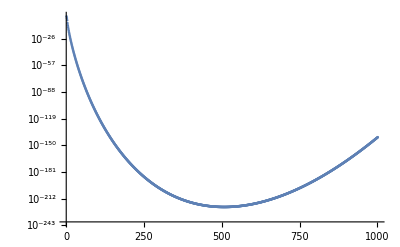

```mathematica
ListLogPlot[(Abs@CoefficientList[ics[[1]][r][[3]],1/r]Table[(1/4000)^n,{n,0,1000}])[[1;;-1]]]
```

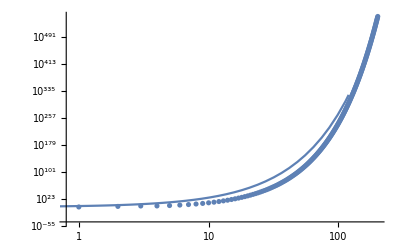

```mathematica
Show[
ListLogLogPlot[Abs@CoefficientList[ics[[1]][r][[3]],1/r]],
LogLogPlot[(500)^n,{n,0,200}]
]
```

```mathematica
With[{r0=4000},{{ics[[1]][r0],ics[[1]]'[r0]},{ics⟦2⟧[r0],ics⟦2⟧'[r0]}}]//RepeatedTiming
```

{0.0667299,{{-0.00021775760794312935398541559912818+0.0001228191897761036497612868928288 ⅈ,-7.716847082398454529909349041179×10^-6-0.000013809150093737280631648264277055 ⅈ},{1.982492706565183709041810119044691+3.419965870986689256267171927983072 ⅈ,-0.2164058283452577645736252694222053+0.125446461022711132465801316746104 ⅈ}}}

```mathematica
ics=MetricReconstructRadiative`Private`hκinfSeries[2,6/10,ω0,MetricReconstructRadiative`Private`testeigs0[[3]],1,4000];//Timing
```

{0.,Null}

```mathematica
ics
```

{{0.00099884273198364773094826603007167+0.0000555973648271179666138448427069 ⅈ,-4.45465725799571125049871912072×10^-6+0.000062016362124485164879214495054711 ⅈ,9.684990381571866282495411368×10^-20},{0.03025189751346889415296930236747-4.0308253814824835723770066516972 ⅈ,0.25068509020973896821511636348235+0.001887612446476231804944592394901 ⅈ,1.438854122369131559245631134×10^-17}}

```mathematica
rd0=MetricReconstructRadiative`Private`hκDs[2,6/10,ω0,MetricReconstructRadiative`Private`testeigs0[[3]],1,4000,ics[[1,1;;2]],ics[[2,1;;2]],30];
```

```mathematica
ics[[1,1;;2]]
```

{-0.0001262692335313400213555562053588-0.00021577562580985591666181913492142 ⅈ,0.000013430355995364469024437468978474-7.786858369119163289994126707586×10^-6 ⅈ}

```mathematica
rd0[[4]]
```

{{-0.0001262692335313400213555562053588-0.00021577562580985591666181913492142 ⅈ,0.000013430355995364469024437468978474-7.786858369119163289994126707586×10^-6 ⅈ,4.8016518097277056966777026097×10^-7+8.35904494432011364098118596855×10^-7 ⅈ,-5.20247240537602421236991569541×10^-8+2.96061798219446648599095767714×10^-8 ⅈ,-1.82531178644127536705450266899×10^-9-3.23777670539900344012397015785×10^-9 ⅈ,2.01496720776485638789363616594×10^-10-1.1252638621162467799529717223×10^-10 ⅈ,6.9363972621670333330232359221×10^-12+1.25392929341756732852053280315×10^-11 ⅈ,-7.80300866621211810383022105685×10^-13+4.27538723067997477641418737216×10^-13 ⅈ,-2.63498711786257381920879390142×10^-14-4.85551282824379078315825013335×10^-14 ⅈ,3.02128781619181964981934534193×10^-15-1.62383801590717556201914744902×10^-15 ⅈ,1.00061658720051865019331801586×10^-16+1.87989274719508905936070565145×10^-16 ⅈ,-1.16965566585314234830174845239×10^-17+6.16528399561534013718505024212×10^-18 ⅈ,-3.7983805461834826747212858778×10^-19-7.27724463206875005593239917687×10^-19 ⅈ,4.52751518561994460966632238419×10^-20-2.33993315728257448150707904635×10^-20 ⅈ,1.44134387923805138357842387581×10^-21+2.81667578825972434247503700873×10^-21 ⅈ,-1.75225706184323262859842186549×10^-22+8.87749672022422925649379114295×10^-23 ⅈ,-5.46728554840440598900157936678×10^-24-1.09004091907447822908308700323×10^-23 ⅈ,6.78065768115300963050543864715×10^-25-3.36675006392377939471921020175×10^-25 ⅈ,2.0730387975150875530476213738×10^-26+4.21778936996378813157025570734×10^-26 ⅈ,-2.62350575152574376015215118419×10^-27+1.2763240592176721366106971239×10^-27 ⅈ,-7.8572574567491009445330755736×10^-29-1.63178611752853583612471945879×10^-28 ⅈ,1.01491236950714430609127190221×10^-29-4.8365650384177086443607865609×10^-30 ⅈ,2.9768613573028856897141990319×10^-31+6.31215964273901730520127777202×10^-31 ⅈ,-3.92564966981599527197303623327×10^-32+1.832041083506100864199954203×10^-32 ⅈ,-1.1273695898246395436393107188×10^-33-2.44134560745446779295871337919×10^-33 ⅈ,1.51820763166252687486582069002×10^-34-6.9366758679969181912033181923×10^-35 ⅈ,4.2676610971409454178763807403×10^-36+9.440984432120139691173918018×10^-36 ⅈ,-5.87066939197420994242843197005×10^-37+2.6253144421248575979236761995×10^-37 ⅈ,-1.6148234338774950076059912026×10^-38-3.65041485767129546721957287508×10^-38 ⅈ,2.26976611718924594037502196073×10^-39-9.9316289641885239670096681355×10^-40 ⅈ,6.1075503801676097872961481538×10^-41+1.41125114914944842452931539346×10^-40 ⅈ},{-3.45181300915386894700486633800079+2.076076765758654193160098582146642 ⅈ,-0.1289220664727680154401425940480427-0.2143539499787886654307234741988973 ⅈ,0.0133111704297590785267025939367-0.00800589063996435868487954054492 ⅈ,0.000497153597954768115523107899914+0.000826611634301732459677377414881 ⅈ,-0.0000513318944339869161364368602747+0.0000308723757584680800939120012132 ⅈ,-1.91711445095292903481607435097×10^-6-3.18767160236038038842972149924×10^-6 ⅈ,1.9795220761575540397546042277×10^-7-1.19048670062342384965685485896×10^-7 ⅈ,7.39264015210789466594024775812×10^-9+1.22927093460970167107280089008×10^-8 ⅈ,-7.63370472146648377959915815344×10^-10+4.5906384563298435883463967319×10^-10 ⅈ,-2.85065797310229837767028213612×10^-11-4.74049370171139456871973278705×10^-11 ⅈ,2.94382681055550031677207807318×10^-12-1.77017265745832032372838709868×10^-12 ⅈ,1.0992200214916712676190414063×10^-13+1.82810609514696176720722676757×10^-13 ⅈ,-1.13524863275780014826492129014×10^-14+6.82577727081338961178583923633×10^-15 ⅈ,-4.23855741794202175968142942599×10^-16-7.04986858260769929201347414416×10^-16 ⅈ,4.37795698804078415303727441059×10^-17-2.63197947448643903694244398749×10^-17 ⅈ,1.63435121239312662167619584233×10^-18+2.71870688628054036231615802589×10^-18 ⅈ,-1.68831587456051624641976578408×10^-19+1.01486141207573749737157475077×10^-19 ⅈ,-6.30182796983581244370559646238×10^-21-1.04844446906524672170301620099×10^-20 ⅈ,6.51084814767159159315274738838×10^-22-3.91313468187698149112844763107×10^-22 ⅈ,2.42986134106246590078731631825×10^-23+4.04324535737996037302164693998×10^-23 ⅈ,-2.51086299135875457123919628085×10^-24+1.50881719967509638288029904747×10^-24 ⅈ,-9.36893433284399272117147465308×10^-26-1.55925202017707642157188446707×10^-25 ⅈ,9.68300125995701115167098649388×10^-27-5.81757771405275065731634695658×10^-27 ⅈ,3.61237324817345041792199205766×10^-28+6.01317753743562988077662601528×10^-28 ⅈ,-3.73420728384813064157288597597×10^-29+2.243062952574172005766703929×10^-29 ⅈ,-1.39279989226106324134434761639×10^-30-2.31895951249307268601941845336×10^-30 ⅈ,1.44008541480896138560279858921×10^-31-8.64837275093606197121611084276×10^-32 ⅈ,5.37005191586049241851570559003×10^-33+8.94300905950777945682942933644×10^-33 ⅈ,-5.55366161537409693006566977765×10^-34+3.33442516275710908053764514944×10^-34 ⅈ,-2.0704362705269654833912665595×10^-35-3.44885928771047618685370920223×10^-35 ⅈ,2.14176514026960863853330478488×10^-36-1.28558607168432571228829991727×10^-36 ⅈ}}

```mathematica
rd0
```

{{{{4000},-0.0001262692335313400213555562053588-0.00021577562580985591666181913492142 ⅈ,0.000013430355995364469024437468978474-7.786858369119163289994126707586×10^-6 ⅈ,4.8016518097277056966777026097×10^-7+8.35904494432011364098118596855×10^-7 ⅈ,-5.20247240537602421236991569541×10^-8+2.96061798219446648599095767714×10^-8 ⅈ,-1.82531178644127536705450266899×10^-9-3.23777670539900344012397015785×10^-9 ⅈ,2.01496720776485638789363616594×10^-10-1.1252638621162467799529717223×10^-10 ⅈ,6.9363972621670333330232359221×10^-12+1.25392929341756732852053280315×10^-11 ⅈ,-7.80300866621211810383022105685×10^-13+4.27538723067997477641418737216×10^-13 ⅈ,-2.63498711786257381920879390142×10^-14-4.85551282824379078315825013335×10^-14 ⅈ,3.02128781619181964981934534193×10^-15-1.62383801590717556201914744902×10^-15 ⅈ,1.00061658720051865019331801586×10^-16+1.87989274719508905936070565145×10^-16 ⅈ,-1.16965566585314234830174845239×10^-17+6.16528399561534013718505024212×10^-18 ⅈ,-3.7983805461834826747212858778×10^-19-7.27724463206875005593239917687×10^-19 ⅈ,4.52751518561994460966632238419×10^-20-2.33993315728257448150707904635×10^-20 ⅈ,1.44134387923805138357842387581×10^-21+2.81667578825972434247503700873×10^-21 ⅈ,-1.75225706184323262859842186549×10^-22+8.87749672022422925649379114295×10^-23 ⅈ,-5.46728554840440598900157936678×10^-24-1.09004091907447822908308700323×10^-23 ⅈ,6.78065768115300963050543864715×10^-25-3.36675006392377939471921020175×10^-25 ⅈ,2.0730387975150875530476213738×10^-26+4.21778936996378813157025570734×10^-26 ⅈ,-2.62350575152574376015215118419×10^-27+1.2763240592176721366106971239×10^-27 ⅈ,-7.8572574567491009445330755736×10^-29-1.63178611752853583612471945879×10^-28 ⅈ,1.01491236950714430609127190221×10^-29-4.8365650384177086443607865609×10^-30 ⅈ,2.9768613573028856897141990319×10^-31+6.31215964273901730520127777202×10^-31 ⅈ,-3.92564966981599527197303623327×10^-32+1.832041083506100864199954203×10^-32 ⅈ,-1.1273695898246395436393107188×10^-33-2.44134560745446779295871337919×10^-33 ⅈ,1.51820763166252687486582069002×10^-34-6.9366758679969181912033181923×10^-35 ⅈ,4.2676610971409454178763807403×10^-36+9.440984432120139691173918018×10^-36 ⅈ,-5.87066939197420994242843197005×10^-37+2.6253144421248575979236761995×10^-37 ⅈ,-1.6148234338774950076059912026×10^-38-3.65041485767129546721957287508×10^-38 ⅈ,2.26976611718924594037502196073×10^-39-9.9316289641885239670096681355×10^-40 ⅈ,6.1075503801676097872961481538×10^-41+1.41125114914944842452931539346×10^-40 ⅈ},{{4000},-3.45181300915386894700486633800079+2.076076765758654193160098582146642 ⅈ,-0.1289220664727680154401425940480427-0.2143539499787886654307234741988973 ⅈ,0.0133111704297590785267025939367-0.00800589063996435868487954054492 ⅈ,0.000497153597954768115523107899914+0.000826611634301732459677377414881 ⅈ,-0.0000513318944339869161364368602747+0.0000308723757584680800939120012132 ⅈ,-1.91711445095292903481607435097×10^-6-3.18767160236038038842972149924×10^-6 ⅈ,1.9795220761575540397546042277×10^-7-1.19048670062342384965685485896×10^-7 ⅈ,7.39264015210789466594024775812×10^-9+1.22927093460970167107280089008×10^-8 ⅈ,-7.63370472146648377959915815344×10^-10+4.5906384563298435883463967319×10^-10 ⅈ,-2.85065797310229837767028213612×10^-11-4.74049370171139456871973278705×10^-11 ⅈ,2.94382681055550031677207807318×10^-12-1.77017265745832032372838709868×10^-12 ⅈ,1.0992200214916712676190414063×10^-13+1.82810609514696176720722676757×10^-13 ⅈ,-1.13524863275780014826492129014×10^-14+6.82577727081338961178583923633×10^-15 ⅈ,-4.23855741794202175968142942599×10^-16-7.04986858260769929201347414416×10^-16 ⅈ,4.37795698804078415303727441059×10^-17-2.63197947448643903694244398749×10^-17 ⅈ,1.63435121239312662167619584233×10^-18+2.71870688628054036231615802589×10^-18 ⅈ,-1.68831587456051624641976578408×10^-19+1.01486141207573749737157475077×10^-19 ⅈ,-6.30182796983581244370559646238×10^-21-1.04844446906524672170301620099×10^-20 ⅈ,6.51084814767159159315274738838×10^-22-3.91313468187698149112844763107×10^-22 ⅈ,2.42986134106246590078731631825×10^-23+4.04324535737996037302164693998×10^-23 ⅈ,-2.51086299135875457123919628085×10^-24+1.50881719967509638288029904747×10^-24 ⅈ,-9.36893433284399272117147465308×10^-26-1.55925202017707642157188446707×10^-25 ⅈ,9.68300125995701115167098649388×10^-27-5.81757771405275065731634695658×10^-27 ⅈ,3.61237324817345041792199205766×10^-28+6.01317753743562988077662601528×10^-28 ⅈ,-3.73420728384813064157288597597×10^-29+2.243062952574172005766703929×10^-29 ⅈ,-1.39279989226106324134434761639×10^-30-2.31895951249307268601941845336×10^-30 ⅈ,1.44008541480896138560279858921×10^-31-8.64837275093606197121611084276×10^-32 ⅈ,5.37005191586049241851570559003×10^-33+8.94300905950777945682942933644×10^-33 ⅈ,-5.55366161537409693006566977765×10^-34+3.33442516275710908053764514944×10^-34 ⅈ,-2.0704362705269654833912665595×10^-35-3.44885928771047618685370920223×10^-35 ⅈ,2.14176514026960863853330478488×10^-36-1.28558607168432571228829991727×10^-36 ⅈ}},{5.79726962042836379161325402496×10^-73,9.4173426672178349144003039618×10^-69},{(-0.0001262692335313400213555562053588-0.00021577562580985591666181913492142 ⅈ)+(0.000013430355995364469024437468978474-7.786858369119163289994126707586×10^-6 ⅈ) (-4000+#1)+(2.40082590486385284833885130485×10^-7+4.17952247216005682049059298427×10^-7 ⅈ) (-4000+#1)^2-(8.67078734229337368728319282569×10^-9-4.93436330365744414331826279523×10^-9 ⅈ) (-4000+#1)^3-(7.60546577683864736272709445412×10^-11+1.3490736272495847667183208991×10^-10 ⅈ) (-4000+#1)^4+(1.67913933980404698991136347162×10^-12-9.37719885096872316627476435247×10^-13 ⅈ) (-4000+#1)^5+(9.63388508634310185142116100291×10^-15+1.74156846307995462294518444882×10^-14 ⅈ) (-4000+#1)^6-(1.54821600520081708409329782874×10^-16-8.48291117198407693732973684953×10^-17 ⅈ) (-4000+#1)^7-(6.53518630422265332145038169995×10^-19+1.20424425303665446010869298942×10^-18 ⅈ) (-4000+#1)^8+(8.32585928183371817079846048812×10^-21-4.47486225723979156200161885202×10^-21 ⅈ) (-4000+#1)^9+(2.75743107143000068946571322714×10^-23+5.18048045413108757539876998305×10^-23 ⅈ) (-4000+#1)^10-(2.93023405145989244704422311506×10^-25-1.54453362885184687579792223879×10^-25 ⅈ) (-4000+#1)^11-(7.92978676101182683882743998725×10^-28+1.51925267724966890631104346559×10^-27 ⅈ) (-4000+#1)^12+(7.27075648377462398979994154538×10^-30-3.75770891480332694810828164626×10^-30 ⅈ) (-4000+#1)^13+(1.65332889575845618728808471507×10^-32+3.23093713984121352274800840411×10^-32 ⅈ) (-4000+#1)^14-(1.33997966521527217745268359156×10^-34-6.7887670948248098233686500942×10^-35 ⅈ) (-4000+#1)^15-(2.61307673482879932317063440693×10^-37+5.20982586409118094128560128676×10^-37 ⅈ) (-4000+#1)^16+(1.90635292269113060265991556738×10^-39-9.46547389078675533396609589948×10^-40 ⅈ) (-4000+#1)^17+(3.2379222032297266793996013258×10^-42+6.58785251193673092330254985659×10^-42 ⅈ) (-4000+#1)^18-(2.15668838507141800343538007892×10^-44-1.0492194547319433790929502038×10^-44 ⅈ) (-4000+#1)^19-(3.2295823795376749563731465626×10^-47+6.7071592363536763350551195731×10^-47 ⅈ) (-4000+#1)^20+(1.98648199928701097234562903313×10^-49-9.4665802446208502461584961184×10^-50 ⅈ) (-4000+#1)^21+(2.6484514500171043946965014047×10^-52+5.61579675772943749801664301903×10^-52 ⅈ) (-4000+#1)^22-(1.51850809531284268843287498344×10^-54-7.0866466705882174437183776823×10^-55 ⅈ) (-4000+#1)^23-(1.8170239244315917577574406089×10^-57+3.9348084395648415229668591547×10^-57 ⅈ) (-4000+#1)^24+(9.78780912270140547234807163739×10^-60-4.4720404459865645573174654999×10^-60 ⅈ) (-4000+#1)^25+(1.0582076509180527617551178527×10^-62+2.34098297190485848662205118676×10^-62 ⅈ) (-4000+#1)^26-(5.39144069887683138291796319229×10^-65-2.4110073631418113695209034917×10^-65 ⅈ) (-4000+#1)^27-(5.2964420005429529458546716738×10^-68+1.19729564025159062316280895115×10^-67 ⅈ) (-4000+#1)^28+(2.56709705463269109453116877401×10^-70-1.1232635498694138761922747233×10^-70 ⅈ) (-4000+#1)^29+(2.3025389375601770289732999411×10^-73+5.32039937344565106098456685978×10^-73 ⅈ) (-4000+#1)^30&,(-3.45181300915386894700486633800079+2.076076765758654193160098582146642 ⅈ)-(0.1289220664727680154401425940480427+0.2143539499787886654307234741988973 ⅈ) (-4000+#1)+(0.00665558521487953926335129696836-0.00400294531998217934243977027246 ⅈ) (-4000+#1)^2+(0.0000828589329924613525871846499857+0.000137768605716955409946229569147 ⅈ) (-4000+#1)^3-(2.13882893474945483901820251145×10^-6-1.28634898993617000391300005055×10^-6 ⅈ) (-4000+#1)^4-(1.59759537579410752901339529247×10^-8+2.65639300196698365702476791603×10^-8 ⅈ) (-4000+#1)^5+(2.7493362168854917218813947607×10^-10-1.65345375086586645785674285967×10^-10 ⅈ) (-4000+#1)^6+(1.4667936809737886241944936028×10^-12+2.43902963216210649022381128985×10^-12 ⅈ) (-4000+#1)^7-(1.89327994083990173105137851028×10^-14-1.13855120444688581060178490374×10^-14 ⅈ) (-4000+#1)^8-(7.85564917631806210777745297652×10^-17+1.3063529821735544997574219541×10^-16 ⅈ) (-4000+#1)^9+(8.11239751586061595230400703588×10^-19-4.87812130031503616547725721638×10^-19 ⅈ) (-4000+#1)^10+(2.75377791178569240925886194861×10^-21+4.57979120357083174805401927903×10^-21 ⅈ) (-4000+#1)^11-(2.37003098268941095032860284838×10^-23-1.42500093336084673032111776585×10^-23 ⅈ) (-4000+#1)^12-(6.80671793796163610001339553256×10^-26+1.13214148611928505072818676696×10^-25 ⅈ) (-4000+#1)^13+(5.0218430847618909890232792388×10^-28-3.01907669702803148880996188589×10^-28 ⅈ) (-4000+#1)^14+(1.24981513164684636663016388062×10^-30+2.0790396698213330448304375007×10^-30 ⅈ) (-4000+#1)^15-(8.06926745237177160921726971594×10^-33-4.85050711453064082584536993258×10^-33 ⅈ) (-4000+#1)^16-(1.77173199614324004935256975543×10^-35+2.94765680833192582815480147216×10^-35 ⅈ) (-4000+#1)^17+(1.01694284759518847863059099202×10^-37-6.11200604921893957257733806432×10^-38 ⅈ) (-4000+#1)^18+(1.99750037847479689149931619999×10^-40+3.32380452956278866861016742173×10^-40 ⅈ) (-4000+#1)^19-(1.03204444031041888198514072234×10^-42-6.2017179261810582443821832492×10^-43 ⅈ) (-4000+#1)^20-(1.83377599523538395483888904339×10^-45+3.05191478938996784876894862845×10^-45 ⅈ) (-4000+#1)^21+(8.61476422626735928075269846675×10^-48-5.17577753312967945934723027368×10^-48 ⅈ) (-4000+#1)^22+(1.39732744437688140384784711329×10^-50+2.32599939810149768887993415894×10^-50 ⅈ) (-4000+#1)^23-(6.01856217763881945226851712398×10^-53-3.61522883499758369372438710574×10^-53 ⅈ) (-4000+#1)^24-(8.97931166150312557072433905295×10^-56+1.49502166885432947405721054357×10^-55 ⅈ) (-4000+#1)^25+(3.57083041328483305419202739619×10^-58-2.14444727561962212439556610844×10^-58 ⅈ) (-4000+#1)^26+(4.93168913477438572646199952957×10^-61+8.21298216516333343799517825654×10^-61 ⅈ) (-4000+#1)^27-(1.82153949585933903704264711096×10^-63-1.09365452031418846034157265961×10^-63 ⅈ) (-4000+#1)^28-(2.34165573784152046533865793902×10^-66+3.90064705445859942843739330043×10^-66 ⅈ) (-4000+#1)^29+(8.07442808264558741742590092555×10^-69-4.84664358602794598839512615419×10^-69 ⅈ) (-4000+#1)^30&},{{-0.0001262692335313400213555562053588-0.00021577562580985591666181913492142 ⅈ,0.000013430355995364469024437468978474-7.786858369119163289994126707586×10^-6 ⅈ,4.8016518097277056966777026097×10^-7+8.35904494432011364098118596855×10^-7 ⅈ,-5.20247240537602421236991569541×10^-8+2.96061798219446648599095767714×10^-8 ⅈ,-1.82531178644127536705450266899×10^-9-3.23777670539900344012397015785×10^-9 ⅈ,2.01496720776485638789363616594×10^-10-1.1252638621162467799529717223×10^-10 ⅈ,6.9363972621670333330232359221×10^-12+1.25392929341756732852053280315×10^-11 ⅈ,-7.80300866621211810383022105685×10^-13+4.27538723067997477641418737216×10^-13 ⅈ,-2.63498711786257381920879390142×10^-14-4.85551282824379078315825013335×10^-14 ⅈ,3.02128781619181964981934534193×10^-15-1.62383801590717556201914744902×10^-15 ⅈ,1.00061658720051865019331801586×10^-16+1.87989274719508905936070565145×10^-16 ⅈ,-1.16965566585314234830174845239×10^-17+6.16528399561534013718505024212×10^-18 ⅈ,-3.7983805461834826747212858778×10^-19-7.27724463206875005593239917687×10^-19 ⅈ,4.52751518561994460966632238419×10^-20-2.33993315728257448150707904635×10^-20 ⅈ,1.44134387923805138357842387581×10^-21+2.81667578825972434247503700873×10^-21 ⅈ,-1.75225706184323262859842186549×10^-22+8.87749672022422925649379114295×10^-23 ⅈ,-5.46728554840440598900157936678×10^-24-1.09004091907447822908308700323×10^-23 ⅈ,6.78065768115300963050543864715×10^-25-3.36675006392377939471921020175×10^-25 ⅈ,2.0730387975150875530476213738×10^-26+4.21778936996378813157025570734×10^-26 ⅈ,-2.62350575152574376015215118419×10^-27+1.2763240592176721366106971239×10^-27 ⅈ,-7.8572574567491009445330755736×10^-29-1.63178611752853583612471945879×10^-28 ⅈ,1.01491236950714430609127190221×10^-29-4.8365650384177086443607865609×10^-30 ⅈ,2.9768613573028856897141990319×10^-31+6.31215964273901730520127777202×10^-31 ⅈ,-3.92564966981599527197303623327×10^-32+1.832041083506100864199954203×10^-32 ⅈ,-1.1273695898246395436393107188×10^-33-2.44134560745446779295871337919×10^-33 ⅈ,1.51820763166252687486582069002×10^-34-6.9366758679969181912033181923×10^-35 ⅈ,4.2676610971409454178763807403×10^-36+9.440984432120139691173918018×10^-36 ⅈ,-5.87066939197420994242843197005×10^-37+2.6253144421248575979236761995×10^-37 ⅈ,-1.6148234338774950076059912026×10^-38-3.65041485767129546721957287508×10^-38 ⅈ,2.26976611718924594037502196073×10^-39-9.9316289641885239670096681355×10^-40 ⅈ,6.1075503801676097872961481538×10^-41+1.41125114914944842452931539346×10^-40 ⅈ},{-3.45181300915386894700486633800079+2.076076765758654193160098582146642 ⅈ,-0.1289220664727680154401425940480427-0.2143539499787886654307234741988973 ⅈ,0.0133111704297590785267025939367-0.00800589063996435868487954054492 ⅈ,0.000497153597954768115523107899914+0.000826611634301732459677377414881 ⅈ,-0.0000513318944339869161364368602747+0.0000308723757584680800939120012132 ⅈ,-1.91711445095292903481607435097×10^-6-3.18767160236038038842972149924×10^-6 ⅈ,1.9795220761575540397546042277×10^-7-1.19048670062342384965685485896×10^-7 ⅈ,7.39264015210789466594024775812×10^-9+1.22927093460970167107280089008×10^-8 ⅈ,-7.63370472146648377959915815344×10^-10+4.5906384563298435883463967319×10^-10 ⅈ,-2.85065797310229837767028213612×10^-11-4.74049370171139456871973278705×10^-11 ⅈ,2.94382681055550031677207807318×10^-12-1.77017265745832032372838709868×10^-12 ⅈ,1.0992200214916712676190414063×10^-13+1.82810609514696176720722676757×10^-13 ⅈ,-1.13524863275780014826492129014×10^-14+6.82577727081338961178583923633×10^-15 ⅈ,-4.23855741794202175968142942599×10^-16-7.04986858260769929201347414416×10^-16 ⅈ,4.37795698804078415303727441059×10^-17-2.63197947448643903694244398749×10^-17 ⅈ,1.63435121239312662167619584233×10^-18+2.71870688628054036231615802589×10^-18 ⅈ,-1.68831587456051624641976578408×10^-19+1.01486141207573749737157475077×10^-19 ⅈ,-6.30182796983581244370559646238×10^-21-1.04844446906524672170301620099×10^-20 ⅈ,6.51084814767159159315274738838×10^-22-3.91313468187698149112844763107×10^-22 ⅈ,2.42986134106246590078731631825×10^-23+4.04324535737996037302164693998×10^-23 ⅈ,-2.51086299135875457123919628085×10^-24+1.50881719967509638288029904747×10^-24 ⅈ,-9.36893433284399272117147465308×10^-26-1.55925202017707642157188446707×10^-25 ⅈ,9.68300125995701115167098649388×10^-27-5.81757771405275065731634695658×10^-27 ⅈ,3.61237324817345041792199205766×10^-28+6.01317753743562988077662601528×10^-28 ⅈ,-3.73420728384813064157288597597×10^-29+2.243062952574172005766703929×10^-29 ⅈ,-1.39279989226106324134434761639×10^-30-2.31895951249307268601941845336×10^-30 ⅈ,1.44008541480896138560279858921×10^-31-8.64837275093606197121611084276×10^-32 ⅈ,5.37005191586049241851570559003×10^-33+8.94300905950777945682942933644×10^-33 ⅈ,-5.55366161537409693006566977765×10^-34+3.33442516275710908053764514944×10^-34 ⅈ,-2.0704362705269654833912665595×10^-35-3.44885928771047618685370920223×10^-35 ⅈ,2.14176514026960863853330478488×10^-36-1.28558607168432571228829991727×10^-36 ⅈ}}}

```mathematica
{ics[[1]][r0],ics[[1]]'[r0]}
```

{{0.0003182732575774796884381398745647+0.0009483942345362855790788190382668 ⅈ,-0.00006037539971668789780872370275028+0.00001920549023383950009892178713197 ⅈ,8.184351316623543293298194204×10^-20}[10],{0.0003182732575774796884381398745647+0.0009483942345362855790788190382668 ⅈ,-0.00006037539971668789780872370275028+0.00001920549023383950009892178713197 ⅈ,8.184351316623543293298194204×10^-20}'[10]}

```mathematica
With[{err=10^-18,nmax=30,r0=4000,r1=10,WP=32,ω=2/r0^(3/2)},
r0+ Sign[r1-r0]SetPrecision[
Min[
Max[
Min[(err/rd0⟦2⟧)^(1/nmax)],
Abs[r1-r0]/10^5
],
Quiet[Abs[π/ω],{Power::infy}],
Abs[r1-r0]
],WP]]
```

3995.085643360705246796985520674638

```mathematica
Get["MetricReconstructRadiative`"]
```

Refactor attempt 2...

```mathematica
Reap[Do[Sow[i],{i,20}]][[2,1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
(test=MetricReconstructRadiative`Private`hκTSolve[2,6/10,2/r0^(3/2),MetricReconstructRadiative`Private`testeigs0[[3]],1,{4000,10},MetricReconstructRadiative`Private`hκinfSeries,PrecisionGoal->20])//Timing
(test2=MetricReconstructRadiative`Private`hκTSolve[2,6/10,2/r0^(3/2),MetricReconstructRadiative`Private`testeigs0[[3]],1,{400,10},MetricReconstructRadiative`Private`hκinfSeries,PrecisionGoal->20,Order->30])//Timing
```

{0.84375,{InterpolatingFunction[{{10.00000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000, 4000.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],InterpolatingFunction[{{10.00000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000, 4000.000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>]}}

{0.203125,{InterpolatingFunction[…],InterpolatingFunction[…]}}

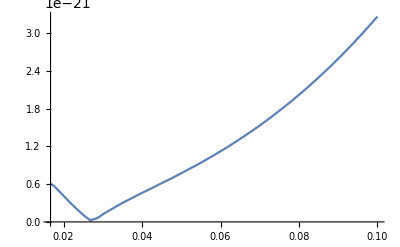

```mathematica
Plot[Abs@{(test[[1]][1/z])/z-(test2[[1]][1/z])/z},{z,1/60,1/10},WorkingPrecision->64]
```

```mathematica
Clear[a]
```

```mathematica
MetricReconstructRadiative`Private`upsol[[4]]/.{
 MetricReconstructRadiative`Private`M$7728->1,
MetricReconstructRadiative`Private`a$7728->a,
MetricReconstructRadiative`Private`m$7728->m,
MetricReconstructRadiative`Private`ω$7728->ω,
MetricReconstructRadiative`Private`λ0$7728->λ0}//Simplify
```

MetricReconstructRadiative`Private`c[2]→(-λ0^2+λ0 (2-4 a m ω+16 ω^2)+4 ω (ⅈ-a^2 (1+m^2-2 ⅈ ω) ω-8 ⅈ ω^2-16 ω^3+a m (1+2 ⅈ ω+8 ω^2)))/(8 ω^2)

```mathematica
(ⅈ (λ0+2 (a m-4 ω) ω))/(2 ω)==(I (λ0+2 (a m-4 ω) ω))/(2 ω)
(-λ0^2+λ0 (2-4 a m ω+16 ω^2)+4 ω (ⅈ-a^2 (1+m^2-2 ⅈ ω) ω-8 ⅈ ω^2-16 ω^3+a m (1+2 ⅈ ω+8 ω^2)))/(8 ω^2)==(-λ0^2+λ0 (2-4 a m ω+16 ω^2)+4 ω (ⅈ-a^2 (1+m^2-2 ⅈ ω) ω-8 ⅈ ω^2-16 ω^3+a m (1+2 ⅈ ω+8 ω^2)))/(8 ω^2)
```

True

True

```mathematica
Simplify[SeriesCoefficient[bla/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r])),{r,∞,2}]==(-λ0^2+λ0 (2-4 a m ω+16 ω^2)+4 ω (ⅈ-a^2 (1+m^2-2 ⅈ ω) ω-8 ⅈ ω^2-16 ω^3+a m (1+2 ⅈ ω+8 ω^2)))/(8 ω^2)]
```

(λ0^2+2 λ0 (-1+2 a m ω-8 ω^2)+4 ω (-ⅈ+a^2 (1+m^2-2 ⅈ ω) ω+8 ⅈ ω^2+16 ω^3-a m (1+2 ⅈ ω+8 ω^2)))/(8 ω^2)+SeriesCoefficient[2^(2 ⅈ ω) bla ⅇ^(-ⅈ r ω) (1/r)^(-1+2 ⅈ ω),{r,∞,2}]==0

```mathematica
Simplify[SeriesCoefficient[bla2/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r])),{r,∞,2}]==(-λ0^2+λ0 (2-4 a m ω+16 ω^2)+4 ω (ⅈ-a^2 (1+m^2-2 ⅈ ω) ω-8 ⅈ ω^2-16 ω^3+a m (1+2 ⅈ ω+8 ω^2)))/(8 ω^2)]
```

(λ0^2+2 λ0 (-1+2 a m ω-8 ω^2)+4 ω (-ⅈ+a^2 (1+m^2-2 ⅈ ω) ω+8 ⅈ ω^2+16 ω^3-a m (1+2 ⅈ ω+8 ω^2)))/(8 ω^2)+SeriesCoefficient[2^(2 ⅈ ω) bla2 ⅇ^(-ⅈ r ω) (1/r)^(-1+2 ⅈ ω),{r,∞,2}]==0

```mathematica
Series[bla2/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r]))-bla/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r])),{r,∞,3}]
```

-2^(2 ⅈ ω) bla ⅇ^(-ⅈ ω r+(1-2 ⅈ ω) Log[r]+O[1/r]^4)+2^(2 ⅈ ω) bla2 ⅇ^(-ⅈ ω r+(1-2 ⅈ ω) Log[r]+O[1/r]^4)

```mathematica
hbla=MetricReconstructRadiative`Private`horsol/.{
 MetricReconstructRadiative`Private`M$7739->1,
MetricReconstructRadiative`Private`a$7739->a,
MetricReconstructRadiative`Private`m$7739->m,
MetricReconstructRadiative`Private`ω$7739->ω,
MetricReconstructRadiative`Private`λ0$7729->λ0,
MetricReconstructRadiative`Private`x->x
};
```

```mathematica
hbla
```

(0.996773666633451208380848703752292+0.0802636748853768667194975227384 ⅈ) x^(0.6103472302953292485895420256298 ⅈ) (1+x ((0.068460586726331258333073106512-0.465036477920199710812248112507 ⅈ)+(0.250994443386503457608878287821-0.30638752668094041020497539688 ⅈ) λ0)+x^2 ((-0.1224035868952314374828112711+0.1264903119148898951601476178 ⅈ)-(0.1274725154013238704855713506+0.01964835159218874566126109879 ⅈ) λ0+(0.007284899609511910839524592472-0.05231936934354205945516561604 ⅈ) λ0^2)+x^3 ((0.068017677810194842933398937-0.033914396718860743625231733 ⅈ)+(0.039144001359670329400700471+0.034302099890515506205926775 ⅈ) λ0-(0.013966082862534644702268208-0.020876201414266209960814989 ⅈ) λ0^2-(0.00083434392249745004356655431+0.0032937965362726033644860686 ⅈ) λ0^3)+x^4 ((-0.0351534458842642744365055+0.008394766258008807193809 ⅈ)-(0.0111207121393474136520569+0.0213797846903283655011627 ⅈ) λ0+(0.00870279166757509729380421-0.00720767016329393329742009 ⅈ) λ0^2-(0.0000135033749734560833684-0.00237185502348675096528543 ⅈ) λ0^3-(0.0000657344815235529077448103+0.000108603497831748562907605 ⅈ) λ0^4)+x^5 ((0.0181561056478491824763-0.0010992798733465183959 ⅈ)+(0.00252282899423702363105+0.0118665811798709511242 ⅈ) λ0-(0.00465630193524974516893-0.00236976801473404060901 ⅈ) λ0^2+(0.000232218150354836482349-0.0013310658506909830326 ⅈ) λ0^3+(0.0000426628031317985400785+0.000109446239021215425281 ⅈ) λ0^4-(2.17649321572706447077×10^-6+2.183720803403478736×10^-6 ⅈ) λ0^5)+x^6 ((-0.0094713063710037209053-0.0007641171174639015387 ⅈ)-(0.000016572876285620612+0.0064171729405481398876 ⅈ) λ0+(0.0024009680589199027667-0.000692601797083377426 ⅈ) λ0^2-(0.0002132079833489828575-0.00070059261821596861806 ⅈ) λ0^3-(0.00002021117594117429068+0.000078362501352804744865 ⅈ) λ0^4+(2.1538521188027899213×10^-6+2.8143675134164929609×10^-6 ⅈ) λ0^5-(4.369102691425726114×10^-8+2.902292041490741528×10^-8 ⅈ) λ0^6))

```mathematica
hbla2=MetricReconstructRadiative`Private`hκhorSeries[2,a,ω0,λ0,1,x+1+√(1-a^2),6][[1,1]];
```

```mathematica
(2.`32)/10^(3/2)
```

0.063245553203367586639977870888654

```mathematica
MetricReconstructRadiative`Private`awsubs$7729
```

{MetricReconstructRadiative`Private`a$7729→0.6,MetricReconstructRadiative`Private`ω$7729→0.062067897646520333960203544164554,MetricReconstructRadiative`Private`m$7729→2,MetricReconstructRadiative`Private`M$7729→1}

```mathematica
MetricReconstructRadiative`Private`νsubs/.{MetricReconstructRadiative`Private`rp$7729->1+√(1-a^2),MetricReconstructRadiative`Private`rp$7729->1+√(1-a^2)}
```

{MetricReconstructRadiative`Private`ν→-((1.8 ⅈ (1.8+MetricReconstructRadiative`Private`rm$7729) (-((0.745355992499929898803057889577092078480206119871 MetricReconstructRadiative`Private`m$7729 √(MetricReconstructRadiative`Private`rm$7729))/(1.8+MetricReconstructRadiative`Private`rm$7729))+MetricReconstructRadiative`Private`ω$7729))/(1.8-MetricReconstructRadiative`Private`rm$7729))}

```mathematica
PowerExpand[hbla[[1;;2]]/
hbla2[[1;;2]]]//Chop
```

1. x^(3.×10^-41 ⅈ)

```mathematica
hbla[[3]]-
Collect[hbla2[[3]],{x,λ0},Chop]
```

0.

```mathematica
Collect[hbla[[3]]-hbla2[[3]],r,Together]
```

0

```mathematica
Collect[hbla3[[3]]-hbla2[[3]],r,Together]
```

0

```mathematica
hbla3=MetricReconstructRadiative`Private`hκinfSeries[2,a,2/10^(3/2),λ0,1,10][[1]][ r];
```

```mathematica
Length[hbla2[[3]]
```

3

```mathematica
Simplify[(hbla3-hbla2)/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r])),r>0]
```

0

```mathematica
xhor
```

0.00010000000000000000479217360238593

```mathematica
rmin
```

1.90010000000000000000479217360239

```mathematica
rhor
```

1.80010000000000000000479217360238593

0.062067897646520333960203544164553609973981736212

```mathematica
κbla2=MetricReconstructRadiative`Private`hκhorSeries[2,a,ω0,MetricReconstructRadiative`Private`testeigs0[[3]],MetricReconstructRadiative`Private`γllsubs[[3,2]],rhor,30][[2,1]]
```

0.0000645307562628313982997555776967-9.25978582354508877568660839725×10^-6 ⅈ

```mathematica
(MetricReconstructRadiative`Private`horr0sol a^2 MetricReconstructRadiative`Private`γllsubs[[3,2]]+MetricReconstructRadiative`Private`horr2sol /.{
 MetricReconstructRadiative`Private`M$7739->1,
MetricReconstructRadiative`Private`a$7739->a,
MetricReconstructRadiative`Private`m$7739->2,
MetricReconstructRadiative`Private`ω$7739->ω0,
MetricReconstructRadiative`Private`λ0$7729->MetricReconstructRadiative`Private`testeigs0[[3]],
MetricReconstructRadiative`Private`x->xhor
})-κbla2
```

1.×10^-35-6.×10^-36 ⅈ

```mathematica
κ0bla=MetricReconstructRadiative`Private`horr0sol/.{
 MetricReconstructRadiative`Private`M$7739->1,
MetricReconstructRadiative`Private`a$7739->a,
MetricReconstructRadiative`Private`m$7739->m,
MetricReconstructRadiative`Private`ω$7739->ω,
MetricReconstructRadiative`Private`λ0$7729->λ0,
MetricReconstructRadiative`Private`x->x
};
```

```mathematica
κ2bla=MetricReconstructRadiative`Private`horr2sol/.{
 MetricReconstructRadiative`Private`M$7739->1,
MetricReconstructRadiative`Private`a$7739->a,
MetricReconstructRadiative`Private`m$7739->m,
MetricReconstructRadiative`Private`ω$7739->ω,
MetricReconstructRadiative`Private`λ0$7729->λ0,
MetricReconstructRadiative`Private`x->x
};
```

```mathematica
Length[κbla2]
Length[κ0bla]
Length[κ2bla]
```

3

3

3

{{0,0},{0,0},{InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729]},{InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729]},{InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729]},{InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729],InterpolatingFunction[…][MetricReconstructRadiative`Private`r$7729]}}

```mathematica
κ0bla[[1;;2]]
κ2bla[[1;;2]]
```

2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r])

2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r])

```mathematica
Get["MetricReconstructRadiative`"]
```

Refactor attempt 2...

```mathematica
newupsol=MetricReconstructRadiative`Private`hκTSolve[2,a,ω0, MetricReconstructRadiative`Private`testeigs0[[3]],MetricReconstructRadiative`Private`γllsubs[[3,2]],{4000,10},MetricReconstructRadiative`Private`hκinfSeries,MaxSteps-> 10^6];
```

```mathematica
newinsol=MetricReconstructRadiative`Private`hκTSolve[2,a,ω0, MetricReconstructRadiative`Private`testeigs0[[3]],MetricReconstructRadiative`Private`γllsubs[[3,2]],{1+√(1-a^2)+1/√2 10^-1,10},MetricReconstructRadiative`Private`hκhorSeries];
```

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]
```

```mathematica
Length/@InterpolatingFunctionCoordinates@newinsol[[1]]
Length/@InterpolatingFunctionCoordinates@newupsol[[1]]
```

{61}

{335}

```mathematica
hser=Function[r,Evaluate[MetricReconstructRadiative`Private`hκhorSeries[2,a,ω0,MetricReconstructRadiative`Private`testeigs0[[3]],MetricReconstructRadiative`Private`γllsubs[[3,2]],r,65][[1,1]]]]
```

Function[r,(0.996773666633451208380848703752291586747712066131+0.080263674885376866719497522738421064691539015562 ⅈ) (1+(1.53733674142482368776018323219-2.25808546325435657184226573584 ⅈ) (-1.8+r)-(0.61890430457684261515928084737+1.7803586420438070375384887908 ⅈ) (-1.8+r)^2-(0.34844857179959267269881671306-0.2216324043376884920537583274 ⅈ) (-1.8+r)^3+(0.1180130065984311314871650776-0.015573224818902283208437468 ⅈ) (-1.8+r)^4-(0.0449062952443255448124667931+0.0038917349598838198987274469 ⅈ) (-1.8+r)^5+(0.0192509160721007592617130325+0.004617311965568621409475909 ⅈ) (-1.8+r)^6-(0.0088723346813959494154861896+0.0032531505134363702022768133 ⅈ) (-1.8+r)^7+(0.004287570104111403659656359+0.002059402488758474151508155 ⅈ) (-1.8+r)^8-(0.00214112485171021303427756+0.001256912870020129824999198 ⅈ) (-1.8+r)^9+(0.001094963772683586645716148+0.0007558453283197045728075497 ⅈ) (-1.8+r)^10-(0.0005700373478806489786453828+0.000451666162848863824319679 ⅈ) (-1.8+r)^11+(0.000300865908192244789711667+0.000269221836820688893593307 ⅈ) (-1.8+r)^12-(0.000160520014949209890067778+0.00016036572924079035497082 ⅈ) (-1.8+r)^13+(0.000086380895135707741588959+0.000095549347212659523542866 ⅈ) (-1.8+r)^14-(0.000046806181213776446429611+0.000056972902069533555143693 ⅈ) (-1.8+r)^15+(0.00002550361893393511613287+0.00003400473145170650759358 ⅈ) (-1.8+r)^16-(0.00001395842278531028130312+0.00002031842218519258982898 ⅈ) (-1.8+r)^17+(7.6666532450019192038×10^-6+0.00001215451667117025573613 ⅈ) (-1.8+r)^18-(4.22244105159099900565×10^-6+7.27917160263277010285×10^-6 ⅈ) (-1.8+r)^19+(2.33024326894328605281×10^-6+4.3642750240380603907×10^-6 ⅈ) (-1.8+r)^20-(1.2877634719062983207×10^-6+2.6194611084841208186×10^-6 ⅈ) (-1.8+r)^21+(7.1219807454837164789×10^-7+1.5738468981201221369×10^-6 ⅈ) (-1.8+r)^22-(3.939439153335106037×10^-7+9.4654988984750639919×10^-7 ⅈ) (-1.8+r)^23+(2.178079800282399736×10^-7+5.698160148592385109×10^-7 ⅈ) (-1.8+r)^24-(1.20294254290076854×10^-7+3.433332793253978215×10^-7 ⅈ) (-1.8+r)^25+(6.63212738643281739×10^-8+2.07046534054022717×10^-7 ⅈ) (-1.8+r)^26-(3.6472911226710132×10^-8+1.2496040750206315×10^-7 ⅈ) (-1.8+r)^27+(1.9990467783636068×10^-8+7.54765202982949722×10^-8 ⅈ) (-1.8+r)^28-(1.0908586222323847×10^-8+4.5621528905392061×10^-8 ⅈ) (-1.8+r)^29+(5.919290049946565×10^-9+2.7595030301517227×10^-8 ⅈ) (-1.8+r)^30-(3.188986198145202×10^-9+1.67024616873997×10^-8 ⅈ) (-1.8+r)^31+(1.70233303876413×10^-9+1.011591248634532×10^-8 ⅈ) (-1.8+r)^32-(8.97991882318826×10^-10+6.130443137849766×10^-9 ⅈ) (-1.8+r)^33+(4.663297090058×10^-10+3.7173114953516×10^-9 ⅈ) (-1.8+r)^34-(2.3707429952198×10^-10+2.25530417710519×10^-9 ⅈ) (-1.8+r)^35+(1.169600250513×10^-10+1.3690202562256×10^-9 ⅈ) (-1.8+r)^36-(5.515838181079×10^-11+8.3144465512369×10^-10 ⅈ) (-1.8+r)^37+(2.41452083083×10^-11+5.0520341722936×10^-10 ⅈ) (-1.8+r)^38-(9.13648964278×10^-12+3.071142510101×10^-10 ⅈ) (-1.8+r)^39+(2.2734900539×10^-12+1.867782164758×10^-10 ⅈ) (-1.8+r)^40+(5.651311233×10^-13-1.13641596935×10^-10 ⅈ) (-1.8+r)^41-(1.502154273×10^-12-6.91713111092×10^-11 ⅈ) (-1.8+r)^42+(1.604184224×10^-12-4.21197126066×10^-11 ⅈ) (-1.8+r)^43-(1.388257989×10^-12-2.5657185823×10^-11 ⅈ) (-1.8+r)^44+(1.091377308×10^-12-1.5634742719×10^-11 ⅈ) (-1.8+r)^45-(8.11992262×10^-13-9.53069906×10^-12 ⅈ) (-1.8+r)^46+(5.82953217×10^-13-5.811731973×10^-12 ⅈ) (-1.8+r)^47-(4.08213392×10^-13-3.545095925×10^-12 ⅈ) (-1.8+r)^48+(2.8065071×10^-13-2.16315208×10^-12 ⅈ) (-1.8+r)^49-(1.9025757×10^-13-1.32031656×10^-12 ⅈ) (-1.8+r)^50+(1.2755805×10^-13-8.0611421×10^-13 ⅈ) (-1.8+r)^51-(8.476063×10^-14-4.9230962×10^-13 ⅈ) (-1.8+r)^52+(5.591032×10^-14-3.0074559×10^-13 ⅈ) (-1.8+r)^53-(3.66546×10^-14-1.837704×10^-13 ⅈ) (-1.8+r)^54+(2.39064×10^-14-1.123217×10^-13 ⅈ) (-1.8+r)^55-(1.5523×10^-14-6.86688×10^-14 ⅈ) (-1.8+r)^56+(1.0041×10^-14-4.19914×10^-14 ⅈ) (-1.8+r)^57-(6.4734×10^-15-2.5684×10^-14 ⅈ) (-1.8+r)^58+(4.1612×10^-15-1.5713×10^-14 ⅈ) (-1.8+r)^59-(2.668×10^-15-9.6153×10^-15 ⅈ) (-1.8+r)^60+(1.707×10^-15-5.885×10^-15 ⅈ) (-1.8+r)^61-(1.09×10^-15-3.603×10^-15 ⅈ) (-1.8+r)^62+(6.94×10^-16-2.206×10^-15 ⅈ) (-1.8+r)^63-(4.42×10^-16-1.35×10^-15 ⅈ) (-1.8+r)^64+(2.8×10^-16-8.28×10^-16 ⅈ) (-1.8+r)^65) (-1.8+r)^(0.61034723029532924858954202562975437755854109352 ⅈ)]

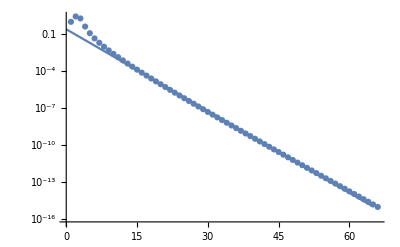

```mathematica
Show[
ListLogPlot[Abs[CoefficientList[hser[r][[2]]/.-1.79999999999999999999999999999999999999999999999999999999987255264710940381784`48.60205999132796+r->x,x]]],
LogPlot[1/4(6/10)^n,{n,0,65}]
]
```

```mathematica
hser[[1,3]]
```

Part::partd: Part specification Function[r,(0.996773666633451208380848703752291586747712066131+0.080263674885376866719497522738421064691539015562 ⅈ) (1+«14»+«1») (-1.8+r)^(0.61034723029532924858954202562975437755854109352 ⅈ)]⟦1,3⟧ is longer than depth of object.

Function[r,(0.996773666633451208380848703752291586747712066131+0.080263674885376866719497522738421064691539015562 ⅈ) (1+(1.53733674142482368776018323219-2.25808546325435657184226573584 ⅈ) (-1.8+r)-(0.61890430457684261515928084737+1.7803586420438070375384887908 ⅈ) (-1.8+r)^2-(0.34844857179959267269881671306-0.2216324043376884920537583274 ⅈ) (-1.8+r)^3+(0.1180130065984311314871650776-0.015573224818902283208437468 ⅈ) (-1.8+r)^4-(0.0449062952443255448124667931+0.0038917349598838198987274469 ⅈ) (-1.8+r)^5+(0.0192509160721007592617130325+0.004617311965568621409475909 ⅈ) (-1.8+r)^6-(0.0088723346813959494154861896+0.0032531505134363702022768133 ⅈ) (-1.8+r)^7+(0.004287570104111403659656359+0.002059402488758474151508155 ⅈ) (-1.8+r)^8-(0.00214112485171021303427756+0.001256912870020129824999198 ⅈ) (-1.8+r)^9+(0.001094963772683586645716148+0.0007558453283197045728075497 ⅈ) (-1.8+r)^10) (-1.8+r)^(0.61034723029532924858954202562975437755854109352 ⅈ)]⟦1,3⟧

```mathematica
hserp=Function[r,Evaluate[MetricReconstructRadiative`Private`hκhorSeries[2,a,ω0,MetricReconstructRadiative`Private`testeigs0[[3]],MetricReconstructRadiative`Private`γllsubs[[3,2]],r,10][[1,2]]]]
```

Function[r,(-0.048988711659614548901258145716535863248301728718+0.60837804666104678835610359492159145952974614387 ⅈ) (1+(1.53733674142482368776018323219-2.25808546325435657184226573584 ⅈ) (-1.8+r)-(0.61890430457684261515928084737+1.7803586420438070375384887908 ⅈ) (-1.8+r)^2-(0.34844857179959267269881671306-0.2216324043376884920537583274 ⅈ) (-1.8+r)^3+(0.1180130065984311314871650776-0.015573224818902283208437468 ⅈ) (-1.8+r)^4-(0.0449062952443255448124667931+0.0038917349598838198987274469 ⅈ) (-1.8+r)^5+(0.0192509160721007592617130325+0.004617311965568621409475909 ⅈ) (-1.8+r)^6-(0.0088723346813959494154861896+0.0032531505134363702022768133 ⅈ) (-1.8+r)^7+(0.004287570104111403659656359+0.002059402488758474151508155 ⅈ) (-1.8+r)^8-(0.00214112485171021303427756+0.001256912870020129824999198 ⅈ) (-1.8+r)^9+(0.001094963772683586645716148+0.0007558453283197045728075497 ⅈ) (-1.8+r)^10) (-1.8+r)^(-1+0.61034723029532924858954202562975437755854109352 ⅈ)+(0.996773666633451208380848703752291586747712066131+0.080263674885376866719497522738421064691539015562 ⅈ) ((1.53733674142482368776018323219-2.25808546325435657184226573584 ⅈ)-(1.2378086091536852303185616947+3.5607172840876140750769775817 ⅈ) (-1.8+r)-(1.0453457153987780180964501392-0.6648972130130654761612749823 ⅈ) (-1.8+r)^2+(0.4720520263937245259486603104-0.062292899275609132833749872 ⅈ) (-1.8+r)^3-(0.224531476221627724062333965+0.019458674799419099493637235 ⅈ) (-1.8+r)^4+(0.115505496432604555570278195+0.027703871793411728456855454 ⅈ) (-1.8+r)^5-(0.062106342769771645908403327+0.022772053594054591415937693 ⅈ) (-1.8+r)^6+(0.034300560832891229277250872+0.01647521991006779321206524 ⅈ) (-1.8+r)^7-(0.01927012366539191730849804+0.01131221583018116842499278 ⅈ) (-1.8+r)^8+(0.01094963772683586645716148+0.007558453283197045728075497 ⅈ) (-1.8+r)^9) (-1.8+r)^(0.61034723029532924858954202562975437755854109352 ⅈ)]

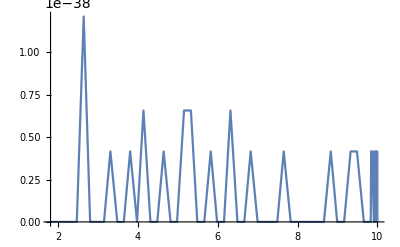

```mathematica
Plot[Abs[hser'[r]-hserp[r]],{r,rhor+10^-2,10},PlotRange->All,WorkingPrecision->32]
```

```mathematica
1+√(1-a^2)
```

1.8

```mathematica
hserinf=Function[r,Evaluate[MetricReconstructRadiative`Private`hκinfSeries[2,a,ω0,MetricReconstructRadiative`Private`testeigs0[[3]],MetricReconstructRadiative`Private`γllsubs[[3,2]],r,30][[1,1]]]]
```

Function[r,(0.9963004659802313017880622554014166826491727604943-0.085938242288133694881273321009904425688308002173 ⅈ) ⅇ^(0.062067897646520333960203544164553609973981736212 ⅈ r) (1+(8.815711356729188744910374035×10^56+1.899318529377717991565198388×10^57 ⅈ)/r^30-(8.218685260860482326928311581×10^54-3.728199734140539868949564263×10^54 ⅈ)/r^29-(1.631875318465784741247784299×10^52+3.685377238946893378107107931×10^52 ⅈ)/r^28+(1.714806702257839845616496452×10^50-7.401890171469874355043019729×10^49 ⅈ)/r^27+(3.483567562855583219211208603×10^47+8.291365857192106957686728288×10^47 ⅈ)/r^26-(4.172437818980355204522503999×10^45-1.703450908744171311269276327×10^45 ⅈ)/r^25-(8.667629212418660900441939668×10^42+2.188968632370810892211106049×10^43 ⅈ)/r^24+(1.199426620107167318886452374×10^41-4.596485136999557938974115058×10^40 ⅈ)/r^23+(2.544768848757107471802741941×10^38+6.878059004655272834922039305×10^38 ⅈ)/r^22-(4.136909188816828288118330126×10^36-1.473558210655538928802488256×10^36 ⅈ)/r^21-(8.94220190903702708280872684×10^33+2.616155866874770030540081233×10^34 ⅈ)/r^20+(1.744235003601360985702719244×10^32-5.699123310659609170066020084×10^31 ⅈ)/r^19+(3.823449768944625090730399144×10^29+1.229740889183316416870944716×10^30 ⅈ)/r^18-(9.199541500280696530371137163×10^27-2.706775624350519879728004018×10^27 ⅈ)/r^17-(2.027332561163205878553864663×10^25+7.330536187972435807352186231×10^25 ⅈ)/r^16+(6.249343968577140764745684017×10^23-1.610786680401350124353670816×10^23 ⅈ)/r^15+(1.36126069160316329368476493×10^21+5.728881657844407085026123284×10^21 ⅈ)/r^14-(5.680949314602438948356889714×10^19-1.226460628673917495917086619×10^19 ⅈ)/r^13-(1.179781380790357033782274044×10^17+6.13680524959319036251399437×10^17 ⅈ)/r^12+(7.283041971704570733336358337×10^15-1.210611643263882974853798729×10^15 ⅈ)/r^11+(1.31607852635061879428882029×10^13+9.595153776965658805440134953×10^13 ⅈ)/r^10-(1.421838719773192342680170762×10^12-1.47965737551607272902747876×10^11 ⅈ)/r^9-(1.57503479853082334978138448×10^9+2.410425994002475589055222792×10^10 ⅈ)/r^8+(4.783099816383973900784613413×10^8-8.69384350153899940308879524×10^6 ⅈ)/r^7-(508670.287675413643064599661-1.147170385219683168208051225×10^7 ⅈ)/r^6-(356644.66559807726059289996164+47774.04146761946771384765239 ⅈ)/r^5-(24.674310910251407135381796+15269.493846491669195031364883 ⅈ)/r^4-(1064.0535849484917749885319627-173.428150913355273782566652 ⅈ)/r^3-(767.32469976852794962939037497-9.0297670029876143143820929603 ⅈ)/r^2+(48.0954694717458943431561363491 ⅈ)/r) r^(-1+0.12413579529304066792040708832910721994796347242 ⅈ)]

```mathematica
(ⅈ (a m-2 (1+√(1-a^2)) ω))/(2 √(1-a^2))/.{m->2,ω->ω0}
```

0.61034723029532924858954202562975437755854109352 ⅈ

```mathematica
Series[Expand[(testeq/.h0->hserinf)/(2^(-2 I ω) E^(I r ω-(1-2 I ω) Log[r])/.ω->ω0)]//Simplify//Chop,{r,∞,10}]
```

0.5 r^2+(0.+24. ⅈ) r-(380.-4. ⅈ)-(530.-90. ⅈ)/r-(30.+7600. ⅈ)/r^2-(180000.+24000. ⅈ)/r^3-(300000.-5.7×10^6 ⅈ)/r^4+(2.4×10^8-4.×10^6 ⅈ)/r^5-(8.×10^8+1.2×10^10 ⅈ)/r^6-(7.11×10^11-7.4×10^10 ⅈ)/r^7+(6.6×10^12+4.8×10^13 ⅈ)/r^8+(3.64×10^15-6.1×10^14 ⅈ)/r^9+(2.6×10^17+1.47×10^18 ⅈ)/r^10+O[1/r]^11

```mathematica
Series[Collect[Expand[(testeq/.h0->hser/.r->x+1+√(1-a^2))/x^(0.6103472302953292485895420256297543775585410935240338949937`47.61458741717262 ⅈ)]//Chop,x]//Chop,{x,0,7}]
```

(1.64040563011544985593892929748606+0.13209115427418900656396659812773 ⅈ)+(4.6143215612478672445801883431-3.3566329077276965247646262548 ⅈ) x+(2.802816588191275969305886375-6.7914643812455012100250432278 ⅈ) x^2-(0.597280064395113988639528854+4.029886107143461945741328989 ⅈ) x^3-(0.698562512403986022371527905+0.574793757547679346272819082 ⅈ) x^4-(0.04171917288687817725417516-0.073267561347195889765254764 ⅈ) x^5+(0.010402230109155737321931-0.00637861290916075581009424 ⅈ) x^6-(0.00247627237428274876517893-0.00081541069349117055863303 ⅈ) x^7+O[x]^8

LogPlot::precw: The precision of the argument function ({(«1»)-0,Charting`Private`pvar$106493-0,(0.36-2 Charting`Private`pvar$106493+(Charting`Private`pvar$106493)^2)-0,Charting`Private`pvar$106493-0,Im[Charting`Private`pvar$106493]-0}) is less than WorkingPrecision (32.).

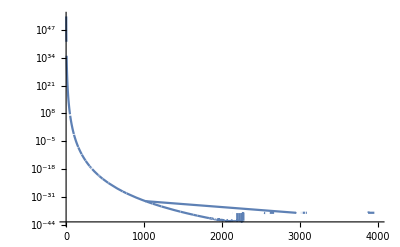

```mathematica
LogPlot[Evaluate[Abs[testeq/.h0->hserinf]],{r, 1+√(1-a^2),4000},WorkingPrecision->32]
```

```mathematica
1+√(1-a^2)+2 10^-4,2
```

```mathematica
Lgrid=NGrid["testL",Table[{1+√(1-a^2),1+√(1-a^2)}+√2 10^i,{i, -2,0,1/10}]]
```

NGrid[{testL,21},<>]

```mathematica
Rgrid=NGrid["testR",Table[{r,r},{r,10,20,10}]]
```

NGrid[{testR,2},<>]

```mathematica
Needs["MSTMode`"]
```

```mathematica
MM=MSTMode[{0,2,2,6/10,SetPrecision[ω0,100]},{Lgrid,Rgrid},Verbose->True,"Interpolator"->Automatic]
```

Finding homogeneous MST solutions for s=0 l=2 m=2 a=3/5 ω=0.06206789764652033396020354416455360997398173621154049111395194127912749977431768704013999077253823171 mode.

ω=0.0620679

Spin weighted speroidal harmonic eigenvalue computed in:0.016 seconds. Value= 5.9998

Renormalized angular momentum (ν) computed in:0.188 seconds. ν= 1.99428

Spin Weighted Spheroidal Harmonics computed in:0. seconds. Values (at zmax):

Asymptotic Homogeneous amplitudes computed in:0.5 seconds.

Exterior Homogeneous Solution computed in:0.296 seconds.

Interior Homogeneous Solution computed in:0.219 seconds.

MSTMode[{0,2,2,3/5,0.06206789764652033396020354416455360997398173621154049111395194127912749977431768704013999077253823171},…]

```mathematica
MM2=MSTMode[{0,2,2,6/10,SetPrecision[ω0,100]},{Lgrid,Rgrid},Verbose->True,"Interpolator"->None]
```

Finding homogeneous MST solutions for s=0 l=2 m=2 a=3/5 ω=0.06206789764652033396020354416455360997398173621154049111395194127912749977431768704013999077253823171 mode.

ω=0.0620679

Spin weighted speroidal harmonic eigenvalue computed in:0. seconds. Value= 5.9998

Renormalized angular momentum (ν) computed in:0.187 seconds. ν= 1.99428

Spin Weighted Spheroidal Harmonics computed in:0. seconds. Values (at zmax):

Asymptotic Homogeneous amplitudes computed in:0.485 seconds.

Exterior Homogeneous Solution computed in:1.562 seconds.

Interior Homogeneous Solution computed in:0.313 seconds.

MSTMode[{0,2,2,3/5,0.06206789764652033396020354416455360997398173621154049111395194127912749977431768704013999077253823171},…]

```mathematica
NGridData@Re@(newinsol2[[1]]/@Lgrid)
```

{{1.81,-0.939777403115424826774838670348551613655318898},{1.81258925411794167210423954106395800606093617409,-0.8830666227216543809119914512972411581160061357},{1.81584893192461113485202101373391507013269442134,-0.8115656646734608358287238348881551504968162966},{1.81995262314968879601352455396739535557986274315,-0.7271302027005505909538484143945793066928294625},{1.82511886431509580111085032067799327394158518101,-0.6318619405101595508320920521391330235021120828},{1.83162277660168379331998893544432718533719555139,-0.528028027444841285793300646556372749587599913},{1.83981071705534972507702523050877520434876770373,-0.4179613815425193059832698953156489813320608783},{1.85011872336272722850015541868849457680604719898,-0.3039403966729917019353567581320509850333061851},{1.86309573444801932494343601366223438646729452572,-0.1880465455047051282703289072790683733593222098},{1.87943282347242815020659182828363879325889606318,-0.07199826487744525049457759587512530459377787906},{1.9,0.043041108583740179500986877860054879558546126},{1.92589254117941672104239541063958006060936174095,0.1566853185999620564666136884194924023888099857},{1.95848931924611134852021013733915070132694421338,0.2695849578982005308954676388027977883915482536},{1.99952623149688796013524553967395355579862743154,0.38374065689045646379356475067778627705752433151},{2.05118864315095801110850320677993273941585181008,0.50289945132727787349113170872225444557777527319},{2.11622776601683793319988935444327185337195551393,0.63308819181455654427242087364580041044258030077},{2.1981071705534972507702523050877520434876770373,0.78337696840396883237840345376245970774402104606},{2.30118723362727228500155418688494576806047198983,0.967026635654963981408856587007522245053833992536},{2.43095734448019324943436013662234386467294525719,1.20326764066025870558504009575041751600733613093},{2.59432823472428150206591828283638793258896063176,1.52009748972820542535760140361874609801746545297},{2.8,1.9586948478878574459826583411341958358480393642}}

InterpolatingFunction::dmval: Input value {1.81414213562373095048801688724209698078569671875} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.81780389391375444859428294555680118116144140979} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.82241377447691298651380641448516806002158243455} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

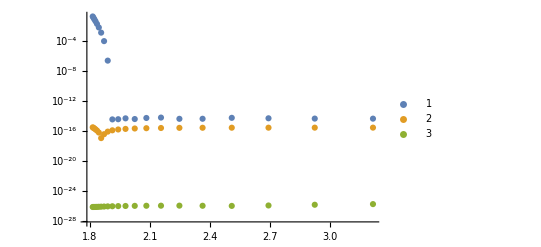

```mathematica
ListLogPlot[{
(*NGridData@Abs[(MSTRhor[MM][[1]])/MSTAhor[MM]/(MSTRhor[MM2][[1]])/MSTAhor[MM2]-1],*)
NGridData@Abs[(MSTRhor[MM][[1]])/MSTAhor[MM]/(oldinh/@Lgrid)-1],
NGridData@Abs[(MSTRhor[MM][[1]])/MSTAhor[MM]/(newinsol2[[1]]/@Lgrid)-1],
NGridData@Abs[(MSTRhor[MM][[1]])/MSTAhor[MM]/(newinsol[[1]]/@Lgrid)-1](*,
NGridData@Abs[(MSTRhor[MM][[1]])/MSTAhor[MM]/(hser/@Lgrid)-1]*)
},PlotLegends->Automatic]
```

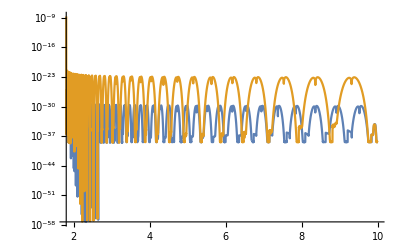

```mathematica
LogPlot[
Evaluate@{
Abs[testeq/.h0->newinsol2[[1]]],
Abs[testeq/.h0->newinsol[[1]]]
},{r,1+√(1-a^2)+2 10^-4,10},WorkingPrecision->32]
```

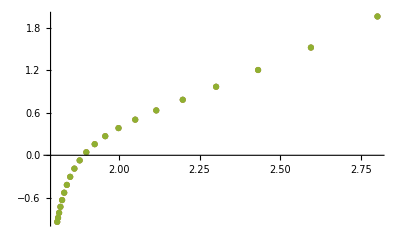

```mathematica
ListPlot[{NGridData@Re@((MSTRhor[MM][[1]])/MSTAhor[MM]),NGridData@Re@((MSTRhor[MM2][[1]])/MSTAhor[MM2]),NGridData@Re@(newinsol2[[1]]/@Lgrid)}]
```

LogPlot::precw: The precision of the argument function ({(2 ((-0.048988711659614548901258145716535863248301728718+0.60837804666104678835610359492159145952974614387 ⅈ) (1+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+«1») Plus[«2»]^(-1+0.61034723029532924858954202562975437755854109352 ⅈ)+(0.996773666633451208380848703752291586747712066131+0.080263674885376866719497522738421064691539015562 ⅈ) ((1.53733674142482368776018323219-2.25808546325435657184226573584 ⅈ)+Times[«2»]+«6»+Times[«2»]+Times[«2»]) Plus[«2»]^(0.61034723029532924858954202562975437755854109352 ⅈ)) (-1+Charting`Private`pvar$106657)+«1»+«1»)-0,«2»,«1»}) is less than WorkingPrecision (32.).

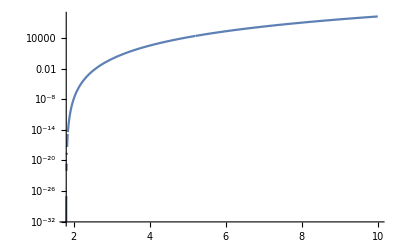

```mathematica
LogPlot[Evaluate[Abs[testeq/.h0->hser]],{r, 1+√(1-a^2),10},WorkingPrecision->32,PlotRange->All]
```

```mathematica
prefac=ⅇ^(-ⅈ (-(a m)/(2+2 √(1-a^2))+ω) (1+√(1-a^2)-Log[4]+1/2 (1-1/(√(1-a^2))) Log[4-4 a^2])) x^ν/. ν-> (ⅈ (a m-2 (1+√(1-a^2)) ω))/(2 √(1-a^2))/.{x->r-(1+√(1-a^2))}/.{m->2,ω->ω0}
```

(0.996773666633451208380848703752291586747712066131+0.080263674885376866719497522738421064691539015562 ⅈ) (-1.8+r)^(0.61034723029532924858954202562975437755854109352 ⅈ)

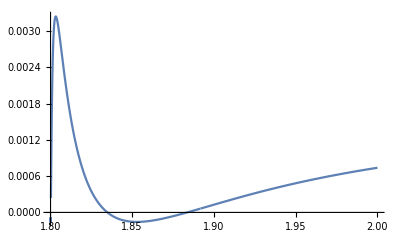

```mathematica
Plot[{
Abs@newinsol[[1]][r]/Abs@newinsol2[[1]][r]-1,
(*Arg@prefac,*)
(*Arg@hser[r]*)
},{r,1+√(1-a^2)+2 10^-4,2},PlotRange->All,WorkingPrecision->32]
```

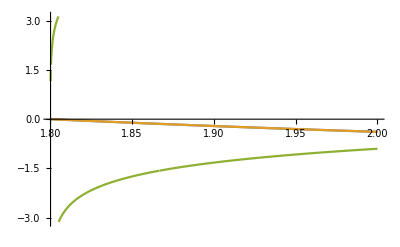

```mathematica
Plot[{
Arg@((newinsol[[1]][r])/prefac),
Arg@((newinsol2[[1]][r])/prefac),
Arg@prefac
(*Arg@hser[r]*)
},{r,1+√(1-a^2)+2 10^-4,2},PlotRange->All,WorkingPrecision->32]
```

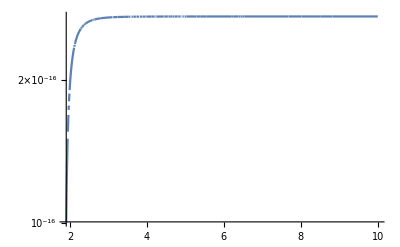

```mathematica
LogPlot[{
Abs[(newinsol2[[1]][r])/(newinsol[[1]][r])-1]
},{r,rhor+10^-1,10},PlotRange->All,WorkingPrecision->32]
```

```mathematica
oldinh=Head[MetricReconstructRadiative`Private`κinsol[[3,1]]]
oldinhp=Head[MetricReconstructRadiative`Private`κinsol[[3,4]]]
oldinκ=Function[r,Evaluate[a^2 MetricReconstructRadiative`Private`γllsubs[[3,2]] Head[MetricReconstructRadiative`Private`κinsol[[3,2]]][r]+ Head[MetricReconstructRadiative`Private`κinsol[[3,3]]][r]]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

Function[r,InterpolatingFunction[…][r]+0.05143051231646310020934995462712 InterpolatingFunction[…][r]]

InterpolatingFunction[…]

```mathematica
olduph=Head[MetricReconstructRadiative`Private`κupsol[[3,1]]]
olduphp=Head[MetricReconstructRadiative`Private`κupsol[[3,4]]]
oldupκ=Function[r,Evaluate[a^2 MetricReconstructRadiative`Private`γllsubs[[3,2]] Head[MetricReconstructRadiative`Private`κupsol[[3,2]]][r]+ Head[MetricReconstructRadiative`Private`κupsol[[3,3]]][r]]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

Function[r,0.05143051231646310020934995462712 InterpolatingFunction[…][r]+InterpolatingFunction[…][r]]

```mathematica
eq=(-λ0+((-a m+(a^2+r^2) ω)^2)/(a^2-2 M r+r^2)) h0[r]+2 (-M+r) h0'[r]+(a^2-2 M r+r^2) h0''[r]
```

(-λ0+((-0.6 m+(0.36+r^2) ω)^2)/(0.36-2 M r+r^2)) h0[r]+2 (-M+r) h0'[r]+(0.36-2 M r+r^2) h0''[r]

```mathematica
testeq=eq/.
{
λ0->MetricReconstructRadiative`Private`testeigs0[[3]],
m->2,
ω->ω0,
M->1
}
```

(-5.85222578986175772400543542861+(-1.2+0.062067897646520333960203544164553609973981736212 (0.36+r^2))^2/(0.36-2 r+r^2)) h0[r]+2 (-1+r) h0'[r]+(0.36-2 r+r^2) h0''[r]

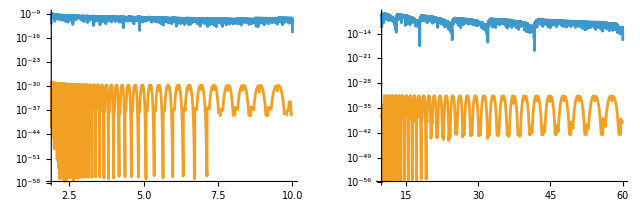

```mathematica
GraphicsRow[{
LogPlot[
Evaluate@{
Abs[testeq/.h0->oldinh],
Abs[testeq/.h0->newinsol[[1]]]
},{r,rhor+10^-1,10},WorkingPrecision->32],
LogPlot[
Evaluate@{
Abs[testeq/.h0->olduph],
Abs[testeq/.h0->newupsol[[1]]]
},{r,10,rmax},WorkingPrecision->32]
}
]
```

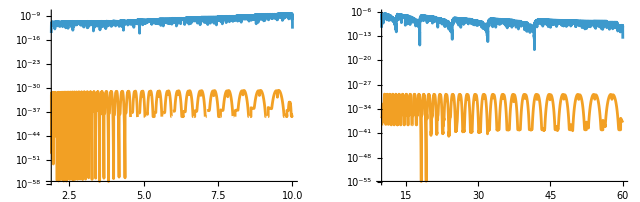

```mathematica
GraphicsRow[{
LogPlot[
Evaluate@{
Abs[(testeq/.h0->oldinκ)-(a^2 MetricReconstructRadiative`Private`γllsubs[[3,2]]+r^2)/2 oldinh[r]],
Abs[(testeq/.h0->newinsol[[2]])-(a^2 MetricReconstructRadiative`Private`γllsubs[[3,2]]+r^2)/2 newinsol[[1]][r]]
},{r,rhor+10^-1,10},WorkingPrecision->32],
LogPlot[
Evaluate@{
Abs[(testeq/.h0->oldupκ)-(a^2 MetricReconstructRadiative`Private`γllsubs[[3,2]]+r^2)/2 olduph[r]],
Abs[(testeq/.h0->newupsol[[2]])-(a^2 MetricReconstructRadiative`Private`γllsubs[[3,2]]+r^2)/2 newupsol[[1]][r]]

},{r,10,rmax},WorkingPrecision->32]
}
]
```

```mathematica
Re@newinsol[[2]][10]
```

-5.7427428108554434110818601160789784671091817997297215685934869970791962623213878872508861680780275

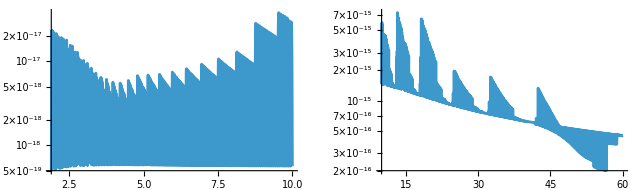

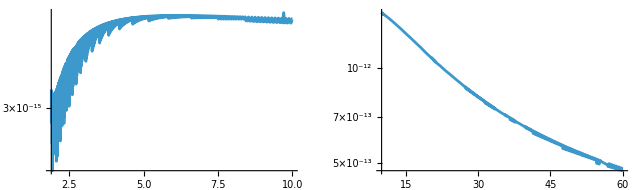

```mathematica
GraphicsRow[
{LogPlot[{
Abs[oldinκ[r]/(newinsol[[2]][r])-1]
},{r,rhor+10^-1,10},PlotRange->All,WorkingPrecision->32],
LogPlot[{
Abs[oldupκ[r]/newupsol[[2]][r]-1]
},{r,10,rmax},PlotRange->All,WorkingPrecision->32]
}
]
```

```mathematica
GraphicsRow[{LogPlot[{
Abs[oldinh[r]/(newinsol[[1]][r])-1],
Abs[oldinhp[r]/(newinsol[[1]]'[r])-1](*,
Abs[oldinκ[r]/(newinsol[[2]][r])-1]*)
},{r,rhor+10^-1,10},PlotRange->All,WorkingPrecision->32],
LogPlot[{
Abs[oldinh[r]/(newinsol[[1]][r])-1],
Abs[oldinhp[r]/(newinsol[[1]]'[r])-1](*,
Abs[oldinκ[r]/(newinsol[[2]][r])-1]*)
},{r,rhor+10^-1,10},PlotRange->All,WorkingPrecision->32]
}
]
```

$Aborted

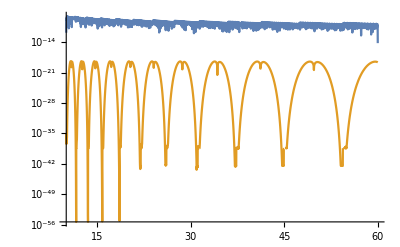

```mathematica
LogPlot[
Evaluate@{
Abs[testeq/.h0->olduph],
Abs[testeq/.h0->newupsol[[1]]]
},{r,10,rmax},WorkingPrecision->32]
```

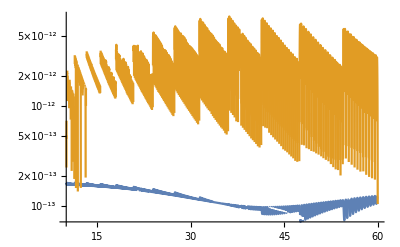

```mathematica
LogPlot[{
Abs[olduph[r]/(newupsol[[1]][r])-1],
Abs[olduphp[r]/(newupsol[[1]]'[r])-1]
},{r,10,rmax},PlotRange->All,WorkingPrecision->32]
```

```mathematica
κ2bla[[3;;3]]+γll a^2 κ0bla[[3;;3]]
```

(0.40661099828613560132638282627-0.496347793223123464532060142945 ⅈ)+x ((-0.0015909867776858615564659552-0.156899319882791005924843863 ⅈ)+(0.0236030747348185911200596796-0.169514756673076272634736596 ⅈ) λ0)+x^2 ((-0.0033687059632641206605+0.0244586683520905730841 ⅈ)-(0.0225256471903201848223-0.0114085638617072040126 ⅈ) λ0-(0.00405491146333760721173+0.0160078511662848523514 ⅈ) λ0^2)+x^3 ((0.0014398623633073509-0.01451717721315283761 ⅈ)+(0.007872963257574663749-0.005401562635986604335 ⅈ) λ0-(0.00042520192523578794-0.005761745503763939219 ⅈ) λ0^2-(0.0004259594402726228422+0.0007037506659497306876 ⅈ) λ0^3)+x^4 ((-0.001896283046457909+0.0081528556615776831 ⅈ)-(0.00402078803155401-0.001553936916151675 ⅈ) λ0+(0.000366636348624174-0.0027633290344275149 ⅈ) λ0^2+(0.000165176840035143+0.0004440213549392215 ⅈ) λ0^3-(0.00001762959504738922+0.00001768813850756818 ⅈ) λ0^4)+x^5 ((0.00156821163449543-0.00443552376165195 ⅈ)+(0.00201873739372243-0.00015677936528579 ⅈ) λ0-(0.00029119070844441-0.00136313931730275 ⅈ) λ0^2-(0.0000768819270929092+0.000262525680738027 ⅈ) λ0^3+(0.0000120560382044879+0.0000158951436211806 ⅈ) λ0^4-(4.24676781606581×10^-7+2.821027864329×10^-7 ⅈ) λ0^5)+x^6 ((-0.001102001023906+0.00240883657754686 ⅈ)-(0.00100092979240458+0.00021939637679068 ⅈ) λ0+(0.00020108130692967-0.000671282744212122 ⅈ) λ0^2+(0.000035267793693347+0.000151402513664746 ⅈ) λ0^3-(7.4215305318777×10^-6+0.00001130149468625 ⅈ) λ0^4+(3.99566273787058×10^-7+3.3152723827369×10^-7 ⅈ) λ0^5-(6.84354274129567×10^-9+3.0045474578541×10^-9 ⅈ) λ0^6)+0.36 γll ((0.125497221693251728804439143911-0.15319376334047020510248769844 ⅈ)+x ((-0.06373625770066193524278567528-0.0098241757960943728306305494 ⅈ)+(0.00728489960951191083952459247-0.05231936934354205945516561604 ⅈ) λ0)+x^2 ((0.01957200067983516470035+0.01715104994525775310296 ⅈ)-(0.01396608286253464470227-0.02087620141426620996081 ⅈ) λ0-(0.00125151588374617506535+0.004940694804408905046729 ⅈ) λ0^2)+x^3 ((-0.005560356069673706826-0.010689892345164182751 ⅈ)+(0.0087027916675750972938-0.0072076701632939332974 ⅈ) λ0-(0.0000202550624601841251-0.0035577825352301264479 ⅈ) λ0^2-(0.00013146896304710581549+0.00021720699566349712582 ⅈ) λ0^3)+x^4 ((0.0012614144971185118+0.00593329058993547556 ⅈ)-(0.00465630193524974517-0.00236976801473404061 ⅈ) λ0+(0.00034832722553225472-0.00199659877603647455 ⅈ) λ0^2+(0.00008532560626359708+0.000218892478042430851 ⅈ) λ0^3-(5.44123303931766118×10^-6+5.45930200850869684×10^-6 ⅈ) λ0^4)+x^5 ((-8.2864381428103×10^-6-0.00320858647027407 ⅈ)+(0.002400968058919903-0.0006926017970833774 ⅈ) λ0-(0.0003198119750234743-0.001050888927323953 ⅈ) λ0^2-(0.00004042235188234858+0.0001567250027056095 ⅈ) λ0^3+(5.384630297006975×10^-6+7.035918783541232×10^-6 ⅈ) λ0^4-(1.310730807427718×10^-7+8.706876124472225×10^-8 ⅈ) λ0^5)+x^6 ((-0.00028198602688062+0.001728414803077259 ⅈ)-(0.001227087892328607-0.000131322447100687 ⅈ) λ0+(0.0002252884099279301-0.0005426809044042543 ⅈ) λ0^2+(0.0000164344890598867+0.00009944773718352805 ⅈ) λ0^3-(3.775230973004986×10^-6+6.038335307043539×10^-6 ⅈ) λ0^4+(1.661010597129827×10^-7+1.375060700282025×10^-7 ⅈ) λ0^5-(2.112204549782616×10^-9+9.273294623006489×10^-10 ⅈ) λ0^6))

```mathematica
κbla2[[1;;2]]
```

(0.996773666633451208380848703752291586747712066131+0.080263674885376866719497522738421064691539015562 ⅈ) (0.+x)^(0.61034723029532924858954202562975437755854109352 ⅈ)

```mathematica
κ2bla[[1;;2]]
```

(0.996773666633451208380848703752292+0.0802636748853768667194975227384 ⅈ) x^(1+0.6103472302953292485895420256298 ⅈ)

```mathematica
Collect[1-κbla2[[1;;2]]/(κ2bla[[1;;2]]/x),x,Together]//Simplify//Chop
```

0.

```mathematica
Collect[1-κbla2[[1;;2]]/(κ0bla[[1;;2]]/x),x,Together]//Simplify//Chop
```

0.

```mathematica
κ0bla[[3]]
```

```mathematica
CoefficientList[Collect[κ0bla[[3]],x,Chop],x]//TableForm
CoefficientList[Collect[κ2bla[[3]],x,Chop],x]//TableForm
```

0.125497221693251728804439143911-0.15319376334047020510248769844 ⅈ
(-0.06373625770066193524278567528-0.0098241757960943728306305494 ⅈ)+(0.00728489960951191083952459247-0.05231936934354205945516561604 ⅈ) λ0
(0.01957200067983516470035+0.01715104994525775310296 ⅈ)-(0.01396608286253464470227-0.02087620141426620996081 ⅈ) λ0-(0.00125151588374617506535+0.004940694804408905046729 ⅈ) λ0^2
(-0.005560356069673706826-0.010689892345164182751 ⅈ)+(0.0087027916675750972938-0.0072076701632939332974 ⅈ) λ0-(0.0000202550624601841251-0.0035577825352301264479 ⅈ) λ0^2-(0.00013146896304710581549+0.00021720699566349712582 ⅈ) λ0^3
(0.0012614144971185118+0.00593329058993547556 ⅈ)-(0.00465630193524974517-0.00236976801473404061 ⅈ) λ0+(0.00034832722553225472-0.00199659877603647455 ⅈ) λ0^2+(0.00008532560626359708+0.000218892478042430851 ⅈ) λ0^3-(5.44123303931766118×10^-6+5.45930200850869684×10^-6 ⅈ) λ0^4
(-8.2864381428103×10^-6-0.00320858647027407 ⅈ)+(0.002400968058919903-0.0006926017970833774 ⅈ) λ0-(0.0003198119750234743-0.001050888927323953 ⅈ) λ0^2-(0.00004042235188234858+0.0001567250027056095 ⅈ) λ0^3+(5.384630297006975×10^-6+7.035918783541232×10^-6 ⅈ) λ0^4-(1.310730807427718×10^-7+8.706876124472225×10^-8 ⅈ) λ0^5
(-0.00028198602688062+0.001728414803077259 ⅈ)-(0.001227087892328607-0.000131322447100687 ⅈ) λ0+(0.0002252884099279301-0.0005426809044042543 ⅈ) λ0^2+(0.0000164344890598867+0.00009944773718352805 ⅈ) λ0^3-(3.775230973004986×10^-6+6.038335307043539×10^-6 ⅈ) λ0^4+(1.661010597129827×10^-7+1.375060700282025×10^-7 ⅈ) λ0^5-(2.112204549782616×10^-9+9.273294623006489×10^-10 ⅈ) λ0^6

0.40661099828613560132638282627-0.496347793223123464532060142945 ⅈ
(-0.0015909867776858615564659552-0.156899319882791005924843863 ⅈ)+(0.0236030747348185911200596796-0.169514756673076272634736596 ⅈ) λ0
(-0.0033687059632641206605+0.0244586683520905730841 ⅈ)-(0.0225256471903201848223-0.0114085638617072040126 ⅈ) λ0-(0.00405491146333760721173+0.0160078511662848523514 ⅈ) λ0^2
(0.0014398623633073509-0.01451717721315283761 ⅈ)+(0.007872963257574663749-0.005401562635986604335 ⅈ) λ0-(0.00042520192523578794-0.005761745503763939219 ⅈ) λ0^2-(0.0004259594402726228422+0.0007037506659497306876 ⅈ) λ0^3
(-0.001896283046457909+0.0081528556615776831 ⅈ)-(0.00402078803155401-0.001553936916151675 ⅈ) λ0+(0.000366636348624174-0.0027633290344275149 ⅈ) λ0^2+(0.000165176840035143+0.0004440213549392215 ⅈ) λ0^3-(0.00001762959504738922+0.00001768813850756818 ⅈ) λ0^4
(0.00156821163449543-0.00443552376165195 ⅈ)+(0.00201873739372243-0.00015677936528579 ⅈ) λ0-(0.00029119070844441-0.00136313931730275 ⅈ) λ0^2-(0.0000768819270929092+0.000262525680738027 ⅈ) λ0^3+(0.0000120560382044879+0.0000158951436211806 ⅈ) λ0^4-(4.24676781606581×10^-7+2.821027864329×10^-7 ⅈ) λ0^5
(-0.001102001023906+0.00240883657754686 ⅈ)-(0.00100092979240458+0.00021939637679068 ⅈ) λ0+(0.00020108130692967-0.000671282744212122 ⅈ) λ0^2+(0.000035267793693347+0.000151402513664746 ⅈ) λ0^3-(7.4215305318777×10^-6+0.00001130149468625 ⅈ) λ0^4+(3.99566273787058×10^-7+3.3152723827369×10^-7 ⅈ) λ0^5-(6.84354274129567×10^-9+3.0045474578541×10^-9 ⅈ) λ0^6

```mathematica
CoefficientList[Collect[κbla2[[3]],x,Chop],x]
```

{0,(-0.15687152711656466100554892988827364935937360552+0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))),(-0.07115086394877041966324987247231273598344489892+0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))),(-0.037237508455521992270324239107279616455642050624+0.015151873432617834385193225419943999136805390932 ⅈ) (-2.6-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-5.4-0.18 (-5+γll)) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0)),(-0.022334069698120654342503680913261758795840326795+0.0068157687907353908028135127304194493419042687538 ⅈ) (-1/2-(0.004351216486735131421371482030667699374242420199-0.005311505862188321404395920355622057854654031143 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll)))+(0.40786597050306811861442721770951148833437137436-0.49787973085652816658308501992921060291460550675 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) ((33.3526178931042594852670634733862245975471789541+11.718666821670321572919206892091284049123988996 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) (-2.6-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-5.4-0.18 (-5+γll)) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (0.027737452211464255761241729779557154195159853145-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))) ((5.55617817031127143691055220769194867742760800987+3.0517361514766462429477101281487718877927054676 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0)),(-0.01474607775093466068530004639184186325306270554+0.0036000910852010192488357128875347502833531072136 ⅈ) ((-0.0006043356231576571418571502820371804686447805831+0.0007377091475261557506105444938363969242575043254 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll)))-(0.001973543688583414466125351209505307711470489512-0.001204546924193714817949509866888119001395014374 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)))+(0.078435763558282330502774464944136824679686802761-0.095746102087793878189054811524848192868193366682 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.022334069698120654342503680913261758795840326795-0.0068157687907353908028135127304194493419042687538 ⅈ) ((57.3526178931042594852670634733862245975471789541+15.624889095560428763892275856121712065498651994 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) (-1/2-(0.004351216486735131421371482030667699374242420199-0.005311505862188321404395920355622057854654031143 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll)))+(0.40786597050306811861442721770951148833437137436-0.49787973085652816658308501992921060291460550675 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) ((33.3526178931042594852670634733862245975471789541+11.718666821670321572919206892091284049123988996 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) (-2.6-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-5.4-0.18 (-5+γll)) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (0.027737452211464255761241729779557154195159853145-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))) ((5.55617817031127143691055220769194867742760800987+3.0517361514766462429477101281487718877927054676 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) (-5.4-0.18 (-5+γll)) (0.027737452211464255761241729779557154195159853145-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.022334069698120654342503680913261758795840326795-0.0068157687907353908028135127304194493419042687538 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (0.0038524239182589244112835735804940491937722018257-(0.004351216486735131421371482030667699374242420199-0.005311505862188321404395920355622057854654031143 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) ((33.3526178931042594852670634733862245975471789541+11.718666821670321572919206892091284049123988996 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) (0.027737452211464255761241729779557154195159853145-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((5.55617817031127143691055220769194867742760800987+3.0517361514766462429477101281487718877927054676 ⅈ)-λ0) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) (-2.6-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-5.4-0.18 (-5+γll)) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0)) ((11.5561781703112714369105522076919486774276080099+4.2724306120673047401267941794082806429097876547 ⅈ)-λ0)+(0.18499224626680309112444966842801311355695673719-0.11290950513505472870811190825524491477253295923 ⅈ) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0)),(-0.010419418791898075952999690340002538000009854318+0.0021198211336406987409313279047283030134567832413 ⅈ) ((-0.0002741032900810297869618543346535149599264568766+0.0001672981839157937247152097037344609724159742186 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)))-(0.01474607775093466068530004639184186325306270554-0.0036000910852010192488357128875347502833531072136 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((-0.0006043356231576571418571502820371804686447805831+0.0007377091475261557506105444938363969242575043254 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.022334069698120654342503680913261758795840326795-0.0068157687907353908028135127304194493419042687538 ⅈ) ((57.3526178931042594852670634733862245975471789541+15.624889095560428763892275856121712065498651994 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) (0.0038524239182589244112835735804940491937722018257-(0.004351216486735131421371482030667699374242420199-0.005311505862188321404395920355622057854654031143 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) ((33.3526178931042594852670634733862245975471789541+11.718666821670321572919206892091284049123988996 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) (0.027737452211464255761241729779557154195159853145-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((5.55617817031127143691055220769194867742760800987+3.0517361514766462429477101281487718877927054676 ⅈ)-λ0) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) (0.027737452211464255761241729779557154195159853145-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0)) ((11.5561781703112714369105522076919486774276080099+4.2724306120673047401267941794082806429097876547 ⅈ)-λ0)-(0.001973543688583414466125351209505307711470489512-0.001204546924193714817949509866888119001395014374 ⅈ) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.01474607775093466068530004639184186325306270554-0.0036000910852010192488357128875347502833531072136 ⅈ) ((87.7526178931042594852670634733862245975471789541+19.531111369450535954865344820152140081873314993 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.0006043356231576571418571502820371804686447805831+0.0007377091475261557506105444938363969242575043254 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll)))-(0.001973543688583414466125351209505307711470489512-0.001204546924193714817949509866888119001395014374 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)))+(0.078435763558282330502774464944136824679686802761-0.095746102087793878189054811524848192868193366682 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.022334069698120654342503680913261758795840326795-0.0068157687907353908028135127304194493419042687538 ⅈ) ((57.3526178931042594852670634733862245975471789541+15.624889095560428763892275856121712065498651994 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) (-1/2-(0.004351216486735131421371482030667699374242420199-0.005311505862188321404395920355622057854654031143 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll)))+(0.40786597050306811861442721770951148833437137436-0.49787973085652816658308501992921060291460550675 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) ((33.3526178931042594852670634733862245975471789541+11.718666821670321572919206892091284049123988996 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) (-2.6-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-5.4-0.18 (-5+γll)) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (0.027737452211464255761241729779557154195159853145-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))) ((5.55617817031127143691055220769194867742760800987+3.0517361514766462429477101281487718877927054676 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) (-5.4-0.18 (-5+γll)) (0.027737452211464255761241729779557154195159853145-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.022334069698120654342503680913261758795840326795-0.0068157687907353908028135127304194493419042687538 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (0.0038524239182589244112835735804940491937722018257-(0.004351216486735131421371482030667699374242420199-0.005311505862188321404395920355622057854654031143 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) ((33.3526178931042594852670634733862245975471789541+11.718666821670321572919206892091284049123988996 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) (0.027737452211464255761241729779557154195159853145-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((5.55617817031127143691055220769194867742760800987+3.0517361514766462429477101281487718877927054676 ⅈ)-λ0) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) (-2.6-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-5.4-0.18 (-5+γll)) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0)) ((11.5561781703112714369105522076919486774276080099+4.2724306120673047401267941794082806429097876547 ⅈ)-λ0)+(0.18499224626680309112444966842801311355695673719-0.11290950513505472870811190825524491477253295923 ⅈ) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.0010328736112590374074923936875970121575707164078-0.0004202743652513920544203079900360615406976509382 ⅈ) (-2.6-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-5.4-0.18 (-5+γll)) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))+(0.096817521984357179902843021678927002784669331623-0.039394870924806369401502386091854397755694016424 ⅈ) (0.027737452211464255761241729779557154195159853145-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.022334069698120654342503680913261758795840326795-0.0068157687907353908028135127304194493419042687538 ⅈ) (-5.4-0.18 (-5+γll)) (0.0038524239182589244112835735804940491937722018257-(0.004351216486735131421371482030667699374242420199-0.005311505862188321404395920355622057854654031143 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) ((33.3526178931042594852670634733862245975471789541+11.718666821670321572919206892091284049123988996 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) (0.027737452211464255761241729779557154195159853145-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((5.55617817031127143691055220769194867742760800987+3.0517361514766462429477101281487718877927054676 ⅈ)-λ0) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.022334069698120654342503680913261758795840326795-0.0068157687907353908028135127304194493419042687538 ⅈ) (-1/2-(0.004351216486735131421371482030667699374242420199-0.005311505862188321404395920355622057854654031143 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll)))+(0.40786597050306811861442721770951148833437137436-0.49787973085652816658308501992921060291460550675 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) ((33.3526178931042594852670634733862245975471789541+11.718666821670321572919206892091284049123988996 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) (-2.6-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-5.4-0.18 (-5+γll)) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.037237508455521992270324239107279616455642050624-0.015151873432617834385193225419943999136805390932 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (0.027737452211464255761241729779557154195159853145-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((1.5561781703112714369105522076919486774276080099+1.8310416908859877457686260768892631326756232806 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) ((15.7526178931042594852670634733862245975471789541+7.8124445477802143819461379280608560327493259971 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-1.28+0.8 (-2-0.36 (-1+γll))) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))) ((5.55617817031127143691055220769194867742760800987+3.0517361514766462429477101281487718877927054676 ⅈ)-λ0)-(0.07115086394877041966324987247231273598344489892-0.043426732744251818733889195482786505681743445857 ⅈ) (-5.4-0.18 (-5+γll)) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0)) ((19.5561781703112714369105522076919486774276080099+5.4931250726579632373058782306677893980268698417 ⅈ)-λ0)+(0.03557543197438520983162493623615636799172244946-0.021713366372125909366944597741393252840871722928 ⅈ) ((-0.44382182968872856308944779230805132257239199013+0.61034723029532924858954202562975437755854109352 ⅈ)-(0.15687152711656466100554892988827364935937360552-0.19149220417558775637810962304969638573638673336 ⅈ) (-0.24738210689574051473293652661377540245282104586+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0)) ((4.55261789310425948526706347338622459754717895414+3.9062222738901071909730689640304280163746629986 ⅈ)+1.6 ((-0.86319104606393676164709217674274165114994537636+0.61034723029532924858954202562975437755854109352 ⅈ)-λ0))-λ0))}

```mathematica
Collect[κbla2[[3]]/.{γll->1,λ0-> MetricReconstructRadiative`Private`testeigs0[[3]]},x]//Chop
```

(0.4517899980957062236959809180782281101549959839-0.5514975480256927383689557143831255909207937921 ⅈ) x+(0.12894231898689787192553911024-1.26270116846307104189156629452 ⅈ) x^2-(0.31187708111598298715253042788+0.46778127424057454436879830277 ⅈ) x^3-(0.04582601222536736403879624648-0.0193097240437257471993205768 ⅈ) x^4-(0.0016446039113270707444569938+0.0131449114141178110129467137 ⅈ) x^5-(0.00062844875751515817643684901-0.00721240292557377378097279374 ⅈ) x^6+(0.00082104509981440630619944538-0.0034609485043279028963428656 ⅈ) x^7

```mathematica
Collect[x κ2bla[[3]]+x γll a^2 κ0bla[[3]]/.{γll->1,λ0-> MetricReconstructRadiative`Private`testeigs0[[3]]},{x},Together]//Chop
```

(0.451789998095706223695980918078-0.551497548025692738368955714383 ⅈ) x+(0.12894231898689787192553911-1.262701168463071041891566295 ⅈ) x^2-(0.311877081115982987153+0.467781274240574544369 ⅈ) x^3-(0.045826012225367364-0.019309724043725747 ⅈ) x^4-(0.0016446039113271+0.0131449114141178 ⅈ) x^5-(0.0006284487575152-0.0072124029255738 ⅈ) x^6+(0.0008210450998144-0.003460948504328 ⅈ) x^7

```mathematica
Collect[κbla2[[3]]-x κ2bla[[3]]-x γll a^2 κ0bla[[3]],{x,γll,λ0},Abs]
```

0.+0. λ0+0. λ0^2+0. λ0^3+0. λ0^4+0. λ0^5+0. λ0^6+γll (0.+0. λ0+0. λ0^2+0. λ0^3+0. λ0^4+0. λ0^5+0. λ0^6)+x (3.×10^-41+0. λ0+0. λ0^2+0. λ0^3+0. λ0^4+0. λ0^5+0. λ0^6+γll (3.×10^-42+0. λ0+0. λ0^2+0. λ0^3+0. λ0^4+0. λ0^5+0. λ0^6))+x^2 (2.×10^-40+2.×10^-41 λ0+0. λ0^2+0. λ0^3+0. λ0^4+0. λ0^5+0. λ0^6+γll (3.×10^-41+2.×10^-42 λ0+0. λ0^2+0. λ0^3+0. λ0^4+0. λ0^5+0. λ0^6))+x^3 (2.×10^-37+1.×10^-37 λ0+4.×10^-39 λ0^2+0. λ0^3+0. λ0^4+0. λ0^5+0. λ0^6+γll (3.×10^-37+4.×10^-37 λ0+0. λ0^2+0. λ0^3+0. λ0^4+0. λ0^5+0. λ0^6))+x^4 (9.×10^-36+3.×10^-36 λ0+5.×10^-36 λ0^2+0. λ0^3+0. λ0^4+0. λ0^5+0. λ0^6+γll (8.×10^-35+8.×10^-35 λ0+3.×10^-35 λ0^2+0. λ0^3+0. λ0^4+0. λ0^5+0. λ0^6))+x^5 (9.×10^-25+2.×10^-24 λ0+1.×10^-24 λ0^2+1.×10^-24 λ0^3+6.×10^-30 λ0^4+0. λ0^5+0. λ0^6+γll (2.×10^-25+2.×10^-25 λ0+2.×10^-25 λ0^2+9.×10^-26 λ0^3+7.×10^-32 λ0^4+0. λ0^5+0. λ0^6))+x^6 (8.×10^-25+1.×10^-24 λ0+1.×10^-24 λ0^2+1.×10^-24 λ0^3+4.×10^-26 λ0^4+2.×10^-32 λ0^5+0. λ0^6+γll (2.×10^-25+2.×10^-25 λ0+2.×10^-25 λ0^2+9.×10^-26 λ0^3+5.×10^-27 λ0^4+6.×10^-34 λ0^5+0. λ0^6))+x^7 (6.×10^-25+1.×10^-24 λ0+8.×10^-25 λ0^2+9.×10^-25 λ0^3+5.×10^-26 λ0^4+6.×10^-28 λ0^5+2.×10^-34 λ0^6+γll (1.×10^-25+1.×10^-25 λ0+1.×10^-25 λ0^2+7.×10^-26 λ0^3+6.×10^-27 λ0^4+7.×10^-29 λ0^5+8.×10^-36 λ0^6))

```mathematica
Out[98]//Length
```

2

```mathematica
Collect[Simplify[κbla2/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r]))-κ2bla/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r]))-(γll a^2 κ0bla)/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r])),r>0],r]
```

1/(1290240 r^7 ω^7)ⅈ a^2 γll (7 λ0^6+140 λ0^4 (166-3 (21 ⅈ+16 a m) ω+(140-6 ⅈ a m+a^2 (13+3 m^2)) ω^2-6 ⅈ (-4+a^2-4 ⅈ a m) ω^3+48 ω^4)-32 λ0^3 (11160-35 (357 ⅈ+166 a m) ω+7 (1708+105 ⅈ a m+a^2 (297+115 m^2)) ω^2-35 (84 ⅈ+132 a m-6 ⅈ a^2 (-4+m^2)+a^3 m (13+m^2)) ω^3+70 (80-24 ⅈ a m+3 ⅈ a^3 m+6 a^2 (5+m^2)) ω^4-840 ⅈ (-4+a^2-2 ⅈ a m) ω^5+2240 ω^6)+48 λ0^2 (50553-3 (38269 ⅈ+14880 a m) ω+(34701+32046 ⅈ a m+a^2 (16193+10808 m^2)) ω^2-28 (2688 ⅈ+1758 a m-3 ⅈ a^2 (-221+15 m^2)+a^3 m (297+35 m^2)) ω^3+7 (6896-480 ⅈ a m-60 ⅈ a^3 m (-3+m^2)+44 a^2 (64+25 m^2)+a^4 (217+130 m^2+5 m^4)) ω^4-140 ⅈ (48-104 ⅈ a m+3 a^4 (4+m^2)-2 ⅈ a^3 m (33+2 m^2)-12 a^2 (1+3 m^2)) ω^5-140 (16+3 a^4+144 ⅈ a m-24 ⅈ a^3 m-8 a^2 (20+3 m^2)) ω^6-2240 ⅈ (-12+3 a^2-4 ⅈ a m) ω^7+8960 ω^8)-64 λ0 (97200-9 (43757 ⅈ+16851 a m) ω+3 (-50790+84105 ⅈ a m+a^2 (17095+20201 m^2)) ω^2-(369516 ⅈ+170331 a m+84 ⅈ a^2 (1565+247 m^2)+a^3 m (48579+9184 m^2)) ω^3+2 (20622+57876 ⅈ a m-84 ⅈ a^3 m (-183+20 m^2)+14 a^2 (1877+2230 m^2)+a^4 (4691+5740 m^2+315 m^4)) ω^4-7 (18720 ⅈ+18800 a m-48 ⅈ a^2 (-253+60 m^2)+a^3 (8224 m+740 m^3)+a^5 m (651+130 m^2+3 m^4)-12 ⅈ a^4 (-97+20 m^2+5 m^4)) ω^5+28 (4112+15 ⅈ a^5 m (12+m^2)-120 ⅈ a^3 m (11+2 m^2)+12 a^2 (68+5 m^2)+5 a^4 (175+108 m^2+3 m^4)) ω^6+420 (-256 ⅈ+176 a m+3 a^5 m+96 ⅈ a^2 (3+m^2)-8 a^3 m (23+m^2)-4 ⅈ a^4 (14+3 m^2)) ω^7-560 (272+9 a^4+192 ⅈ a m-36 ⅈ a^3 m-8 a^2 (28+3 m^2)) ω^8-26880 ⅈ (-4+a^2-ⅈ a m) ω^9+21504 ω^10)+64 (56700-4320 (98 ⅈ+45 a m) ω+9 (-64503+66514 ⅈ a m+3 a^2 (2260+4897 m^2)) ω^2-3 (115059 ⅈ+5376 a m+2 a^3 m (17095+5321 m^2)+7 ⅈ a^2 (13702+6917 m^2)) ω^3+(-343476+503958 ⅈ a m-42 ⅈ a^3 m (-4148+9 m^2)+21 a^2 (-4123+8069 m^2)+a^4 (17131+42403 m^2+3444 m^4)) ω^4-(319704 ⅈ+226296 a m+308 a^3 m (468+89 m^2)+42 ⅈ a^2 (7009+514 m^2)+4 a^5 m (4691+1582 m^2+49 m^4)-21 ⅈ a^4 (-2333-342 m^2+105 m^4)) ω^5+(17808+70560 ⅈ a m-168 ⅈ a^3 m (-427+85 m^2)+112 a^2 (953+801 m^2)-42 ⅈ a^5 m (-79+90 m^2+5 m^4)+28 a^4 (645+1376 m^2+30 m^4)+a^6 (3429+4557 m^2+455 m^4+7 m^6)) ω^6+14 (6240 ⅈ-20256 a m-720 ⅈ a^2 (29+4 m^2)+16 a^3 m (357+80 m^2)-4 a^5 m (1085+195 m^2+3 m^4)-3 ⅈ a^6 (179+120 m^2+5 m^4)+6 ⅈ a^4 (643+890 m^2+50 m^4)) ω^7-28 (-20416-15840 ⅈ a m+15 a^6 (11+3 m^2)-30 ⅈ a^5 m (59+4 m^2)+240 ⅈ a^3 m (62+5 m^2)+32 a^2 (593+190 m^2)-4 a^4 (1724+780 m^2+15 m^4)) ω^8+280 (-2784 ⅈ+3 ⅈ a^6+1920 a m+36 a^5 m-16 a^3 m (65+2 m^2)-12 ⅈ a^4 (35+6 m^2)+48 ⅈ a^2 (53+10 m^2)) ω^9-448 (1312+45 a^4+600 ⅈ a m-120 ⅈ a^3 m-60 a^2 (13+m^2)) ω^10-10752 ⅈ (-20+5 a^2-4 ⅈ a m) ω^11+28672 ω^12)+84 λ0^5 (a m ω-4 (2+ω^2)))+1/(1290240 r^6 ω^8)(3 λ0^7+21 λ0^6 (-11+2 a m ω-8 ω^2)+42 λ0^5 (157-66 (ⅈ+a m) ω+2 (100-4 ⅈ a m+a^2 (8+3 m^2)) ω^2-8 ⅈ (-4+a^2-6 ⅈ a m) ω^3+96 ω^4)-4 λ0^4 (22125-105 (249 ⅈ+157 a m) ω+14 (2724+225 ⅈ a m+8 a^2 (47+30 m^2)) ω^2-210 (60 ⅈ+96 a m+a^3 m (8+m^2)-2 ⅈ a^2 (-5+2 m^2)) ω^3+840 (32-8 ⅈ a m+ⅈ a^3 m+3 a^2 (3+m^2)) ω^4-3360 ⅈ (-4+a^2-3 ⅈ a m) ω^5+13440 ω^6)+8 λ0^3 (73053-12 (13881 ⅈ+7375 a m) ω+2 (58379+37422 ⅈ a m+4 a^2 (3848+3941 m^2)) ω^2-56 (3726 ⅈ+2754 a m-3 ⅈ a^2 (-187+5 m^2)+a^3 m (376+75 m^2)) ω^3+14 (11568+480 ⅈ a m-60 ⅈ a^3 m (-5+2 m^2)+516 a^2 (8+5 m^2)+a^4 (221+240 m^2+15 m^4)) ω^4-1680 ⅈ (24-52 ⅈ a m+a^2 (2-12 m^2)+a^4 (2+m^2)-ⅈ a^3 m (19+2 m^2)) ω^5-840 (-48+a^4+96 ⅈ a m-16 ⅈ a^3 m-8 a^2 (11+3 m^2)) ω^6-26880 ⅈ (-4+a^2-2 ⅈ a m) ω^7+53760 ω^8)-16 λ0^2 (110700-9 (48097 ⅈ+24351 a m) ω+(-14741+397992 ⅈ a m+a^2 (82184+126241 m^2)) ω^2-6 (136724 ⅈ+69503 a m+14 ⅈ a^2 (2037+803 m^2)+2 a^3 m (7696+2387 m^2)) ω^3+(115752+399168 ⅈ a m-84 ⅈ a^3 m (-744+85 m^2)+420 a^2 (386+507 m^2)+a^4 (16931+30450 m^2+2835 m^4)) ω^4-42 (12320 ⅈ+11360 a m-8 ⅈ a^2 (-587+135 m^2)+a^3 (4084 m+700 m^3)+a^5 m (221+80 m^2+3 m^4)-2 ⅈ a^4 (-148+5 m^2+20 m^4)) ω^5+84 (3984-240 ⅈ a m+20 ⅈ a^5 m (6+m^2)-80 ⅈ a^3 m (7+4 m^2)+16 a^2 (127+60 m^2)+15 a^4 (35+40 m^2+2 m^4)) ω^6+840 (-224 ⅈ+48 a m+3 a^5 m-24 a^3 m (12+m^2)-4 ⅈ a^4 (13+6 m^2)+24 ⅈ a^2 (9+8 m^2)) ω^7-3360 (88+3 a^4+128 ⅈ a m-24 ⅈ a^3 m-8 a^2 (14+3 m^2)) ω^8-53760 ⅈ (-8+2 a^2-3 ⅈ a m) ω^9+129024 ω^10)+32 λ0 (56700-540 (749 ⅈ+410 a m) ω+3 (-143849+238182 ⅈ a m+a^2 (30200+69313 m^2)) ω^2-2 (426321 ⅈ+100135 a m+21 ⅈ a^2 (8096+6883 m^2)+a^3 m (82184+37741 m^2)) ω^3+(-709800+1221192 ⅈ a m+84 ⅈ a^3 m (3125+192 m^2)+14 a^2 (4084+30399 m^2)+9 a^4 (3597+9826 m^2+1351 m^4)) ω^4-2 (461328 ⅈ+280728 a m+84 ⅈ a^2 (3749+1049 m^2)+28 a^3 m (6202+2067 m^2)-21 ⅈ a^4 (-1335-734 m^2+145 m^4)+a^5 m (16931+9394 m^2+483 m^4)) ω^5+2 (-3696+272160 ⅈ a m-168 ⅈ a^3 m (-579+170 m^2)+112 a^2 (934+1683 m^2)-84 ⅈ a^5 m (-104+30 m^2+5 m^4)+14 a^4 (2687+5676 m^2+360 m^4)+a^6 (2146+4641 m^2+840 m^4+21 m^6)) ω^6-168 ⅈ (2320-3408 ⅈ a m-8 ⅈ a^3 m (223+5 m^2)-40 a^2 (-56+15 m^2)+a^4 (149-640 m^2-100 m^4)+a^6 (34+60 m^2+5 m^4)-ⅈ a^5 m (545+210 m^2+6 m^4)) ω^7-56 (-9888-6720 ⅈ a m-120 ⅈ a^5 m (13+2 m^2)+15 a^6 (2+3 m^2)+480 ⅈ a^3 m (23+5 m^2)+32 a^2 (79+150 m^2)-12 a^4 (334+390 m^2+15 m^4)) ω^8+6720 (-152 ⅈ+168 a m+3 a^5 m+80 ⅈ a^2 (2+m^2)-4 a^3 m (31+2 m^2)-4 ⅈ a^4 (7+3 m^2)) ω^9-2688 (512+15 a^4+400 ⅈ a m-80 ⅈ a^3 m-60 a^2 (6+m^2)) ω^10-43008 ⅈ (-20+5 a^2-6 ⅈ a m) ω^11+172032 ω^12)+64 ω (56700 ⅈ+224460 ω-7707 ⅈ ω^2+473760 ω^3+54264 ⅈ ω^4+328832 ω^5+240576 ⅈ ω^6+26240 ω^7+123648 ⅈ ω^8-731136 ω^9+1849344 ⅈ ω^10+1720320 ω^11-688128 ⅈ ω^12-98304 ω^13+a m (56700-328860 ⅈ ω-219147 ω^2-683886 ⅈ ω^3-191744 ω^4-616224 ⅈ ω^5+249696 ω^6-303744 ⅈ ω^7+306432 ω^8-1451520 ⅈ ω^9-2021376 ω^10+1032192 ⅈ ω^11+172032 ω^12)+2 a^7 m ω^6 (2146+3 m^6+84 m^4 (2-ⅈ ω)-2856 ⅈ ω-840 ω^2-7 m^2 (-221+240 ⅈ ω+60 ω^2))+2 a^6 ω^5 (-2267+2016 ⅈ ω-7400 ω^2+7392 ⅈ ω^3+1680 ω^4-21 m^6 (3+4 ⅈ ω+4 ω^2)+35 ⅈ m^4 (59 ⅈ-36 ω+132 ⅈ ω^2+48 ω^3)+7 m^2 (-1223+432 ⅈ ω-3360 ω^2+3120 ⅈ ω^3+720 ω^4))+a^5 m ω^4 (7 m^4 (265+222 ⅈ ω+120 ω^2+576 ⅈ ω^3+288 ω^4)+14 m^2 (1919+120 ⅈ ω+3288 ω^2+4080 ⅈ ω^3+6720 ω^4-1920 ⅈ ω^5)-3 (-10791+14406 ⅈ ω-29196 ω^2+6328 ⅈ ω^3-75936 ω^4+62720 ⅈ ω^5+13440 ω^6))+a^4 ω^3 (-17900+69279 ⅈ ω-24668 ω^2+137340 ⅈ ω^3-75328 ω^4-4704 ⅈ ω^5-356608 ω^6+268800 ⅈ ω^7+53760 ω^8-21 m^4 (736+115 ⅈ ω+880 ω^2+840 ⅈ ω^3-640 ω^4+1920 ⅈ ω^5+640 ω^6)+2 ⅈ m^2 (39467 ⅈ+45024 ω+84462 ⅈ ω^2-13608 ω^3+58800 ⅈ ω^4-221760 ω^5+228480 ⅈ ω^6+53760 ω^7))+a^3 m ω^2 (m^2 (61833-56406 ⅈ ω+122906 ω^2+4200 ⅈ ω^3+55104 ω^4+33600 ⅈ ω^5-188160 ω^6+215040 ⅈ ω^7+53760 ω^8)-4 ⅈ (22650 ⅈ+69258 ω+32851 ⅈ ω^2+105672 ω^3+65120 ⅈ ω^4-15456 ω^5-52864 ⅈ ω^6-362880 ω^7+268800 ⅈ ω^8+53760 ω^9))+a^2 ω (m^2 (-104400+273273 ⅈ ω-169176 ω^2+364644 ⅈ ω^3-308392 ω^4+90048 ⅈ ω^5-74368 ω^6+295680 ⅈ ω^7+913920 ω^8-645120 ⅈ ω^9-129024 ω^10)+4 ⅈ (6300 ⅈ+44310 ω-39128 ⅈ ω^2+94941 ω^3-44982 ⅈ ω^4+82656 ω^5+23504 ⅈ ω^6+20160 ω^7-209664 ⅈ ω^8-430080 ω^9+247296 ⅈ ω^10+43008 ω^11))))

```mathematica
FreeQ[γll]@Out[133]
```

True

```mathematica
Series[Simplify[κbla2/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r]))-κ2bla/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r]))-(a^2 κ0bla)/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r])),r>0],{r,∞,1}]
```

O[1/r]^2

```mathematica
Series[Simplify[κ0bla/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r])),r>0],{r,∞,1}]
Series[Simplify[κ2bla/(2^(-2 ⅈ ω) ⅇ^(ⅈ r ω+(1-2 ⅈ ω) Log[1/r])),r>0],{r,∞,1}]
```

ⅈ/(4 ω r)+O[1/r]^2

-(ⅈ r)/(4 ω)-(ⅈ (5760 λ0^2 ω^4-11520 λ0 (ω^4-2 a m ω^5+8 ω^6)+64 ω (-360 ⅈ ω^4-2880 ⅈ ω^6+5760 ω^7+360 a^2 ω (ω^4+m^2 ω^4+2 ⅈ ω^5)-360 a m (ω^4-2 ⅈ ω^5+8 ω^6))))/(184320 ω^7 r)+O[1/r]^2

```mathematica
Simplify[bla2/bla,r>0]
```

1

```mathematica
Series[Simplify[bla2/bla,r>0],{r, ∞,3}]
```

1

```mathematica
(1-0.1264911064067351732799557417773087413487822055730086730744`32. ⅈ)/(-1+0.12649110640673517327995574177730874134878220557300867307430019411170377754556`64. ⅈ)
```

-1.+2.×10^-58 ⅈ

```mathematica
CoefficientList[bla2[[3]],1/r]/CoefficientList[bla[[3]],1/r]
```

{1,1,1,1,1/1,1/(88/1+368+1/1),(5-(73 a^2)/9+(31 a^4)/180-(5 a^6)/16+342+32/3 ⅈ a^2 ω^5+128/15 a m ω^5-(256 ω^6)/45)/(1120+1/1-(16384 ⅈ ω^9)/1),(266/15+(373 a^2)/30+(226 a^4)/15+(11 a^6)/30-(149 ⅈ a m)/35-2057/63 ⅈ a^3 m-227/140 ⅈ a^5 m-381/560 ⅈ a^7 m-(133 a^2 m^2)/15+(76 a^4 m^2)/15-(53 a^6 m^2)/40-202/45 ⅈ a^3 m^3+1/30 ⅈ a^5 m^3-217/720 ⅈ a^7 m^3-(a^4 m^4)/12-(a^6 m^4)/3+517+4 ⅈ a^5 m ω^4-32 a^2 m^2 ω^4+16/3 a^4 m^2 ω^4-16/9 ⅈ a^3 m^3 ω^4+(64 λ0 ω^4)/3-16/3 a^2 λ0 ω^4+64/15 ⅈ a m λ0 ω^4-(1280 ⅈ ω^5)/9+3392/45 ⅈ a^2 ω^5-16/3 ⅈ a^4 ω^5+256/5 a m ω^5-32/3 a^3 m ω^5+64/15 ⅈ a^2 m^2 ω^5-128/45 ⅈ λ0 ω^5-(512 ω^6)/15+(128 a^2 ω^6)/15-256/45 ⅈ a m ω^6+(1024 ⅈ ω^7)/315)/((136 a^2)/(-14 ⅈ ω+2 ω (ⅈ-ⅈ (1-2 ⅈ ω)+2 ω))+(19 a^4)/(3 (-14 ⅈ ω+2 ω (ⅈ-ⅈ (1-2 ⅈ ω)+2 ω)))+3151+(131072 ⅈ ω^11)/(3 (-8 ⅈ ω+2 ω (ⅈ-ⅈ (1-2 ⅈ ω)+2 ω)) (-10 ⅈ ω+2 ω (ⅈ-ⅈ (1-2 ⅈ ω)+2 ω)) (-12 ⅈ ω+2 ω (ⅈ-ⅈ (1-2 ⅈ ω)+2 ω)) (-14 ⅈ ω+2 ω (ⅈ-ⅈ (1-2 ⅈ ω)+2 ω))))}
 |  |  |  |

```mathematica
inford
```

7

```mathematica
Get["MetricReconstructRadiative`"]
```

Refactor attempt 2...

```mathematica
tab=Table[Abs[1/bla MetricReconstructRadiative`Private`hκinfSeries[2,6/10,(2.`64)/r0^(3/2),SetPrecision[MetricReconstructRadiative`Private`testeigs0[[3]],64],1,i][[1]][ 4000]-1],{i,1,10}]
```

{Abs[-1-((0.0002177675375381640020896237962631576511710904978816881835547048-0.0001228251068035507534240512768799917807049713294856259348678882 ⅈ) 2^(2 ⅈ ω) ⅇ^(-ⅈ r ω-(1-2 ⅈ ω) Log[1/r]))/(1+(ⅈ (λ0+2 a m ω-8 ω^2))/(2 r ω)+(2 λ0-λ0^2+4 a m ω-4 a m λ0 ω-4 a^2 ω^2-4 a^2 m^2 ω^2+16 λ0 ω^2+32 a m ω^3-64 ω^4-4 ⅈ (-ω-2 a m ω^2+8 ω^3-2 a^2 ω^3))/(8 r^2 ω^2)+(-12 (-2 ω+3 λ0 ω+11+64 1-16 a^2 ω^5)+1)/(48 r^3 ω^3)+1/(r^4 (1+1))+1/(r^5 (-10 ⅈ ω+2 ω (ⅈ-ⅈ (1-2 ⅈ ω)+2 ω)))+1/(r^6 (-12 ⅈ ω+2 ω (ⅈ-ⅈ (1-2 ⅈ ω)+2 ω)))+1/(r^7 (-14 ⅈ ω+2 ω (ⅈ-ⅈ (1-2 ⅈ ω)+2 ω))))],Abs[-1-((98-98 ⅈ) 2^1 ⅇ^1)/(1+6+1/(r^7 (1)))],6,Abs[-1-1/1],Abs[-1-1/(1+(ⅈ (1))/(2 r ω)+4+1/(r^6 (1))+1/(r^7 (-14 ⅈ ω+1)))]}
 |  |  |  |

```mathematica
ListLogPlot[tab]
```

-Graphics-

```mathematica
rinf
```

4000.

```mathematica
Max[2,1-6]
```

2

```mathematica
MetricReconstructRadiative`Private`hκinfSeries[2,a,(2.`32)/r0^(3/2),MetricReconstructRadiative`Private`testeigs0[[3]],1]
```

{Function[MetricReconstructRadiative`Private`r$,(0.9961588374988639381969535792227533-0.087564664522351650245864106833083 ⅈ) ⅇ^(0.063245553203367586639977870888654 ⅈ MetricReconstructRadiative`Private`r$) (19+(7.9056941504209483299972338610818 ⅈ (5.85222578986175772400543542861+64 (-64+1)))/(MetricReconstructRadiative`Private`r$)) (MetricReconstructRadiative`Private`r$)^(-1+0.12649110640673517327995574177731 ⅈ)],Function[MetricReconstructRadiative`Private`r$,1]}
 |  |  |  |

```mathematica
MetricReconstructRadiative`Private`hκinfSeries[2,a,(2.`32)/r0^(3/2),MetricReconstructRadiative`Private`testeigs0[[3]],1][[2]][ rinf]//RepeatedTiming
```

{0.00436627,(-0.000216288+0.000125378 ⅈ) ((0.-15811.4 ⅈ)+19)}
 |  |  |  |

```mathematica
Max[MetricReconstructRadiative`Private`MMm2gridL-
MetricReconstructRadiative`Private`Pm2ngridL/. NGrid[_,data_]:> Max@Abs@data]
Max[MetricReconstructRadiative`Private`MMm2gridR-
MetricReconstructRadiative`Private`Pm2ngridR/. NGrid[_,data_]:> Max@Abs@data]
```

1.513565×10^-14

1.2067803×10^-12

```mathematica
Max[MetricReconstructRadiative`Private`MMp2gridL-
MetricReconstructRadiative`Private`Pp2ngridL/. NGrid[_,data_]:> Max@Abs@data]
Max[MetricReconstructRadiative`Private`MMp2gridR-
MetricReconstructRadiative`Private`Pp2ngridR/. NGrid[_,data_]:> Max@Abs@data]
```

1.50827×10^-14

2.65381×10^-11

```mathematica
MetricReconstructRadiative`Private`Pm1ngridL
```

{{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]}}

```mathematica
MetricReconstructRadiative`Private`MMm1gridL
```

{{0,0,0},{0,0,0},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]}}

```mathematica
Max[MetricReconstructRadiative`Private`MMm1gridL-
MetricReconstructRadiative`Private`Pm1ngridL/. NGrid[_,data_]:> Max@Abs@data]
Max[MetricReconstructRadiative`Private`MMm1gridR-
MetricReconstructRadiative`Private`Pm1ngridR/. NGrid[_,data_]:> Max@Abs@data]
```

5.39696×10^-14

7.334014×10^-13

```mathematica
Max[MetricReconstructRadiative`Private`MMp1gridL-
MetricReconstructRadiative`Private`Pp1ngridL/. NGrid[_,data_]:> Max@Abs@data]
Max[MetricReconstructRadiative`Private`MMp1gridR-
MetricReconstructRadiative`Private`Pp1ngridR/. NGrid[_,data_]:> Max@Abs@data]
```

5.24491×10^-14

6.92805×10^-13

```mathematica
MetricReconstructRadiative`Private`MMp1gridL-
MetricReconstructRadiative`Private`Pp1ngridL/. NGrid[_,data_]:> Max@Abs@data
```

{{0,0,0},{0,0,0},{4.35022×10^-14,1.44393×10^-14,3.07308×10^-15},{3.11577×10^-14,1.46513×10^-14,4.4993×10^-15},{2.8066×10^-14,5.24491×10^-14,8.32942×10^-15},{1.8114×10^-14,1.3075×10^-14,6.6637×10^-15}}

```mathematica
MM=MSTMode[{-1,10,2,6/10,1/10},{MetricReconstructRadiative`Private`lNGrid,MetricReconstructRadiative`Private`rNGrid},Verbose->True]
```

Finding homogeneous MST solutions for s=-1 l=10 m=2 a=3/5 ω=1/10 mode.

ω=0.1

Spin weighted speroidal harmonic eigenvalue computed in:0.063 seconds. Value= 109.996

Renormalized angular momentum (ν) computed in:0.203 seconds. ν= 9.99642

Spin Weighted Spheroidal Harmonics computed in:0. seconds. Values (at zmax):

Asymptotic Homogeneous amplitudes computed in:0.594 seconds.

Exterior Homogeneous Solution computed in:0.297 seconds.

Interior Homogeneous Solution computed in:0.89 seconds.

MSTMode[{-1,10,2,3/5,1/10},…]

```mathematica
Get["Teukolsky`"]
```

```mathematica
TeukolskyRadial[-1,10,2,6/10,SetPrecision[1/10,32]]
```

<|In→TeukolskyRadialFunction[…],Up→TeukolskyRadialFunction[…]|>

## Solver tests

```mathematica
NGridData@MetricReconstructRadiative`Private`rNGrid;
```

```mathematica
MetricReconstructRadiative`Private`Pp2ngridR[[1]]
```

{NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>]}

```mathematica
Max[NGridData/@Abs@Flatten@MetricReconstructRadiative`Private`Pp2ngridR[[3]]]
```

Max[60.,1004,6.8155879348707948477537403134561260781489556142×10^-15 Abs[1]]
 |  |  |  |

```mathematica
MM=MSTMode[{-2,2,2,a,ω0},{MetricReconstructRadiative`Private`lNGrid,MetricReconstructRadiative`Private`rNGrid},"RadialDerivatives"-> 4]
```

MSTMode[{-2,2,2,0.6,0.062067897646520333960203544164553609973981736212},…]

```mathematica
{MetricReconstructRadiative`Private`Pm2j0[2],MetricReconstructRadiative`Private`Pm2j1[2]}/.MetricReconstructRadiative`Private`s2jumps
```

{-0.28181916444570151998509099373120087284223149-35.091377106631020926059939429863036867667153 ⅈ,-18.549293269606376705961641132011546538517956-7.6417559574802648864265961955516889212131706 ⅈ}

```mathematica
{testL,testR}=MetricReconstructRadiative`Private`ConstructSolution[{insols=MSTRhor[MM]/MSTAhor[MM],upsols=MSTRinf[MM]/MSTβinf[MM]},{MetricReconstructRadiative`Private`Pm2j0[2],MetricReconstructRadiative`Private`Pm2j1[2]}/.MetricReconstructRadiative`Private`s2jumps]
```

{{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>]}}

```mathematica
testR[[1,2,1]]-testL[[1,2,1]]
testR[[1,2,1]]-testL[[1,2,1]]
```

-0.28181916444570151998509099373120087284223-35.09137710663102092605993942986303686766715 ⅈ

-0.28181916444570151998509099373120087284223-35.09137710663102092605993942986303686766715 ⅈ

```mathematica
insols[[1,2,-1]]
uRhor[MM]/MSTAhor[MM]
```

0.0749045966392348000629923690643853239331819653-0.106755630820343904886735461731351605750359529 ⅈ

```mathematica
MetricReconstructRadiative`Private`γllsubs[[3]]
MetricReconstructRadiative`Private`testeigs0[[3]]
```

MetricReconstructRadiative`Private`γll[2]→0.142862534212397500581527651742

MetricReconstructRadiative`Private`eigs0

```mathematica
Get["MetricReconstructRadiative`"]
```

Refactor attempt 2...

```mathematica
MetricReconstructRadiative`Private`ConstructSolution[]
```

```mathematica
$TeukolskyPrecisionGoal=48
```

48

```mathematica
(SpinWeightedSphericalHarmonic[-1,2,2][0])/(√(2π))
SpinWeightedSphericalHarmonicY[-1,2,2,π/2,0]
```

(√(5/π))/4

(√(5/π))/4

```mathematica
accgoal
```

16

```mathematica
rhor
```

1.80010000000000000000479217360238593

```mathematica
With[
{ll=2,mm=2,
hκMode=MetricReconstructRadiative`Private`hκMode,
eigs0=MetricReconstructRadiative`Private`eigs0,
γmat=MetricReconstructRadiative`Private`γmat,
lNGrid=MetricReconstructRadiative`Private`lNGrid,
rNGrid=MetricReconstructRadiative`Private`rNGrid
},
hκMode[{mm,a,ω0,eigs0[[ll+1]],γmat[[ll+1,ll+1]]},{lNGrid,rNGrid},
"rinf"->rinf,"rhor"-> rhor,
PrecisionGoal->accgoal,
WorkingPrecision->prec,
MaxSteps-> (*OptionValue[MaxSteps]*)10^5,
Order-> (*OptionValue[Order]*)30
]
]
```

0.543608

0.987253

{{{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]}},{{NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>]},{NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>]}}}

```mathematica
test=MetricReconstructRadiative`Private`hκMode[{2,a,ω0,MetricReconstructRadiative`Private`eigs0[[3]],MetricReconstructRadiative`Private`γllsubs[[3,2]]},{MetricReconstructRadiative`Private`lNGrid,MetricReconstructRadiative`Private`rNGrid},"rinf"->4000,"rhor"-> 1+√(1-a^2)+10^-3,PrecisionGoal->32]
```

0.458619

1.18774

InterpolatingFunction::dprec: The precision of input value {10.00000000000000000000000000001} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

{{{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]}},{{NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>]},{NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>]}}}

```mathematica
1/Abs@MetricReconstructRadiative`Private`αs0hcos[[3]]
```

{2.5211107589250695851146,266.45815175326585955625}

```mathematica
test[[1,1]]
test[[1,2]]
test[[2,1]]
test[[2,2]]
```

{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]}

{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]}

{NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>]}

{NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>]}

```mathematica
NGridData@testL[[1]]
NGridData@testR[[1]]
```

{{10.,-35286.0917265627587818050796509107636593072+77948.2780416153150499105878934324198743352 ⅈ},{9.75,-30564.7871949875993831602278433986684794745+70102.22982192599166057952429000341380678905 ⅈ},{9.5,-26341.7210751931949869085782812464281979484+62824.23483464869051240599811696450595819477 ⅈ},{9.25,-22578.8665332266479576719369073437355059936+56092.31712586390023347389495209866936096751 ⅈ},{9.,-19239.9094463746739354302183338036160432884+49884.12168427207994896302682281443628251917 ⅈ},{8.75,-16290.2372880309834330589155666537465716876+44176.98875103501146441476646203011190950052 ⅈ},{8.5,-13696.9255994759754541060648760354684392792+38948.02730746439197092319866952674293745959 ⅈ},{8.25,-11428.7220786282683126587222884700932087598+34174.18767319350100663668278053322150048596 ⅈ},{8.,-9456.02831752102377413088032854774512444403+29832.33314840458402970202145716259038996304 ⅈ},{7.75,-7750.87922192001127115305030498274233178815+25899.3106346672353157674868668358501654242 ⅈ},{7.5,-6286.92014813170167792699634023798874935719+22352.02016997145533323381402372108451021976 ⅈ},{7.25,-5039.38179364413702187668681113719727273534+19167.48331461302128231608729122985742704856 ⅈ},{7.,-3985.05287979507729344919136087933142295095+16322.91032570794681189848084475825398656742 ⅈ},{6.75,-3102.25066616270916592487870776811676294651+13795.76605927629872338213308300419431710313 ⅈ},{6.5,-2370.78933781187306169645047127057125108979+11563.83454004187699037145864643500878382042 ⅈ},{6.25,-1771.94630788496551665091587610670535805796+9605.282140340198784313367673757235471900863 ⅈ},{6.,-1288.42647927286789739925397768846869092205+7898.719310807182242382204525559060360619987 ⅈ},{5.75,-904.324510191903727769343817755054002581722+6423.260806824439898635489071114646485251013 ⅈ},{5.5,-605.085129353342683948338618818845192471641+5158.584356004882456474738582685405450491085 ⅈ},{5.25,-377.461546916837931348163195738010654865866+4084.987713278588143531328626887442066770008 ⅈ},{5.,-209.4720073511421590556774547772239619166+3183.444051316116559591217824132227611609864 ⅈ},{4.75,-90.354529296695017923793975289829024142333+2435.655634974682353241986436097288666295527 ⅈ},{4.5,-10.51987481917069953321645860734908950082+1824.105728914461596514030889023750990099131 ⅈ},{4.25,38.49721531246745730578230709662647593932+1332.108686979559208531922281043766579108817 ⅈ},{4.,64.0884952456606117950903926958199126671454+943.8581692384881984472711920438079086846399 ⅈ},{3.75,72.624394629985838057957605196150920601505+644.4734251730354432155305671953315771833995 ⅈ},{3.5,69.5079518993740798116599336440276661741506+420.0435632228791507066723240849903109359311 ⅈ},{3.25,59.2306491129360435762555356574993373717392+257.6696816465650155363637422975567842317084 ⅈ},{3.,45.4305365839934542550149726428233137249503+145.5046171559914221153091892347375917745312 ⅈ},{2.75,30.953645960709409130666762444161382803521+72.78972497106136281413023029107150995914328 ⅈ},{2.5,17.9214591335963905249637058776691760601022+29.88695319144179554155228169135351549310169 ⅈ},{2.25,7.81334872407377965026493551581943241571392+8.29963365247443421130599670118626962736349 ⅈ},{2.,1.601419302021341401245549940580198954849421+0.645272294462481543414001046965598098249512 ⅈ}}

{{10.000000000000000000000000000000000000000000001,1.3196001375756398812604589468489980820072-34.44610481216853938264593838289743876941764 ⅈ},{10.25,0.71208305593530987759522658386437046314888-33.46142394078653257191975813950780387999223 ⅈ},{10.5,0.1423624731595869458216372464087648516772-32.50665705511151670187172857760451529463121 ⅈ},{10.75,-0.39250964990953105968982588597393528347066-31.57870671352635784745741508657973026371062 ⅈ},{11.,-0.89518295868623784462184538415084246767939-30.67472239309148137765459401466702829543031 ⅈ},{11.25,-1.3680500072585276710197141491950009857132-29.79207175305217185924943542256541720801571 ⅈ},{11.5,-1.8132813474345872145943905012018642079404-28.9283157741735738378995564873247857577294 ⅈ},{11.75,-2.2328554741853590095785346348733673167482-28.0811871965267225744277417482749729245643 ⅈ},{12.,-2.6285844918772950019537272151187775689866-27.2485717738405726281147116977120043607339 ⅈ},{12.25,-3.00213620350578612106719935755226905625727-26.4284919408604022146949820786098036790318 ⅈ},{12.5,-3.35505319630530401644985558876175751062499-25.6190925546121459468723133748573437454078 ⅈ},{12.75,-3.68876939419341165702735588523635458259761-24.8186284236965661658283877291826529088342 ⅈ},{13.,-4.00462446484875710787705933320945774059072-24.0254533838300662604838663120650882541259 ⅈ},{13.25,-4.30387640249972954182355398771995351888746-23.2380107144961520345307353874298108815828 ⅈ},{13.5,-4.58771255337646198102158807227346614272323-22.4548247221280391017643599804671811806831 ⅈ},{13.75,-4.85725930667060381242015386713690090815892-21.674493340801045067095789164674295663725 ⅈ},{14.,-5.11359063774120041310606954734110475779848-20.895681622856538973267732398156490844788 ⅈ},{14.25,-5.35773566062334288578585612927977391647412-20.1171160099238900324901449619987950109436 ⅈ},{14.5,-5.59068532239625571534848074206343604927757-19.3375792900361149929387450876283037639226 ⅈ},{14.75,-5.81339835166544318249170283924216501114614-18.5559061594246746548967121122872395299086 ⅈ},{15.,-6.02680655652697797343224612884469420374521-17.7709793185187639641414061526676478333136 ⅈ},{15.25,-6.23181955328579103453560047661782636807941-16.9817260409844757167012415522054842775547 ⅈ},{15.5,-6.42932899539214892120926110611285695349145-16.1871151625829842389056129430890368424583 ⅈ},{15.75,-6.62021236213697650086314433873757365047459-15.3861544434221574401078181928612059169638 ⅈ},{16.,-6.80533635828002444625537076980497526683515-14.5778882630031926438447419037505466655799 ⅈ},{16.25,-6.98555996870919665430712380387739899943119-13.7613956124729034595360926191971269815018 ⅈ},{16.5,-7.16173720622779456224323289846426520729333-12.9357883528080778811027463322007249198416 ⅈ},{16.75,-7.33471958546150872206309003532449820756881-12.100209711385247913744399890733459540813 ⅈ},{17.,-7.50535835152289703850085037134104463993038-11.2538329926146871940948503230337310293437 ⅈ},{17.25,-7.67450648834766726369301394388371381027841-10.3958604811149160502845856984651072382503 ⅈ},{17.5,-7.84302052842495994486613581191483779323687-9.52552251833527377729869397250573415150657 ⅈ},{17.75,-8.01176218290057484735208420746950014765278-8.64207673565140751900049305385234091582302 ⅈ},{18.,-8.1815998086691059147454703721076635012714-7.74480742880598856637922034863892719731523 ⅈ},{18.25,-8.35340972703099964606302315026477346686964-6.83302506018205674555810857462788072660399 ⅈ},{18.5,-8.52807740672571290581247596160487819415875-5.90606587681095414319411417351248077562809 ⅈ},{18.75,-8.706498522622200007783566398248560261595983-4.96329163325797102288260772636213259223715 ⅈ},{19.,-8.889579900019056353287859913338403560237389-4.00408940961975581309090577207762513000078 ⅈ},{19.25,-9.07824035335022367064262766490329569243709-3.02787151582806149249152571690616190924947 ⅈ},{19.5,-9.273411427084055480200582037980669268043601-2.03407547430151187319364999038884520105441 ⅈ},{19.75,-9.47603804572325690343513463771647250042343-1.02216407373538004763396723619050612475939 ⅈ},{20.,-9.687079079043327580487941909929232460944829+0.00837451251854625147398766965895369789017 ⅈ},{20.25,-9.9075078280328036645268601692245349541816+1.0580265494432326455883373025906091191864 ⅈ},{20.5,-10.1383124364071344237119650418430433378785+2.12725251015931578077559246758184318370871 ⅈ},{20.75,-10.3804962320485869348653407008699320303581+3.2164867975173650980128801361308384013843 ⅈ},{21.,-10.6350780022678378539336402052169883779588+4.32613742204520038739350909452198672814931 ⅈ},{21.25,-10.9030922063808803607982015317380609038304+5.4565856404487129983622919889685284136909 ⅈ},{21.5,-11.1855891287406524921953584540243354972302+6.60818555853676605592577104910823233881917 ⅈ},{21.75,-11.4836349750504292621525795273052579026662+7.78126370214762227659735116936738685848158 ⅈ},{22.,-11.7983119145103687503451423407875411141531+8.97611855939190955898747529108456232751393 ⅈ},{22.25,-12.130718070105202443877909380766012230115+10.1930200972918349433380715682881273145402 ⅈ},{22.5,-12.4819674591260414961207517631523597424846+11.4322092556850867421024018196609179896332 ⅈ},{22.75,-12.8531898858292666504398621865043955187418+12.6938974210718934343718073915725322381515 ⅈ},{23.,-13.2455307879675472974983815708887483613094+13.9782658829126376861846902584106216488324 ⅈ},{23.25,-13.6601510387796346184957349193801592187297+15.2854652747291434536750878469855167753094 ⅈ},{23.5,-14.098226705894457007801617906291925934994+16.6156150022234027243808162817603208426017 ⅈ},{23.75,-14.5609487684892530558357591207271695877749+17.9688026605014435742259755766884097686882 ⅈ},{24.,-15.0495227939392890870913895724083017763624+19.3450834423758111168196308668597362654674 ⅈ},{24.25,-15.5651685751066140420263152753507166460787+20.7444795396164527142358563089731730502728 ⅈ},{24.5,-16.109119729335975031939839943634654399842+22.1669795389255298162198225872619648998957 ⅈ},{24.75,-16.6826232601562804727626066315663883276112+23.6125378143258105815323098795914506732452 ⅈ},{25.,-17.2869390826248199276443741952126668994849+25.0810739175739322995452783342868606673884 ⅈ},{25.25,-17.9233395131979160892824541325751571162503+26.57247196813816202556204399274513973081 ⅈ},{25.5,-18.5931087249649848478430682627614635451129+28.0865800442146165932318489144817679630694 ⅈ},{25.75,-19.2975421690423958922322341515444648390883+29.6232095761955951773449355195479265927889 ⅈ},{26.,-20.0379459628884208687263213617619336305059+31.1821347439481628505620745052259888549134 ⅈ},{26.25,-20.8156362462703613502094045264288564343959+32.7630918792098963423262893055127838706391 ⅈ},{26.5,-21.6319385055891592863165805527303887908814+34.3657788743613110497126221019309607940386 ⅈ},{26.75,-22.4881868672449572736424794862682814263934+35.9898545987905261602153042649331600827969 ⅈ},{27.,-23.3857233607087920268166905763994462496691+37.6349383240248294238299634576821436041125 ⅈ},{27.25,-24.3258971519505113755687347991738605477679+39.3006091587656488982000944940087277609404 ⅈ},{27.5,-25.310063747860779963025977355274491681556+40.9864054949277333664561189783938342045405 ⅈ},{27.75,-26.3395841722953917337372930092141538916488+42.691824465749823193083188839131671115429 ⅈ},{28.,-27.4158241143627778034343287014903117334984+44.4163214170125226658058762781600734939325 ⅈ},{28.25,-28.5401530495703519730364822759645567342758+46.1593093923692505034142230362683369039017 ⅈ},{28.5,-29.7139433344419616964248517750801895881575+47.9201586337678554324825943198534456993373 ⅈ},{28.75,-30.9385692752170190120320245497592932674936+49.6981960979135656911083417935523707526257 ⅈ},{29.,-32.215406171241701387560628985210634155871+51.492704989698239085913218686075348762372 ⅈ},{29.25,-33.5458293336637805068265216163344419962898+53.3029243134962530909599955308006692124976 ⅈ},{29.5,-34.9312130800450162077474457708091572574618+55.1280484432036953705741595236218977763013 ⅈ},{29.75,-36.3729297055085145253479716244814657244735+56.9672267118746692497696315665696213792909 ⅈ},{30.,-37.8723484310428761978478990836378182378367+58.8195630217864123204795831295393761034257 ⅈ},{30.25,-39.430834329590248564675877250203821223845+60.6841154757434457996552935931002048268682 ⅈ},{30.5,-41.0497472305514423632873331888947736891949+62.5598960304100426799461689188426186613842 ⅈ},{30.75,-42.7304406033479967332633140915616109883189+64.4458701724398474921243975954319880696663 ⅈ},{31.,-44.4742604206883895022917035092639084404216+66.3409566181514303340999477282549217935485 ⅈ},{31.25,-46.2825440021934210681975430468530591923328+68.2440270374788500686422643764488633730448 ⅈ},{31.5,-48.1566188390440805074673880039575306905955+70.1539058029068796330491490024993733391657 ⅈ},{31.75,-50.097801400323869031188340973256260291208+72.0693697640813590905240854412964609523623 ⅈ},{32.,-52.107395921736550630486534357027087566621+73.9891480487661432043838880424700421823292 ⅈ},{32.25,-54.1866931773895692431814507047011266025786+75.9119218907992582693408451528830964727938 ⅈ},{32.5,-56.3369692353428666237625098453741644142489+77.8363244856821401383627518784197245041967 ⅈ},{32.75,-58.5594841976325095751561869159129215901884+79.7609408744171580362925166627762036574069 ⅈ},{33.,-60.8554809254883468997539424681901535592014+81.6843078561900064692756234811480120890012 ⅈ},{33.25,-63.2261837504748259711288662384056758556344+83.6049139304749430622059054171128368804902 ⅈ},{33.5,-65.6727971722940695906601523681978712782267+85.5211992691222390810053972644696225962135 ⅈ},{33.75,-68.196504544000311654513866088622660641295+87.4315557189685699333086528084351541049441 ⅈ},{34.,-70.7984667453847832807680509179116226071255+89.3343268354923856969282611769873408543191 ⅈ},{34.25,-73.4798208453000996854606645070166914982348+91.2278079480175495057939091331430105028155 ⅈ},{34.5,-76.2416787537030944102435734678420619436008+93.110246256949699252840400308958274397967 ⅈ},{34.75,-79.0851258642048554019058954954343482864524+94.9798409635108622306601017992125322010544 ⅈ},{35.,-82.0112196879264124383462252112801059586143+96.8347434324188214154736304642228630130111 ⅈ},{35.25,-85.0209884794680844741352984023710881584859+98.6730573879385860757993047131830754501484 ⅈ},{35.5,-88.1154298558098969865776821515180080792112+100.492839143714049675878258874121708272807 ⅈ},{35.75,-91.2955094089697029370853610602999624431351+102.292097866768517410410440694192128117696 ⅈ},{36.,-94.5621593132546672764842514216661364029831+104.068795876043248158636906016129948454484 ⅈ},{36.25,-97.9162769279505858413315258118166341817095+105.820848975823476339459366197690234782251 ⅈ},{36.5,-101.358723396302087829634442438810460876309+107.546126824381554308194243636368337730848 ⅈ},{36.75,-104.890322241645100550183567317379289259223+109.242453338146882771746357043516714665082 ⅈ},{37.,-108.511857961561020411875789023957084779039+110.907607131692173343043977498803402263666 ⅈ},{37.25,-112.224074620929820562720431313840208000044+112.539321993805312792147963885730972165743 ⅈ},{37.5,-116.027674444766819358774170720027854967171+114.1352873998956725600770725411475277601 ⅈ},{37.75,-119.923316411735021801594253811880372600311+115.693149060963130202193640326330826638029 ⅈ},{38.,-123.911614849231815751633302916506535183303+117.210509509337342831700920608687943839932 ⅈ},{38.25,-127.99313803095534425084318810537516303654+118.684928721373938195778909669430267414333 ⅈ},{38.5,-132.168406777862073406258417918697714810377+120.113924777273269194733246205183974849897 ⅈ},{38.75,-136.437893063432921290849619416636628030235+121.494974558166215468966693212406602611271 ⅈ},{39.,-140.80201862417079703108567992571822293161+122.825514480590214677263281296255345088787 ⅈ},{39.25,-145.261153576257510998501157537635927955491+124.102941268457270313924818086472569690773 ⅈ},{39.5,-149.815615039302747611327099980062407692803+125.32461276259411686527171551485716168387 ⅈ},{39.75,-154.465665768122132947043429771668317610854+126.487848767913031725085566554570641932055 ⅈ},{40.,-159.211512793485371872438519114735527415707+127.589931938249971917725009903797721236041 ⅈ},{40.25,-164.053306072778965841666247698118249128727+128.628108698884788042756121550619652850643 ⅈ},{40.5,-168.991137151531145428714685341836951443018+129.599590206736234040463610989313613052864 ⅈ},{40.75,-174.025037836749353974780262591117697142026+130.501553348202355804848444389845092154279 ⅈ},{41.,-179.154978883022893748742947355298578675853+131.331141774594611077445797014941179197222 ⅈ},{41.25,-184.380868692345187413297950795264663241532+132.085466975091754476668510646445857465424 ⅈ},{41.5,-189.702552028611509390257924576254550546169+132.761609387117122267988757368949223384571 ⅈ},{41.75,-195.119808747748998303262483336815726988754+133.356619544020479137261561543148257332609 ⅈ},{42.,-200.632352544436267760228466919719217918871+133.867519259923051616647152461428225454785 ⅈ},{42.25,-206.239829716369983367424479431789577011255+134.291302851561777985273120206291721365636 ⅈ},{42.5,-211.94181794703536441136707879886568440671+134.624938396946160697711201404729473646933 ⅈ},{42.75,-217.737825107936694789775948323117288661341+134.865369030618423159093732695240315811577 ⅈ},{43.,-223.627288081242585515226066949515331309895+135.009514275284956633843911398205128533725 ⅈ},{43.25,-229.609571603798916756762837535436553394216+135.054271409564304091924430661904361218514 ⅈ},{43.5,-235.683967133460097527746154327113679600296+134.996516871574174875750240707432834255877 ⅈ},{43.75,-241.849691738686512670469197176092112883895+134.833107698057226382002575468551488813331 ⅈ},{44.,-248.105887012352776919206569807413260958237+134.560882998722595810408321682728790745733 ⅈ},{44.25,-254.451618010707682020707430380949315082882+134.176665465457425886112064515577962875315 ⅈ},{44.5,-260.885872218422502916608964206727510909945+133.677262916039912888851343786642940974347 ⅈ},{44.75,-267.40755854065962088890635544555956223733+133.059469871962723011848069059258553138332 ⅈ},{45.,-274.015506323088223658920978101782541152162+132.320069169952983823934089920805293827776 ⅈ},{45.25,-280.708464400768153309253425412308002857181+131.455833606752471315581361336541842605176 ⅈ},{45.5,-287.485100176816791437246176817913654875398+130.463527616699089658174362324492158920971 ⅈ},{45.75,-294.343998731767196288609085246711651296469+129.339908981628290462057356742953444288486 ⅈ},{46.,-301.283661964518538170856552098482992856633+128.081730572590711121634411701311961719065 ⅈ},{46.25,-308.30250776577221688449653066958167366659+126.685742122860037989315089829282060026592 ⅈ},{46.5,-315.398869224838888176664539067019116758262+125.14869203168292988619186306806390779266 ⅈ},{46.75,-322.570993870692975521200500894990579074406+123.46732919820078114798712037121629081977 ⅈ},{47.,-329.817042948142099326305516032047807549101+121.638404884951171374930095721271143038476 ⅈ},{47.25,-337.135090729969218690705242103652318732159+119.658674610335051694583317535044136501864 ⅈ},{47.5,-344.523123865895152054431022855138695725922+117.524900069414065076929660150792651881441 ⅈ},{47.75,-351.979040769198523760024252304090658932525+115.233851082380901503095843068517947405201 ⅈ},{48.,-359.500651041819075148135000457488292760847+112.782307570024258040261607988217033352461 ⅈ},{48.25,-367.0856749387586831054304129584586030082+110.167061555488819581887392899735845732789 ⅈ},{48.5,-374.731742872582347961621530050418316978773+107.384919191609708643242599554556557013572 ⅈ},{48.75,-382.436394958808848545812880404404465665612+104.432702813080082622437153148747456088191 ⅈ},{49.,-390.197080602967717558737102104560156388724+101.30725301268999480190529488294643597004 ⅈ},{49.25,-398.011158130085667942635725091722837685954+98.0054307408542915136604953644400227666864 ⅈ},{49.5,-405.87589445735160362638418471959361320498+94.5241194276272027406623497440194213356281 ⅈ},{49.75,-413.788464810694879126128151905706390471564+90.8602271263814073653422232830412503257005 ⅈ},{50.,-421.745952485996535470243180428030336240939+87.0106886783097276599158241703641240409034 ⅈ},{50.25,-429.745348655637838512166062158940109682085+82.9724678968882407571541602749296317533716 ⅈ},{50.5,-437.783552221074583855547989635333006969725+78.7425597714204980150816636231488498869908 ⅈ},{50.75,-445.857369712109314541225619434525132990016+74.3179926887637266140036139192158571933535 ⅈ},{51.,-453.963515233516827768983867022506558891154+69.6958306723193615622606182922565870457989 ⅈ},{51.25,-462.098610459661129917846067649025559686836+64.8731756373520306391591520418164331045759 ⅈ},{51.5,-470.259184677724339888296391852260442950838+59.8471696616831997032836945169917297731907 ⅈ},{51.75,-478.441674880149944450963662627002708712405+54.614997270788091202817833009305666206105 ⅈ},{52.,-486.642425906884281210444106271733105464142+49.173887736307224524576761155856584950151 ⅈ},{52.25,-494.857690637981170568743069828178618037531+43.521117386967002809977490062042053663398 ⅈ},{52.5,-503.083630237115243513942266946711850035683+37.654011930887196760590412185989615029599 ⅈ},{52.75,-511.316314446529723202776385549412619882071+31.56994878823696137122210924945383204905 ⅈ},{53.,-519.5517219339242214082673998305670704648615+25.266359433185175984182963174906934508311 ⅈ},{53.25,-527.7857406917675124414504910009084379185564+18.740731744075430970537529798941714208475 ⅈ},{53.5,-536.0141684894992538218839744401246998027186+11.990612360740905020380286445066028402412 ⅈ},{53.75,-544.2327133790632416713897549030377775892551+5.013609047859694658940794046616832860374 ⅈ},{54.,-552.4369942541930266571978432236299443737622-2.192606936763118725025659691534678381169 ⅈ},{54.25,-560.6225414638485806413140140733097317106285-9.6302984701142403939722389298470308349945 ⅈ},{54.5,-568.7847974801802025359509802569011464876146-17.30166018923278590208665170488524609717 ⅈ},{54.75,-576.9191176213729919576012013794177834474959-25.208816114966775462878508398437569901496 ⅈ},{55.,-585.0207708297020090533079640049650680901469-33.353817275392081597642444809683570803611 ⅈ},{55.25,-593.0849405051046864788466496530618247581528-41.738639330072527088837445024366844168123 ⅈ},{55.5,-601.1067253945531732723634015760959109736833-50.365180196351486979644293242097352128411 ⅈ},{55.75,-609.0811405374850788136873007970030393975636-59.2352576788765392044456740674194573868005 ⅈ},{56.,-617.0031182675265569038490330818031505889083-68.3506071035694254382441995835053798145668 ⅈ},{56.25,-624.8675092707168341427168735741901957379616-77.712878957263819108127998713093313952452 ⅈ},{56.5,-632.6690837004181523099766695374574299532738-87.3236365342431435715373185918540339971584 ⅈ},{56.75,-640.4025323490696706310705762661715428669746-97.1843535909199327558115985626437535846585 ⅈ},{57.,-648.0624678769181700772821690176840435081349-107.296412009906971763694236109313497893755 ⅈ},{57.25,-655.6434260978324278236537351416278349988868-117.661099474738688947370605411833411873955 ⅈ},{57.5,-663.1398673222818954557919491032303678318519-128.279607156508986785195978859541109741634 ⅈ},{57.75,-670.5461777575338294295218304663273935562124-139.153027413698889789113966110173835499207 ⅈ},{58.,-677.8566709650962967615988752247909281999684-150.28235150647404704182520920039797055912 ⅈ},{58.25,-685.0655893754075232406187597804642437104983-161.668467326738248416067532864386518257625 ⅈ},{58.5,-692.1671058597448760260261124398285592493495-173.312157145234690862644835436963429961219 ⅈ},{58.75,-699.1553253592993879329231095766018190699881-185.21409537699175836508676345570724241622 ⅈ},{59.,-706.0242865713341477126357267536510153249327-197.37484636641455044377244575708990080061 ⅈ},{59.25,-712.7679636923171101094453813601318808835669-209.794862193327303851897109354779396957921 ⅈ},{59.5,-719.3802682178909324186188507576954036139274-222.474480501275194948167607816812817815981 ⅈ},{59.75,-725.8550507995143318422682169287595841919322-235.413922349396780975680206518284222925084 ⅈ},{60.,-732.186103157581191422265117208201174315137-248.613290089180532156063541084960926275094 ⅈ}}

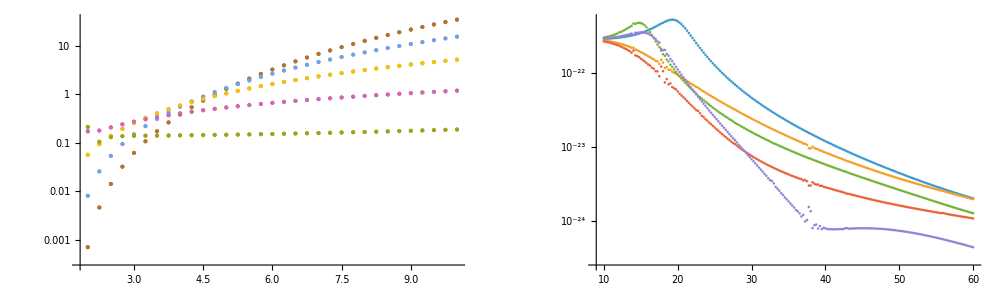

```mathematica
GraphicsRow[{
ListLogPlot[
Join[
NGridData/@Abs[testL],
NGridData/@Abs[MetricReconstructRadiative`Private`Pm2ngridL[[3]]]
],PlotRange->All],
ListLogPlot[NGridData/@Abs[testR/MetricReconstructRadiative`Private`Pm2ngridR[[3]]-1],PlotRange->All]
},ImageSize->1000]
```

```mathematica
GraphicsRow[{
ListLogPlot[NGridData/@Abs[testL/MetricReconstructRadiative`Private`MMm2gridL[[3]]-1],PlotRange->All],
ListLogPlot[NGridData/@Abs[testR/MetricReconstructRadiative`Private`MMm2gridR[[3]]-1],PlotRange->All]
},ImageSize->1000]
```

-Graphics-

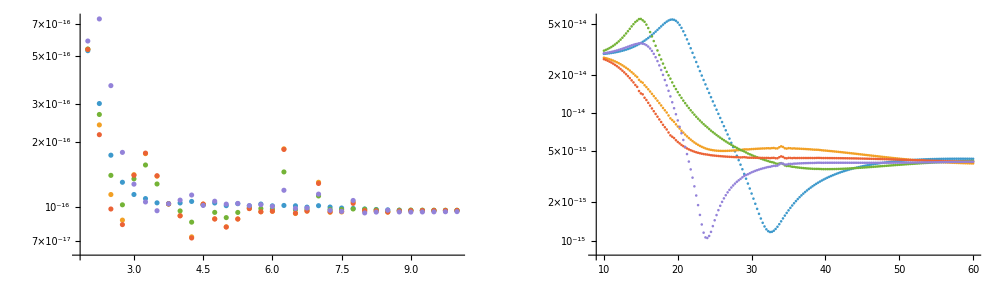

```mathematica
GraphicsRow[{
ListLogPlot[NGridData/@Abs[MetricReconstructRadiative`Private`MMm2gridL[[3]]/MetricReconstructRadiative`Private`Pm2ngridL[[3]]-1],PlotRange->All],
ListLogPlot[NGridData/@Abs[MetricReconstructRadiative`Private`MMm2gridR[[3]]/MetricReconstructRadiative`Private`Pm2ngridR[[3]]-1],PlotRange->All]},ImageSize->1000]
```

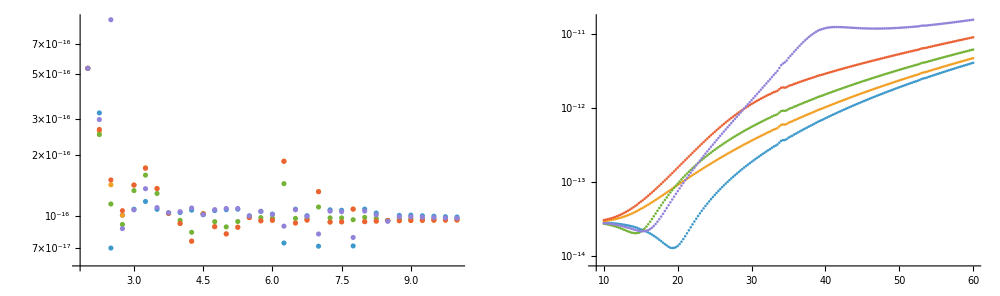

```mathematica
GraphicsRow[{
ListLogPlot[NGridData/@Abs[MetricReconstructRadiative`Private`MMp2gridL[[3]]/MetricReconstructRadiative`Private`Pp2ngridL[[3]]-1],PlotRange->All],
ListLogPlot[NGridData/@Abs[MetricReconstructRadiative`Private`MMp2gridR[[3]]/MetricReconstructRadiative`Private`Pp2ngridR[[3]]-1],PlotRange->All]},ImageSize->1000]
```

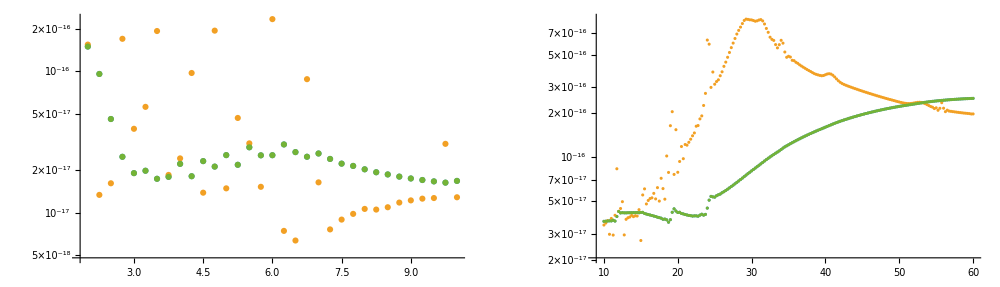

```mathematica
GraphicsRow[{
ListLogPlot[NGridData/@Abs[MetricReconstructRadiative`Private`MMm1gridL[[3]]/MetricReconstructRadiative`Private`Pm1ngridL[[3]]-1],PlotRange->All],
ListLogPlot[NGridData/@Abs[MetricReconstructRadiative`Private`MMm1gridR[[3]]/MetricReconstructRadiative`Private`Pm1ngridR[[3]]-1],PlotRange->All]},ImageSize->1000]
```

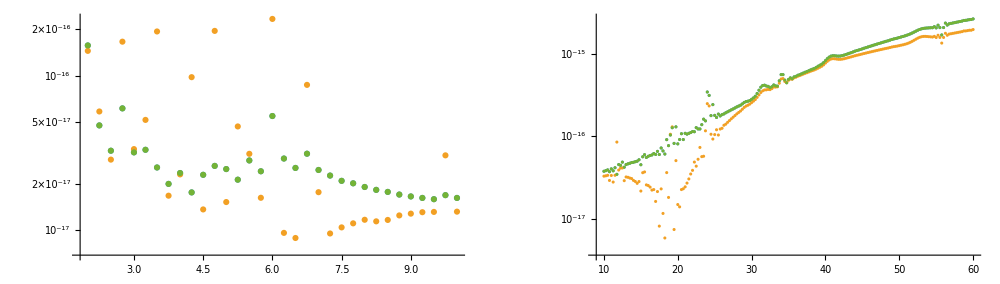

```mathematica
GraphicsRow[{
ListLogPlot[NGridData/@Abs[MetricReconstructRadiative`Private`MMp1gridL[[3]]/MetricReconstructRadiative`Private`Pp1ngridL[[3]]-1],PlotRange->All],
ListLogPlot[NGridData/@Abs[MetricReconstructRadiative`Private`MMp1gridR[[3]]/MetricReconstructRadiative`Private`Pp1ngridR[[3]]-1],PlotRange->All]},ImageSize->1000]
```

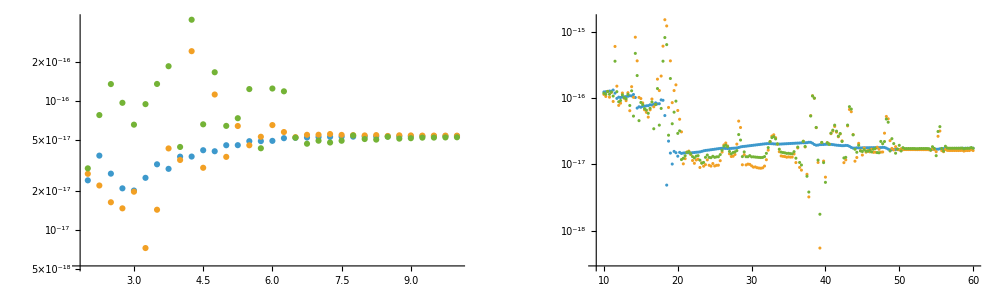

```mathematica
GraphicsRow[{
ListLogPlot[NGridData/@Abs[MetricReconstructRadiative`Private`MMh0gridL[[3]]/MetricReconstructRadiative`Private`hngridL[[3]]-1],PlotRange->All],
ListLogPlot[NGridData/@Abs[MetricReconstructRadiative`Private`MMh0gridR[[3]]/MetricReconstructRadiative`Private`hngridR[[3]]-1],PlotRange->All]},ImageSize->1000]
```

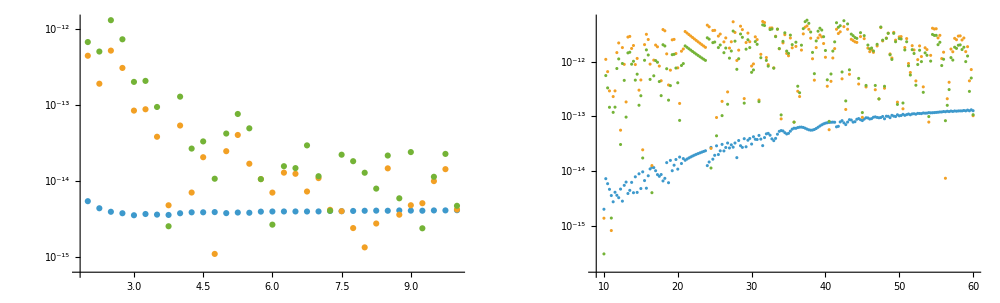

```mathematica
GraphicsRow[{
ListLogPlot[NGridData/@Abs[MetricReconstructRadiative`Private`MMκ0gridL[[3]]/MetricReconstructRadiative`Private`κngridL[[3]]-1],PlotRange->All],
ListLogPlot[NGridData/@Abs[MetricReconstructRadiative`Private`MMκ0gridR[[3]]/MetricReconstructRadiative`Private`κngridR[[3]]-1],PlotRange->All]},ImageSize->1000]
```

```mathematica
MetricReconstructRadiative`Private`MMm2gridL==MetricReconstructRadiative`Private`Pm2ngridL
```

{{0,0,0,0,0},{0,0,0,0,0},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]}}=={{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]}}

```mathematica
Max[Abs[MetricReconstructRadiative`Private`MMm2gridL-MetricReconstructRadiative`Private`Pm2ngridL]/.NGrid[_,a_]:> a]
Max[Abs[MetricReconstructRadiative`Private`MMm2gridR-MetricReconstructRadiative`Private`Pm2ngridR]/.NGrid[_,a_]:> a]
Max[Abs[MetricReconstructRadiative`Private`MMp2gridL-MetricReconstructRadiative`Private`Pp2ngridL]/.NGrid[_,a_]:> a]
Max[Abs[MetricReconstructRadiative`Private`MMp2gridR-MetricReconstructRadiative`Private`Pp2ngridR]/.NGrid[_,a_]:> a]
```

2.188830932×10^-19

3.45746502817×10^-17

2.133193241×10^-19

7.543454255×10^-16

3.3518×10^-15

3.7295535×10^-12

1.6204×10^-14

2.65633×10^-11

```mathematica
Max[Abs[MetricReconstructRadiative`Private`MMm1gridL-MetricReconstructRadiative`Private`Pm1ngridL]/.NGrid[_,a_]:> a]
Max[Abs[MetricReconstructRadiative`Private`MMm1gridR-MetricReconstructRadiative`Private`Pm1ngridR]/.NGrid[_,a_]:> a]
Max[Abs[MetricReconstructRadiative`Private`MMp1gridL-MetricReconstructRadiative`Private`Pp1ngridL]/.NGrid[_,a_]:> a]
Max[Abs[MetricReconstructRadiative`Private`MMp1gridR-MetricReconstructRadiative`Private`Pp1ngridR]/.NGrid[_,a_]:> a]
```

5.6043890071×10^-18

1.62747059×10^-17

5.5400433585×10^-18

3.99060286×10^-17

8.274633×10^-15

1.570877×10^-13

8.188369×10^-15

1.93495×10^-13

```mathematica
Max[Abs[MetricReconstructRadiative`Private`MMh0gridL-MetricReconstructRadiative`Private`hngridL]/.NGrid[_,a_]:> a]
Max[Abs[MetricReconstructRadiative`Private`MMh0gridR-MetricReconstructRadiative`Private`hngridR]/.NGrid[_,a_]:> a]
Max[Abs[MetricReconstructRadiative`Private`MMκ0gridL-MetricReconstructRadiative`Private`κngridL]/.NGrid[_,a_]:> a]
Max[Abs[MetricReconstructRadiative`Private`MMκ0gridR-MetricReconstructRadiative`Private`κngridR]/.NGrid[_,a_]:> a]
```

2.433250226×10^-21

3.9090380682×10^-21

2.044510182674×10^-14

1.841904980875607×10^-12

2.03915×10^-17

4.793378×10^-17

6.35467218×10^-12

3.776221684×10^-10

## Jumps

```mathematica
aω0=0.0372407385879122003761221264987321659843800600393017722935`28.624649298426824
```

0.0372407385879122003761221265

```mathematica
MetricReconstructRadiative`Private`s0jumps2[[2;;-1;;2]]==
MetricReconstructRadiative`Private`s0jumps
```

True

```mathematica
MetricReconstructRadiative`Private`knowns==
MetricReconstructRadiative`Private`knowns2
```

True

```mathematica
MetricReconstructRadiative`Private`GetΛ[5,2,aω0]
```

27.83204278940179801341864751

```mathematica
MetricReconstructRadiative`Private`sourcetermsubs==
MetricReconstructRadiative`Private`sourcesubs2
```

True

```mathematica
Get["MetricReconstructRadiative`"]
```

Refactor attempt 2...

```mathematica
Precision@MetricReconstructRadiative`Private`s2jumps[[All,2]]
```

27.4946

```mathematica
ω0//Precision
```

47.5957

```mathematica
Precision@KerrEnergy[OD]
```

31.0467

```mathematica
0.9533607189325169174483829268047949607138235988009352697419`32.24437497790951
```

```mathematica
MetricReconstructRadiative`Private`orbitsubs
```

{MetricReconstructRadiative`Private`LL→3.554743439237623155614537018516,MetricReconstructRadiative`Private`EE→0.95336071893251691744838292680479,MetricReconstructRadiative`Private`Ω→0.03103394882326016698010177208228,MetricReconstructRadiative`Private`ut→1.186179125325062522081909527907}

```mathematica
MetricReconstructRadiative`Private`s2jumps2[[-1]]
```

MetricReconstructRadiative`Private`Pm2j1[5]→12.0713695063935943-20.82534054413119405 ⅈ

```mathematica
Precision/@MetricReconstructRadiative`Private`s2jumps2[[All,2]]
```

{28.2438,28.0119,28.2438,28.0119,28.2186,27.3807,28.2186,27.3807,27.9407,28.0522,27.9407,28.0522,28.2727,27.4057,28.2727,27.4057}

```mathematica
Max@Abs[MetricReconstructRadiative`Private`s2jumps[[All,2]]/
MetricReconstructRadiative`Private`s2jumps2[[All,2]]-1]
```

3.×10^-38

```mathematica
ClearSWSH[]
```

```mathematica
??SpinWeightedSphericalHarmonic
```

```mathematica
SpinWeightedSphericalHarmonic[-2,2,2][0]
```

(√(5/2))/4

```mathematica
SpinWeightedSphericalHarmonicY[-2,2,2,π/2,0]/((SpinWeightedSphericalHarmonic[-2,2,2][0])/(√(2π)))
```

1

```mathematica
SpinWeightedSpheroidalHarmonics[-2,2,2,a ω0][0]
```

$Aborted

```mathematica
a=SetPrecision[a,32]
```

0.6

```mathematica
a ω0
```

0.037240738587912200376122126498732

```mathematica
SpinWeightedSpheroidalHarmonicS[2,ll,m,a ω0][π/2,0]
```

```mathematica
SpinWeightedSpheroidalHarmonic[2,2,2,a ω0]
```

$Aborted

```mathematica
lmax
```

5

```mathematica
MetricReconstructRadiative`Private`CalcJump[{2,2,MetricReconstructRadiative`Private`GetΛ[5,2,aω0]},OD,{SpinWeightedSpheroidalHarmonicS[-2,5,2,aω0][π/2,0],D[SpinWeightedSpheroidalHarmonicS[-2,5,2,aω0][θ,0],θ]/.θ->π/2}]
```

19.28

```mathematica
MetricReconstructRadiative`Private`GetΛ[5,2,aω0]
```

27.83204278940179801341864751

```mathematica
nterms
```

8

```mathematica
SpinWeightedSpheroidalHarmonicS[-2,5,2,aω0,Method->{"SphericalExpansion","NumTerms"->nterms}][π/2,0]
D[SpinWeightedSpheroidalHarmonicS[-2,5,2,aω0,Method->{"SphericalExpansion","NumTerms"->nterms}][θ,0],θ]/.θ->π/2
```

0.2310539157152678055526334833

-1.182597610945223222459455497

```mathematica
Options@SpinWeightedSpheroidalHarmonicS
```

{Method→Automatic}

```mathematica
With[{m=2,lmins2=2},
Flatten@Table[ 
Join[
{Pp2j0[ll]->#[[1]],Pp2j1[ll]->#[[2]]}&@MetricReconstructRadiative`Private`CalcJump[{2,m,MetricReconstructRadiative`Private`GetΛ[ll,m,a ω0]},OD,{SpinWeightedSpheroidalHarmonicS[2,ll,m,a ω0][π/2.`64,0.``100],D[SpinWeightedSpheroidalHarmonicS[2,ll,m,a ω0][θ,0.``100],θ]/.θ->π/2}]
,
{Pm2j0[ll]->#[[1]],Pm2j1[ll]->#[[2]]}&@MetricReconstructRadiative`Private`CalcJump[{-2,m,MetricReconstructRadiative`Private`GetΛ[ll,m,a ω0]},OD,{SpinWeightedSpheroidalHarmonicS[-2,ll,m,a ω0][π/2.`32,0.``100],D[SpinWeightedSpheroidalHarmonicS[-2,ll,m,a ω0][θ,0.``100],θ]/.θ->π/2}]
]
,
{ll,lmins2,lmax}
]
]
```

{Pp2j0[2]→-0.28181916444570151998508334108+35.091377106631020926051873539 ⅈ,Pp2j1[2]→-18.549293269606376705956133874+7.6417559574802648864247995242 ⅈ,Pm2j0[2]→-0.28181916444570151998508334108-35.091377106631020926051873539 ⅈ,Pm2j1[2]→-18.549293269606376705956133874-7.6417559574802648864247995242 ⅈ,Pp2j0[3]→-0.67736654496454215243895984723+51.319975878072220242441087167 ⅈ,Pp2j1[3]→6.789362737869194579979782842+10.989252035710773800358077816 ⅈ,Pm2j0[3]→0.67736654496454215243895984723+51.319975878072220242441087167 ⅈ,Pm2j1[3]→-6.789362737869194579979782842+10.989252035710773800358077816 ⅈ,Pp2j0[4]→-0.39189205483991812940821894167-39.040913285864324277273340045 ⅈ,Pp2j1[4]→73.860484062770071216092636883-8.9980627357479068277464960272 ⅈ,Pm2j0[4]→-0.39189205483991812940821894167+39.040913285864324277273340045 ⅈ,Pm2j1[4]→73.860484062770071216092636883+8.9980627357479068277464960272 ⅈ,Pp2j0[5]→0.41986237972195501551017420573-94.534970881963982331992581718 ⅈ,Pp2j1[5]→-12.07136950639359433907091288-20.825340544131194045171841464 ⅈ,Pm2j0[5]→-0.41986237972195501551017420573-94.534970881963982331992581718 ⅈ,Pm2j1[5]→12.07136950639359433907091288-20.825340544131194045171841464 ⅈ}

```mathematica
MetricReconstructRadiative`Private`MMhκvec[[3,1,1]]
```

{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]}

```mathematica
ConstructSolutionhκ[{{inhs_,inκs_},{uphs_,upκs_}},{hj0_,hj1_},{κj0_,κj1_}]:=Module[
{hup0,hup1,hin0,hin1,κup0,κup1,κin0,κin1,αhin,αhup,ακup,ακin},
hin0=inhs[[1,2,-1]];
hin1=inhs[[2,2,-1]];
hup0=uphs[[1,2,1]];
hup1=uphs[[2,2,1]];
κin0=inκs[[1,2,-1]];
κin1=inκs[[2,2,-1]];
κup0=upκs[[1,2,1]];
κup1=upκs[[2,2,1]];
{αhup,αhin}={(hj1 hin0-hj0 hin1)/(-hin1 hup0+hin0 hup1),(hj1 hup0-hj0 hup1)/(-hin1 hup0+hin0 hup1)};
ακup=(-hin1 (αhin κin0+κj0-αhup κup0)+hin0 (αhin κin1+κj1-αhup κup1))/(-hin1 hup0+hin0 hup1);ακin=(-hup1 (αhin κin0+κj0-αhup κup0)+hup0 (αhin κin1+κj1-αhup κup1))/(-hin1 hup0+hin0 hup1);
Return[{αhin inhs,αhup uphs,ακin*inhs+αhin inκs,ακup*uphs+αhup upκs}]
]
```

```mathematica
With[{
MMhκvec=MetricReconstructRadiative`Private`MMhκvec,
hj0=MetricReconstructRadiative`Private`hj0,
hj1=MetricReconstructRadiative`Private`hj1,
κj0=MetricReconstructRadiative`Private`κj0,
κj1=MetricReconstructRadiative`Private`κj1,
s0jumps=MetricReconstructRadiative`Private`s0jumps,
knowns=MetricReconstructRadiative`Private`knowns,
ll=2
},
ConstructSolutionhκ[MMhκvec[[ll+1]],{hj0[ll],hj1[ll]}/.s0jumps,{κj0[ll],κj1[ll]}/.knowns]
]
```

{{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>]},{NGrid[{gridL,33},<>],NGrid[{gridL,33},<>],NGrid[{gridL,33},<>]},{NGrid[{gridR,201},<>],NGrid[{gridR,201},<>],NGrid[{gridR,201},<>]}}